## test

```mathematica
Clear[kf1,B,ifun];

kf1[μ_,vf_,cq_,B_,θ_,chi_]:=Block[{e=1},

1/(6 cq)(-2+((-8 vf^3-36 cq vf^2 μ-54 B chi cq^2 e vf^3 Cos[θ]+4 vf^(3/2) √(-4 (vf+3 cq μ)^3+vf (2 vf+9 cq μ+27/2 B chi cq^2 e vf Cos[θ])^2))^(1/3))/vf+(2 2^(2/3) (vf+3 cq μ))/(-18 cq vf^2 μ-vf^3 (4+27 B chi cq^2 e Cos[θ])+3 √3 cq √(vf^3) √(-4 μ^2 (vf+4 cq μ)+B chi e vf^2 Cos[θ] (8 vf+36 cq μ+27 B chi cq^2 e vf Cos[θ])))^(1/3))
];


ifun[μ_,vf_,cq_,B_,chi_]:=Block[{e=1,θ,kfvals,dat,len,i,list},
kfvals[θ_]=1/(6 cq)(-2+((-8 vf^3-36 cq vf^2 μ-54 B chi cq^2 e vf^3 Cos[θ]+4 vf^(3/2) √(-4 (vf+3 cq μ)^3+vf (2 vf+9 cq μ+27/2 B chi cq^2 e vf Cos[θ])^2))^(1/3))/vf+(2 2^(2/3) (vf+3 cq μ))/(-18 cq vf^2 μ-vf^3 (4+27 B chi cq^2 e Cos[θ])+3 √3 cq √(vf^3) √(-4 μ^2 (vf+4 cq μ)+B chi e vf^2 Cos[θ] (8 vf+36 cq μ+27 B chi cq^2 e vf Cos[θ])))^(1/3));
dat=Table[{θ,kfvals[θ]//Chop},{θ,0,π,π/20}];
len=Length[dat];
list=Table[{dat[[i,1]]+dat[[len,1]]+π/20,dat[[len-i,2]] },{i,1,len-1}];
dat=Join[dat,list];
Interpolation[dat,PeriodicInterpolation->True]
];
ifun[mu,vfval,cqval,100,1]
```

InterpolatingFunction[…]

8.95868

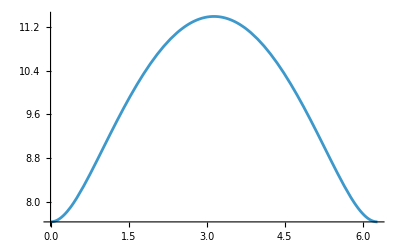

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;
kf1[mu,vfval,cqval,100,1,1]//Chop
Plot[{ifun[mu,vfval,cqval,100,1][θ]},{θ,0,2π}]
```

```mathematica
Clear[kf0,B,ifun0];

kf0[μ_,vf_,cq_,B_,θ_,chi_]:=Block[{e=1},

1/6^(2/3)(-9 B chi cq^2 e vf^3 Cos[θ]+√3 √(cq^3 vf^3) √(-4 μ^3+27 B^2 cq e^2 vf^3 Cos[θ]^2))^(1/3) (2^(1/3)/(cq vf)+(2 3^(1/3) μ)/((-9 B chi cq^2 e vf^3 Cos[θ]+√3 √(cq^3 vf^3) √(-4 μ^3+27 B^2 cq e^2 vf^3 Cos[θ]^2))^(2/3)))
];


ifun0[μ_,vf_,cq_,B_,chi_]:=Block[{e=1,θ,kfvals,dat,len,kf,list},
kfvals[θ_]=1/6^(2/3)(-9 B chi cq^2 e vf^3 Cos[θ]+√3 √(cq^3 vf^3) √(-4 μ^3+27 B^2 cq e^2 vf^3 Cos[θ]^2))^(1/3) (2^(1/3)/(cq vf)+(2 3^(1/3) μ)/((-9 B chi cq^2 e vf^3 Cos[θ]+√3 √(cq^3 vf^3) √(-4 μ^3+27 B^2 cq e^2 vf^3 Cos[θ]^2))^(2/3)));
dat=Table[{θ,kfvals[θ]//Chop},{θ,0,π,π/20}];
len=Length[dat];
list=Table[{dat[[i,1]]+dat[[len,1]]+π/20,dat[[len-i,2]] },{i,1,len-1}];
dat=Join[dat,list];
Interpolation[dat,PeriodicInterpolation->True]
];
```

12.5244

InterpolatingFunction[…]

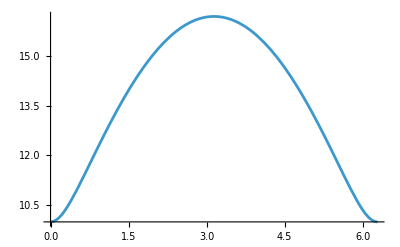

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;
kf0[mu,vfval,cqval,100,1,1]//Chop
ifun0[mu,vfval,cqval,100,1]
Plot[{ifun0[mu,vfval,cqval,100,1][θ]},{θ,0,2π}]
```

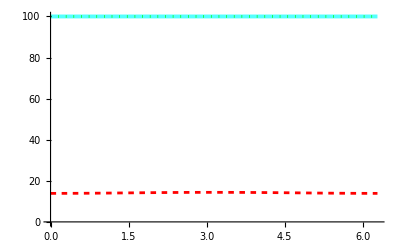

```mathematica
Clear[root0,rep];
rep={μ->0.1,vf->0.0001,cq->0.1,θ->θ,B->10,chi->1,e->1};
root0[θ_]=1/6^(2/3)(-9 B chi cq^2 e vf^3 Cos[θ]+√3 √(cq^3 vf^3) √(-4 μ^3+27 B^2 cq e^2 vf^3 Cos[θ]^2))^(1/3) (2^(1/3)/(cq vf)+(2 3^(1/3) μ)/((-9 B chi cq^2 e vf^3 Cos[θ]+√3 √(cq^3 vf^3) √(-4 μ^3+27 B^2 cq e^2 vf^3 Cos[θ]^2))^(2/3)))/.rep;
Plot[{(√μ)/(√cq √vf)/.rep,root0[θ]//Chop,ifun0[mu,vfval,cqval,10,1][θ]},{θ,0,2π},PlotStyle->{Directive[Thickness[0.007],Lighter[Cyan]],Directive[Green,Dotted],Directive[Red,Dashing[0.01]]}]
```

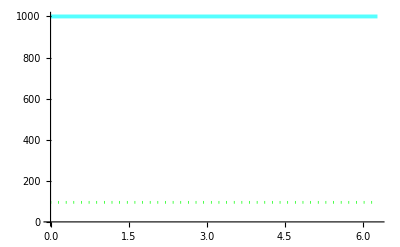

```mathematica
Clear[f1,f2,f3,root];
rep={μ->0.1,vf->0.0001,cq->0.1,θ->θ,B->10,chi->-1,e->1};
f1[θ_]=((-8 vf^3-36 cq vf^2 μ-54 B chi cq^2 e vf^3 Cos[θ]+4 vf^(3/2) √(-4 (vf+3 cq μ)^3+vf (2 vf+9 cq μ+27/2 B chi cq^2 e vf Cos[θ])^2))^(1/3))/vf/.rep;
f2[θ_]=(2 2^(2/3) (vf+3 cq μ))/(-18 cq vf^2 μ-vf^3 (4+27 B chi cq^2 e Cos[θ])+3 √3 cq √(vf^3) √(-4 μ^2 (vf+4 cq μ)+B chi e vf^2 Cos[θ] (8 vf+36 cq μ+27 B chi cq^2 e vf Cos[θ])))^(1/3)/.rep;
f3[θ_]=(-18 cq vf^2 μ-vf^3 (4+27 B chi cq^2 e Cos[θ])+3 √3 cq √(vf^3) √(-4 μ^2 (vf+4 cq μ)+B chi e vf^2 Cos[θ] (8 vf+36 cq μ+27 B chi cq^2 e vf Cos[θ])))^(1/3)/.rep;
root[θ_]=1/(6 cq)(-2+((-8 vf^3-36 cq vf^2 μ-54 B chi cq^2 e vf^3 Cos[θ]+4 vf^(3/2) √(-4 (vf+3 cq μ)^3+vf (2 vf+9 cq μ+27/2 B chi cq^2 e vf Cos[θ])^2))^(1/3))/vf+(2 2^(2/3) (vf+3 cq μ))/(-18 cq vf^2 μ-vf^3 (4+27 B chi cq^2 e Cos[θ])+3 √3 cq √(vf^3) √(-4 μ^2 (vf+4 cq μ)+B chi e vf^2 Cos[θ] (8 vf+36 cq μ+27 B chi cq^2 e vf Cos[θ])))^(1/3))/.rep;
Plot[{(μ+√(μ^2-2 B chi e vf^2 Cos[θ]))/(2 vf)/.rep,root[θ]//Chop,ifun[10,-1][θ]},{θ,0,2π},PlotStyle->{Directive[Thickness[0.007],Lighter[Cyan]],Directive[Green,Dotted],Directive[Red,Dashing[0.001]]}]
```

```mathematica
Clear[kfs,sig,B,tra11,β00,ter11,β10,vomm1,vomm2,vdotk1,vdotk2,kf1,kf2,h10,h20,h11,h21];

kfs[B_,θ_]:=Block[{kf,e=1,μ=0.1,vf=0.005,cq=0.1,kf11,kf21,kf10,kf20},

(******** first node ***************)
(******* linear band ****)
kf11=(Sort[NSolveValues[vf kf(1+2 cq kf) +(B e vf  Cos[θ])/(2 kf)==μ && kf>=0,kf,Reals]])[[1]];

(***** flat band *****)

kf10=(Sort[NSolveValues[2cq vf kf^2+(B   e vf Cos[θ])/kf==μ  && kf>=0,kf,Reals]])[[1]];
(**************************************************)
(******** second node ***************)

kf21=(Sort[NSolveValues[vf kf(1+2 cq kf) -(B e vf Cos[θ])/(2 kf)==μ && kf>=0,kf,Reals]])[[1]];
(***** flat band *****)

kf20=(Sort[NSolveValues[2cq vf kf^2-(B e vf Cos[θ])/kf==μ && kf>=0,kf,Reals]])[[1]];
{kf11,kf21,kf10,kf20}
];
kfs[1,1]
```

{0.0135167,7.81614,0.0270153,10.0135}

## sigma

```mathematica
Clear[sig,B,tra11,β00,ter11,β10,vomm1,vomm2,vdotk1,vdotk2,kf1,kf2,h10,h20,h11,h21];
(*cq <=0.001 *)
sig[B_,μ_,vf_,cq_,{tra11_,tra00_,tra10_},{ter11_,ter00_,ter10_}]:=Block[{e=1,vvec11,vvec10,vvec21,vvec20,θ,ϕ=0,θp,chi,Dphase1,Dphase2,vomm11,vomm21,vomm10,vomm20,vdotk11,vdotk21,vdotk10,vdotk20,colvec,mat,sol,Λ11,Λ21,Λ10,Λ20,a11,b11,c11,a21,b21,c21,c10,c20,conteq,matr,totmat,kf11,kf21,kf10,kf20,h11,h21,h10,h20,τ11,τ21,τ10,τ20,f11,f21,f10,f20,ct411,st411,ct4ct411,st4st411,ct4st411,ct4st211,st211,st4st211,st2st211,ct421,st421,ct4ct421,st4st421,ct4st221,st221,st4st221,st2st221,ct4st421,zero10=0,st210,st2st210,zero20=0,st220,ct220,ct2st210,ct2st220,ct210,st2st220,hzero10,hzero20,hst210,hct210,hst220,hct220,hct411, hct421,hst411,hst421,hst211,hst221,ct2ct210,ct2ct220,d10,d20,zero11=0,zero21=0,hzero21,hzero11,conteq1,conteq0,int11,int21,int10,int20,s11,s21,s10,s20},

chi=1;
(******** first node ***************)
(******* linear band ****)
kf11[θ_]=ifun[μ,vf,cq,B,chi][θ];

vvec11[θ_]=vf(1+2cq kf11[θ]){ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]};
vomm11[θ_]=(-e B vf)/(2 kf11[θ]^2){Cos[ϕ] Sin[2θ],Sin[2θ] Sin[ϕ], Cos[2 θ]};

Dphase1[θ_]=1-(B e Cos[θ])/kf11[θ]^2;
vdotk11[θ_]=vf kf11[θ] (1+2 cq kf11[θ])-(B e vf Cos[θ])/(2 kf11[θ]);
(* -Graphics-from timm-> -Graphics- from review girish*)
h11[θ_]=1/Dphase1[θ]((1+2 cq kf11[θ]) vf Cos[θ]-(B e vf   Cos[2 θ])/(2 kf11[θ]^2)+e B chi vf(-2 kf11[θ]^2 (1+2 cq kf11[θ])+B e chi Cos[θ])/(2 kf11[θ]^4)(*e B (vf χ (-2 k^2 (1+2 cq k)+B e χ Cos[θ]))/(2 k^4)*));

(***** flat band *****)

kf10[θ_]=ifun0[μ,vf,cq,B,chi][θ];

vvec10[θ_]=2cq kf10[θ]vf{ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]};
vomm10[θ_]=(-  e B vf)/kf10[θ]^2{Cos[ϕ] Sin[2 θ], Sin[2 θ] Sin[ϕ], Cos[2 θ]};
h10[θ_]=2 cq kf10[θ] vf Cos[θ]-(B   e vf Cos[2 θ])/kf10[θ]^2;
vdotk10[θ_]=(vf (2cq kf10[θ]^3-B   e Cos[θ]))/kf10[θ];
(**************************************************)
(******** second node ***************)
chi=-1;

(******linear band ****)
kf21[θ_]=ifun[μ,vf,cq,B,chi][θ];
vvec21[θ_]=vf(1+2cq kf21[θ]){ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]};
vomm21[θ_]=(e B vf)/(2 kf21[θ]^2){Cos[ϕ] Sin[2θ],Sin[2θ] Sin[ϕ], Cos[2 θ]};

Dphase2[θ_]=1+(B e Cos[θ])/kf21[θ]^2;
vdotk21[θ_]=vf kf21[θ] (1+2 cq kf21[θ])+(B e vf  Cos[θ])/(2 kf21[θ]);
h21[θ_]=1/Dphase2[θ]((1+2 cq kf21[θ]) vf Cos[θ]+(B e vf Cos[2 θ])/(2 kf21[θ]^2)+e B chi vf(-2 kf21[θ]^2 (1+2 cq kf21[θ])+B e chi Cos[θ])/(2 kf21[θ]^4));


(***** flat band *****)

kf20[θ_]=ifun0[μ,vf,cq,B,chi][θ];
vvec20[θ_]=2cq kf20[θ]vf{ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]};
vomm20[θ_]=(e B vf)/kf20[θ]^2{Cos[ϕ] Sin[2 θ], Sin[2 θ] Sin[ϕ], Cos[2 θ]};
h20[θ_]=2 cq kf20[θ] vf Cos[θ]+(B e vf Cos[2 θ])/kf20[θ]^2;
vdotk20[θ_]=(vf (2cq kf20[θ]^3+B e Cos[θ]))/kf20[θ];
(***************************************************************************************************************)
(* -Graphics- *)
τ11[θ_]=(tra11 Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Cos[θp/2]^4,{θp,0,π}]+
tra11 Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp/2]^4,{θp,0,π}]+(tra11 Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp]^2,{θp,0,π}]+(tra10 Sin[θ]^2)/2  NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Cos[θp]^2,{θp,0,π}]+(tra10 (Cos[θ/2]^4+Sin[θ/2]^4))/2  NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Sin[θp]^2,{θp,0,π}](* using 1/2 tra10 ( sin[θ]^2 cos[θp]^2+(cos[θ/2]^4+sin[θ/2]^4) sin[θp]^2) *)+
(***** conjugate node  *****)
ter11 Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Cos[θp/2]^4,{θp,0,π}]+ter11 Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp/2]^4,{θp,0,π}]+(ter11 Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp]^2,{θp,0,π}]+(ter10 Sin[θ]^2)/2  NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Cos[θp]^2,{θp,0,π}]+(ter10 (Cos[θ/2]^4+Sin[θ/2]^4))/2  NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Sin[θp]^2,{θp,0,π}](* using 1/2 tra10 ( sin[θ]^2 cos[θp]^2+(cos[θ/2]^4+sin[θ/2]^4) sin[θp]^2) *))^-1;
(********************************)
τ21[θ_]=(tra11 Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Cos[θp/2]^4,{θp,0,π}]+
tra11 Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp/2]^4,{θp,0,π}]+(tra11 Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp]^2,{θp,0,π}]+(tra10 Sin[θ]^2)/2  NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Cos[θp]^2,{θp,0,π}]+(tra10 (Cos[θ/2]^4+Sin[θ/2]^4))/2  NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Sin[θp]^2,{θp,0,π}]+
(***** conjugate node  *****)
ter11 Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Cos[θp/2]^4,{θp,0,π}]+ter11 Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp/2]^4,{θp,0,π}]+(ter11 Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp]^2,{θp,0,π}]+(ter10 Sin[θ]^2)/2  NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Cos[θp]^2,{θp,0,π}]+(ter10 (Cos[θ/2]^4+Sin[θ/2]^4))/2  NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Sin[θp]^2,{θp,0,π}](* using 1/2 tra10 ( sin[θ]^2 cos[θp]^2+(cos[θ/2]^4+sin[θ/2]^4) sin[θp]^2) *))^-1;
(********************************)
τ10[θ_]=(tra00(Cos[θ]^2)NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Cos[θp]^2,{θp,0,π}]+tra00(Sin[θ]^2/2 )NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Sin[θp]^2,{θp,0,π}]+(tra10 Cos[θ]^2)/2 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp]^2,{θp,0,π}]+(tra10 Sin[θ]^2)/2 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp](Cos[θp/2]^4+Sin[θp/2]^4),{θp,0,π}](***conj. node ************************************************)+ter00(Cos[θ]^2)NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Cos[θp]^2,{θp,0,π}]+ter00(Sin[θ]^2/2 )NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Sin[θp]^2,{θp,0,π}]+(ter10 Cos[θ]^2)/2 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp]^2,{θp,0,π}]+(ter10 Sin[θ]^2)/2 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp](Cos[θp/2]^4+Sin[θp/2]^4),{θp,0,π}](* using 1/2 tra10 ( sin[θp]^2 cos[θ]^2+(cos[θp/2]^4+sin[θp/2]^4) sin[θ]^2) *))^-1//Quiet;
(********************************)
τ20[θ_]=(tra00(Cos[θ]^2)NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Cos[θp]^2,{θp,0,π}]+tra00(Sin[θ]^2/2 )NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Sin[θp]^2,{θp,0,π}]+(tra10 Cos[θ]^2)/2 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp]^2,{θp,0,π}]+(tra10 Sin[θ]^2)/2 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp](Cos[θp/2]^4+Sin[θp/2]^4),{θp,0,π}](***conj. node ***********************************************)+ter00(Cos[θ]^2)NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Cos[θp]^2,{θp,0,π}]+ter00(Sin[θ]^2/2 )NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Sin[θp]^2,{θp,0,π}]+(ter10 Cos[θ]^2)/2 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp]^2,{θp,0,π}]+(ter10 Sin[θ]^2)/2 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp](Cos[θp/2]^4+Sin[θp/2]^4),{θp,0,π}](* using 1/2 tra10 ( sin[θp]^2 cos[θ]^2+(cos[θp/2]^4+sin[θp/2]^4) sin[θ]^2) *))^-1//Quiet;
(********************************)

(*-Graphics-*)
f11[θ_]=(Sin[θ] (kf11[θ])^3)/Abs[vdotk11[θ]] Dphase1[θ] τ11[θ];
f21[θ_]=(Sin[θ] (kf21[θ])^3)/Abs[vdotk21[θ]] Dphase2[θ]τ21[θ];
f10[θ_]=(Sin[θ] (kf10[θ])^3)/Abs[vdotk10[θ]] τ10[θ];
f20[θ_]=(Sin[θ] (kf20[θ])^3)/Abs[vdotk20[θ]] τ20[θ];

(*zero11=Quiet[NIntegrate [f11[θ],{θ,0,π}]];*)
st411=Quiet[NIntegrate [f11[θ] Sin[θ/2]^4,{θ,0,π}]];
ct411=Quiet[NIntegrate [f11[θ] Cos[θ/2]^4,{θ,0,π}]];
ct4st411=Quiet[NIntegrate [f11[θ] Cos[θ/2]^4 Sin[θ/2]^4,{θ,0,π}]];
ct4ct411=Quiet[NIntegrate [f11[θ] Cos[θ/2]^8,{θ,0,π}]];st4st411=Quiet[NIntegrate [f11[θ] Sin[θ/2]^8,{θ,0,π}]];
ct4st211=Quiet[NIntegrate [f11[θ] Cos[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st211=Quiet[NIntegrate [f11[θ] Sin[θ]^2,{θ,0,π}]];
st4st211=Quiet[NIntegrate [f11[θ] Sin[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st2st211=Quiet[NIntegrate [f11[θ] Sin[θ]^4,{θ,0,π}]];

(*zero21=Quiet[NIntegrate [f21[θ],{θ,0,π}]];*)
ct421=Quiet[NIntegrate [f21[θ] Cos[θ/2]^4,{θ,0,π}]];
st421=Quiet[NIntegrate [f21[θ] Sin[θ/2]^4,{θ,0,π}]];
ct4st421=Quiet[NIntegrate [f21[θ] Cos[θ/2]^4 Sin[θ/2]^4,{θ,0,π}]];
ct4ct421=Quiet[NIntegrate [f21[θ] Cos[θ/2]^8,{θ,0,π}]];
st4st421=Quiet[NIntegrate [f21[θ] Sin[θ/2]^8,{θ,0,π}]];
ct4st221=Quiet[NIntegrate [f21[θ] Cos[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st221=Quiet[NIntegrate [f21[θ] Sin[θ]^2,{θ,0,π}]];
st4st221=Quiet[NIntegrate [f21[θ] Sin[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st2st221=Quiet[NIntegrate [f21[θ] Sin[θ]^4,{θ,0,π}]];

(*zero10=Quiet[NIntegrate [f10[θ],{θ,0,π}]];*)
st210=Quiet[NIntegrate [f10[θ] Sin[θ]^2,{θ,0,π}]];
ct210=Quiet[NIntegrate [f10[θ] Cos[θ]^2,{θ,0,π}]];
st2st210=Quiet[NIntegrate [f10[θ] Sin[θ]^4,{θ,0,π}]];
ct2st210=Quiet[NIntegrate [f10[θ] Cos[θ]^2 Sin[θ]^2,{θ,0,π}]];
ct2ct210=Quiet[NIntegrate [f10[θ] Cos[θ]^4,{θ,0,π}]];

(*zero20=Quiet[NIntegrate [f20[θ],{θ,0,π}]];*)
st220=Quiet[NIntegrate [f20[θ] Sin[θ]^2,{θ,0,π}]];
ct220=Quiet[NIntegrate [f20[θ] Cos[θ]^2,{θ,0,π}]];
st2st220=Quiet[NIntegrate [f20[θ] Sin[θ]^4,{θ,0,π}]];
ct2st220=Quiet[NIntegrate [f20[θ] Cos[θ]^2 Sin[θ]^2,{θ,0,π}]];
ct2ct220=Quiet[NIntegrate [f20[θ] Cos[θ]^4,{θ,0,π}]];

hzero10=Quiet[NIntegrate [f10[θ]h10[θ],{θ,0,π}]];
hst210=Quiet[NIntegrate [f10[θ]h10[θ] Sin[θ]^2,{θ,0,π}]];
hct210=Quiet[NIntegrate [f10[θ]h10[θ] Cos[θ]^2,{θ,0,π}]];

hzero20=Quiet[NIntegrate [f20[θ]h20[θ],{θ,0,π}]];
hst220=Quiet[NIntegrate [f20[θ]h20[θ] Sin[θ]^2,{θ,0,π}]];
hct220=Quiet[NIntegrate [f20[θ]h20[θ] Cos[θ]^2,{θ,0,π}]];

hzero11=Quiet[NIntegrate [f11[θ]h11[θ],{θ,0,π}]];
hct411=Quiet[NIntegrate [f11[θ]h11[θ] Cos[θ/2]^4,{θ,0,π}]];
hst411=Quiet[NIntegrate [f11[θ]h11[θ] Sin[θ/2]^4,{θ,0,π}]];
hst211=Quiet[NIntegrate [f11[θ]h11[θ] Sin[θ]^2,{θ,0,π}]];

hzero21=Quiet[NIntegrate [f21[θ]h21[θ],{θ,0,π}]];hct421=Quiet[NIntegrate [f21[θ]h21[θ] Cos[θ/2]^4,{θ,0,π}]];hst421=Quiet[NIntegrate [f21[θ]h21[θ] Sin[θ/2]^4,{θ,0,π}]];
hst221=Quiet[NIntegrate [f21[θ]h21[θ] Sin[θ]^2,{θ,0,π}]];


colvec=1/2({{hst220 ter10+2 hst421 ter11+hst210 tra10+2 hct411 tra11}, {hst220 ter10+2 hct421 ter11+hst210 tra10+2 hst411 tra11}, {1/2 (2 hct220 ter10+hst221 ter11+2 hct210 tra10+hst211 tra11)}, {hst210 ter10+2 hst411 ter11+hst220 tra10+2 hct421 tra11}, {hst210 ter10+2 hct411 ter11+hst220 tra10+2 hst421 tra11}, {1/2 (2 hct210 ter10+hst211 ter11+2 hct220 tra10+hst221 tra11)}, {hst220 ter00+(hct421+hst421) ter10+hst210 tra00+(hct411+hst411) tra10}, {2 hct220 ter00+hst221 ter10+2 hct210 tra00+hst211 tra10}, {hst210 ter00+(hct411+hst411) ter10+hst220 tra00+(hct421+hst421) tra10}, {2 hct210 ter00+hst211 ter10+2 hct220 tra00+hst221 tra10}});
matr=({{1-ct4ct411 tra11, -ct4st411 tra11, -ct4st211 tra11, -ct4st421 ter11, -st4st421 ter11, -st4st221 ter11, -(st2st210 tra10)/2, -(ct2st210 tra10)/2, -(st2st220 ter10)/2, -(ct2st220 ter10)/2}, {-ct4st411 tra11, 1-st4st411 tra11, -st4st211 tra11, -ct4ct421 ter11, -ct4st421 ter11, -ct4st221 ter11, -(st2st210 tra10)/2, -(ct2st210 tra10)/2, -(st2st220 ter10)/2, -(ct2st220 ter10)/2}, {-(ct4st211 tra11)/4, -(st4st211 tra11)/4, 1-(st2st211 tra11)/4, -(ct4st221 ter11)/4, -(st4st221 ter11)/4, -(st2st221 ter11)/4, -(ct2st210 tra10)/2, -(ct2ct210 tra10)/2, -(ct2st220 ter10)/2, -(ct2ct220 ter10)/2}, {-ct4st411 ter11, -st4st411 ter11, -st4st211 ter11, 1-ct4ct421 tra11, -ct4st421 tra11, -ct4st221 tra11, -(st2st210 ter10)/2, -(ct2st210 ter10)/2, -(st2st220 tra10)/2, -(ct2st220 tra10)/2}, {-ct4ct411 ter11, -ct4st411 ter11, -ct4st211 ter11, -ct4st421 tra11, 1-st4st421 tra11, -st4st221 tra11, -(st2st210 ter10)/2, -(ct2st210 ter10)/2, -(st2st220 tra10)/2, -(ct2st220 tra10)/2}, {-(ct4st211 ter11)/4, -(st4st211 ter11)/4, -(st2st211 ter11)/4, -(ct4st221 tra11)/4, -(st4st221 tra11)/4, 1-(st2st221 tra11)/4, -(ct2st210 ter10)/2, -(ct2ct210 ter10)/2, -(ct2st220 tra10)/2, -(ct2ct220 tra10)/2}, {-1/2 (ct4ct411+ct4st411) tra10, -1/2 (ct4st411+st4st411) tra10, -1/2 (ct4st211+st4st211) tra10, -1/2 (ct4ct421+ct4st421) ter10, -1/2 (ct4st421+st4st421) ter10, -1/2 (ct4st221+st4st221) ter10, 1-(st2st210 tra00)/2, -(ct2st210 tra00)/2, -(st2st220 ter00)/2, -(ct2st220 ter00)/2}, {-(ct4st211 tra10)/2, -(st4st211 tra10)/2, -(st2st211 tra10)/2, -(ct4st221 ter10)/2, -(st4st221 ter10)/2, -(st2st221 ter10)/2, -ct2st210 tra00, 1-ct2ct210 tra00, -ct2st220 ter00, -ct2ct220 ter00}, {-1/2 (ct4ct411+ct4st411) ter10, -1/2 (ct4st411+st4st411) ter10, -1/2 (ct4st211+st4st211) ter10, -1/2 (ct4ct421+ct4st421) tra10, -1/2 (ct4st421+st4st421) tra10, -1/2 (ct4st221+st4st221) tra10, -(st2st210 ter00)/2, -(ct2st210 ter00)/2, 1-(st2st220 tra00)/2, -(ct2st220 tra00)/2}, {-(ct4st211 ter10)/2, -(st4st211 ter10)/2, -(st2st211 ter10)/2, -(ct4st221 tra10)/2, -(st4st221 tra10)/2, -(st2st221 tra10)/2, -ct2st210 ter00, -ct2ct210 ter00, -ct2st220 tra00, 1-ct2ct220 tra00}});
mat=matr.{a11,b11,c11,a21,b21,c21,c10,d10,c20,d20};

 conteq1=(a11 ct411-hzero11+c11 st211+b11 st411)+(a21 ct421-hzero21+c21 st221+b21 st421);conteq0=(-hzero10 +c10 st210+d10 ct210)+(-hzero20 +c20 st220+d20 ct220);
conteq=conteq1+conteq0;

sol=Flatten[Solve[{mat[[1]]+colvec[[1]]==0,mat[[2]]+colvec[[2]]==0,mat[[3]]+colvec[[3]]==0,mat[[4]]+colvec[[4]]==0,mat[[5]]+colvec[[5]]==0,mat[[6]]+colvec[[6]]==0,mat[[7]]+colvec[[7]]==0,mat[[8]]+colvec[[8]]==0,mat[[9]]+colvec[[9]]==0,mat[[10]]+colvec[[10]]==0,conteq==0},{a11,b11,c11,a21,b21,c21,c10,d10,c20,d20}],1];

Λ11[θ_]=τ11[θ](-h11[θ]+a11  Cos[θ/2]^4 +b11 Sin[θ/2]^4+c11 Sin[θ]^2)/.sol;
Λ21[θ_]=τ21[θ](-h21[θ]+a21 Cos[θ/2]^4+b21 Sin[θ/2]^4+c21 Sin[θ]^2)/.sol;
Λ10[θ_]=τ10[θ](-h10[θ]+c10 Sin[θ]^2+d10 Cos[θ]^2)/.sol;
Λ20[θ_]=τ20[θ](-h10[θ]+c20 Sin[θ]^2+d20 Cos[θ]^2)/.sol;
(* -Graphics- *)
int11[θ_]=-(Sin[θ] (kf11[θ])^3)/Abs[vdotk11[θ]]( e^2 B (vf (-2 kf11[θ]^2 (1+2 cq kf11[θ])+B e Cos[θ]))/(2 kf11[θ]^4)+ e(vvec11[θ]+vomm11[θ])[[3]])Λ11[θ];
int21[θ_]=-(Sin[θ] (kf21[θ])^3)/Abs[vdotk21[θ]](-e^2 B(vf (-2 kf21[θ]^2 (1+2 cq kf21[θ])-B e Cos[θ]))/(2 kf21[θ]^4) + e(vvec21[θ]+vomm21[θ])[[3]] )Λ21[θ];

int10[θ_]=-(Sin[θ] (kf10[θ])^3)/Abs[vdotk10[θ]]e(vvec10[θ]+vomm10[θ])[[3]]  Λ10[θ];int20[θ_]=-(Sin[θ] (kf20[θ])^3)/Abs[vdotk20[θ]]e(vvec20[θ]+vomm20[θ])[[3]] Λ20[θ];

s11=NIntegrate[int11[θ],{θ,0,π}]//Quiet;
s21=NIntegrate[int21[θ],{θ,0,π}]//Quiet;
s10=NIntegrate[int10[θ],{θ,0,π}]//Quiet;
s20=NIntegrate[int20[θ],{θ,0,π}]//Quiet;

{B,s11+s21,s10+s20,{s11,s21,s10,s20},MatrixRank[matr],MatrixForm[{a11,b11,c11,a21,b21,c21,c10,d10,c20,d20}/.sol]}
];
(* sig[B_,μ_,vf_,cq_,{tra11_,tra00_,tra10_},{ter11_,ter00_,ter10_}] *)
mu=0.1;cqval=0.1;vfval=0.005;rat1=0.5;
val1={5,2,0.1};val2=rat1 val1;
sig[8.1,mu,vfval,cqval,val1,val2]
```

{8.1,0.0000691991,0.000130211,{0.0000345995,0.0000345995,0.0000651377,0.0000650736},9,(-0.00235527
0.00334803
0.000246595
-0.00334803
0.00235527
-0.000246595
-0.000015593
0.0000752264
0.000015593
-0.0000752264)}

## sigma at B=0

```mathematica
Clear[sig0,tra11,β00,ter11,β10,vomm1,vomm2,vdotk1,vdotk2,kf1,kf2,h10,h20,h11,h21];
(*cq <=0.001 *)
sig0[μ_,vf_,cq_,{tra11_,tra00_,tra10_},{ter11_,ter00_,ter10_}]:=Block[{B=0,e=1,vvec11,vvec10,vvec21,vvec20,θ,ϕ=0,θp,chi,Dphase1,Dphase2,vomm11,vomm21,vomm10,vomm20,vdotk11,vdotk21,vdotk10,vdotk20,colvec,mat,sol,Λ11,Λ21,Λ10,Λ20,a11,b11,c11,a21,b21,c21,c10,c20,conteq,matr,totmat,kf11,kf21,kf10,kf20,h11,h21,h10,h20,τ11,τ21,τ10,τ20,f11,f21,f10,f20,ct411,st411,ct4ct411,st4st411,ct4st411,ct4st211,st211,st4st211,st2st211,ct421,st421,ct4ct421,st4st421,ct4st221,st221,st4st221,st2st221,ct4st421,zero10=0,st210,st2st210,zero20=0,st220,ct220,ct2st210,ct2st220,ct210,st2st220,hzero10,hzero20,hst210,hct210,hst220,hct220,hct411, hct421,hst411,hst421,hst211,hst221,ct2ct210,ct2ct220,d10,d20,zero11=0,zero21=0,hzero21,hzero11,conteq1,conteq0,int11,int21,int10,int20,s11,s21,s10,s20},

chi=1;
(******** first node ***************)
(******* linear band ****)
kf11[θ_]=(-vf+√vf √(vf+4 cq μ))/(2 cq vf);

vvec11[θ_]=vf(1+2cq kf11[θ]){ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]};
vomm11[θ_]=(-e B vf)/(2 kf11[θ]^2){Cos[ϕ] Sin[2θ],Sin[2θ] Sin[ϕ], Cos[2 θ]};

Dphase1[θ_]=1 ;
vdotk11[θ_]=vf kf11[θ] (1+2 cq kf11[θ]);
(* -Graphics-from timm-> -Graphics- from review girish*)
h11[θ_]=1/Dphase1[θ]((1+2 cq kf11[θ]) vf Cos[θ]-(B e vf   Cos[2 θ])/(2 kf11[θ]^2)+e B chi vf(-2 kf11[θ]^2 (1+2 cq kf11[θ])+B e chi Cos[θ])/(2 kf11[θ]^4)(*e B (vf χ (-2 k^2 (1+2 cq k)+B e χ Cos[θ]))/(2 k^4)*));

(***** flat band *****)

kf10[θ_]=(√μ)/(√cq √vf);

vvec10[θ_]=2cq kf10[θ]vf{ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]};
vomm10[θ_]=(-  e B vf)/kf10[θ]^2{Cos[ϕ] Sin[2 θ], Sin[2 θ] Sin[ϕ], Cos[2 θ]};
h10[θ_]=2 cq kf10[θ] vf Cos[θ];
vdotk10[θ_]=(vf (2cq kf10[θ]^3))/kf10[θ];
(**************************************************)
(******** second node ***************)
chi=-1;

(******linear band ****)
kf21[θ_]=(-vf+√vf √(vf+4 cq μ))/(2 cq vf);
vvec21[θ_]=vf(1+2cq kf21[θ]){ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]};
vomm21[θ_]=(e B vf)/(2 kf21[θ]^2){Cos[ϕ] Sin[2θ],Sin[2θ] Sin[ϕ], Cos[2 θ]};

Dphase2[θ_]=1;
vdotk21[θ_]=vf kf21[θ] (1+2 cq kf21[θ]);
h21[θ_]=1/Dphase2[θ]((1+2 cq kf21[θ]) vf Cos[θ]+(B e vf Cos[2 θ])/(2 kf21[θ]^2)+e B chi vf(-2 kf21[θ]^2 (1+2 cq kf21[θ])+B e chi Cos[θ])/(2 kf21[θ]^4));


(***** flat band *****)

kf20[θ_]=(√μ)/(√cq √vf);
vvec20[θ_]=2cq kf20[θ]vf{ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]};
vomm20[θ_]={0,0,0};
h20[θ_]=2 cq kf20[θ] vf Cos[θ];
vdotk20[θ_]=(vf (2cq kf20[θ]^3))/kf20[θ];
(***************************************************************************************************************)
(* -Graphics- *)
τ11[θ_]=(tra11 Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Cos[θp/2]^4,{θp,0,π}]+
tra11 Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp/2]^4,{θp,0,π}]+(tra11 Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp]^2,{θp,0,π}]+(tra10 Sin[θ]^2)/2  NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Cos[θp]^2,{θp,0,π}]+(tra10 (Cos[θ/2]^4+Sin[θ/2]^4))/2  NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Sin[θp]^2,{θp,0,π}](* using 1/2 tra10 ( sin[θ]^2 cos[θp]^2+(cos[θ/2]^4+sin[θ/2]^4) sin[θp]^2) *)+
(***** conjugate node  *****)
ter11 Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Cos[θp/2]^4,{θp,0,π}]+ter11 Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp/2]^4,{θp,0,π}]+(ter11 Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp]^2,{θp,0,π}]+(ter10 Sin[θ]^2)/2  NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Cos[θp]^2,{θp,0,π}]+(ter10 (Cos[θ/2]^4+Sin[θ/2]^4))/2  NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Sin[θp]^2,{θp,0,π}](* using 1/2 tra10 ( sin[θ]^2 cos[θp]^2+(cos[θ/2]^4+sin[θ/2]^4) sin[θp]^2) *))^-1;
(********************************)
τ21[θ_]=(tra11 Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Cos[θp/2]^4,{θp,0,π}]+
tra11 Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp/2]^4,{θp,0,π}]+(tra11 Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp]^2,{θp,0,π}]+(tra10 Sin[θ]^2)/2  NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Cos[θp]^2,{θp,0,π}]+(tra10 (Cos[θ/2]^4+Sin[θ/2]^4))/2  NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Sin[θp]^2,{θp,0,π}]+
(***** conjugate node  *****)
ter11 Sin[θ/2]^4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Cos[θp/2]^4,{θp,0,π}]+ter11 Cos[θ/2]^4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp/2]^4,{θp,0,π}]+(ter11 Sin[θ]^2)/4 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp]^2,{θp,0,π}]+(ter10 Sin[θ]^2)/2  NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Cos[θp]^2,{θp,0,π}]+(ter10 (Cos[θ/2]^4+Sin[θ/2]^4))/2  NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Sin[θp]^2,{θp,0,π}](* using 1/2 tra10 ( sin[θ]^2 cos[θp]^2+(cos[θ/2]^4+sin[θ/2]^4) sin[θp]^2) *))^-1;
(********************************)
τ10[θ_]=(tra00(Cos[θ]^2)NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Cos[θp]^2,{θp,0,π}]+tra00(Sin[θ]^2/2 )NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Sin[θp]^2,{θp,0,π}]+(tra10 Cos[θ]^2)/2 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp]^2,{θp,0,π}]+(tra10 Sin[θ]^2)/2 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp](Cos[θp/2]^4+Sin[θp/2]^4),{θp,0,π}](***conj. node ************************************************)+ter00(Cos[θ]^2)NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Cos[θp]^2,{θp,0,π}]+ter00(Sin[θ]^2/2 )NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Sin[θp]^2,{θp,0,π}]+(ter10 Cos[θ]^2)/2 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp]^2,{θp,0,π}]+(ter10 Sin[θ]^2)/2 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp](Cos[θp/2]^4+Sin[θp/2]^4),{θp,0,π}](* using 1/2 tra10 ( sin[θp]^2 cos[θ]^2+(cos[θp/2]^4+sin[θp/2]^4) sin[θ]^2) *))^-1//Quiet;
(********************************)
τ20[θ_]=(tra00(Cos[θ]^2)NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Cos[θp]^2,{θp,0,π}]+tra00(Sin[θ]^2/2 )NIntegrate [(Sin[θp] (kf20[θp])^3)/Abs[vdotk20[θp]] Sin[θp]^2,{θp,0,π}]+(tra10 Cos[θ]^2)/2 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp] Sin[θp]^2,{θp,0,π}]+(tra10 Sin[θ]^2)/2 NIntegrate [(Sin[θp] (kf21[θp])^3)/Abs[vdotk21[θp]] Dphase2[θp](Cos[θp/2]^4+Sin[θp/2]^4),{θp,0,π}](***conj. node ***********************************************)+ter00(Cos[θ]^2)NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Cos[θp]^2,{θp,0,π}]+ter00(Sin[θ]^2/2 )NIntegrate [(Sin[θp] (kf10[θp])^3)/Abs[vdotk10[θp]] Sin[θp]^2,{θp,0,π}]+(ter10 Cos[θ]^2)/2 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp] Sin[θp]^2,{θp,0,π}]+(ter10 Sin[θ]^2)/2 NIntegrate [(Sin[θp] (kf11[θp])^3)/Abs[vdotk11[θp]] Dphase1[θp](Cos[θp/2]^4+Sin[θp/2]^4),{θp,0,π}](* using 1/2 tra10 ( sin[θp]^2 cos[θ]^2+(cos[θp/2]^4+sin[θp/2]^4) sin[θ]^2) *))^-1//Quiet;
(********************************)

(*-Graphics-*)
f11[θ_]=(Sin[θ] (kf11[θ])^3)/Abs[vdotk11[θ]] Dphase1[θ] τ11[θ];
f21[θ_]=(Sin[θ] (kf21[θ])^3)/Abs[vdotk21[θ]] Dphase2[θ]τ21[θ];
f10[θ_]=(Sin[θ] (kf10[θ])^3)/Abs[vdotk10[θ]] τ10[θ];
f20[θ_]=(Sin[θ] (kf20[θ])^3)/Abs[vdotk20[θ]] τ20[θ];

(*zero11=Quiet[NIntegrate [f11[θ],{θ,0,π}]];*)
st411=Quiet[NIntegrate [f11[θ] Sin[θ/2]^4,{θ,0,π}]];
ct411=Quiet[NIntegrate [f11[θ] Cos[θ/2]^4,{θ,0,π}]];
ct4st411=Quiet[NIntegrate [f11[θ] Cos[θ/2]^4 Sin[θ/2]^4,{θ,0,π}]];
ct4ct411=Quiet[NIntegrate [f11[θ] Cos[θ/2]^8,{θ,0,π}]];st4st411=Quiet[NIntegrate [f11[θ] Sin[θ/2]^8,{θ,0,π}]];
ct4st211=Quiet[NIntegrate [f11[θ] Cos[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st211=Quiet[NIntegrate [f11[θ] Sin[θ]^2,{θ,0,π}]];
st4st211=Quiet[NIntegrate [f11[θ] Sin[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st2st211=Quiet[NIntegrate [f11[θ] Sin[θ]^4,{θ,0,π}]];

(*zero21=Quiet[NIntegrate [f21[θ],{θ,0,π}]];*)
ct421=Quiet[NIntegrate [f21[θ] Cos[θ/2]^4,{θ,0,π}]];
st421=Quiet[NIntegrate [f21[θ] Sin[θ/2]^4,{θ,0,π}]];
ct4st421=Quiet[NIntegrate [f21[θ] Cos[θ/2]^4 Sin[θ/2]^4,{θ,0,π}]];
ct4ct421=Quiet[NIntegrate [f21[θ] Cos[θ/2]^8,{θ,0,π}]];
st4st421=Quiet[NIntegrate [f21[θ] Sin[θ/2]^8,{θ,0,π}]];
ct4st221=Quiet[NIntegrate [f21[θ] Cos[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st221=Quiet[NIntegrate [f21[θ] Sin[θ]^2,{θ,0,π}]];
st4st221=Quiet[NIntegrate [f21[θ] Sin[θ/2]^4 Sin[θ]^2,{θ,0,π}]];
st2st221=Quiet[NIntegrate [f21[θ] Sin[θ]^4,{θ,0,π}]];

(*zero10=Quiet[NIntegrate [f10[θ],{θ,0,π}]];*)
st210=Quiet[NIntegrate [f10[θ] Sin[θ]^2,{θ,0,π}]];
ct210=Quiet[NIntegrate [f10[θ] Cos[θ]^2,{θ,0,π}]];
st2st210=Quiet[NIntegrate [f10[θ] Sin[θ]^4,{θ,0,π}]];
ct2st210=Quiet[NIntegrate [f10[θ] Cos[θ]^2 Sin[θ]^2,{θ,0,π}]];
ct2ct210=Quiet[NIntegrate [f10[θ] Cos[θ]^4,{θ,0,π}]];

(*zero20=Quiet[NIntegrate [f20[θ],{θ,0,π}]];*)
st220=Quiet[NIntegrate [f20[θ] Sin[θ]^2,{θ,0,π}]];
ct220=Quiet[NIntegrate [f20[θ] Cos[θ]^2,{θ,0,π}]];
st2st220=Quiet[NIntegrate [f20[θ] Sin[θ]^4,{θ,0,π}]];
ct2st220=Quiet[NIntegrate [f20[θ] Cos[θ]^2 Sin[θ]^2,{θ,0,π}]];
ct2ct220=Quiet[NIntegrate [f20[θ] Cos[θ]^4,{θ,0,π}]];

hzero10=Quiet[NIntegrate [f10[θ]h10[θ],{θ,0,π}]];
hst210=Quiet[NIntegrate [f10[θ]h10[θ] Sin[θ]^2,{θ,0,π}]];
hct210=Quiet[NIntegrate [f10[θ]h10[θ] Cos[θ]^2,{θ,0,π}]];

hzero20=Quiet[NIntegrate [f20[θ]h20[θ],{θ,0,π}]];
hst220=Quiet[NIntegrate [f20[θ]h20[θ] Sin[θ]^2,{θ,0,π}]];
hct220=Quiet[NIntegrate [f20[θ]h20[θ] Cos[θ]^2,{θ,0,π}]];

hzero11=Quiet[NIntegrate [f11[θ]h11[θ],{θ,0,π}]];
hct411=Quiet[NIntegrate [f11[θ]h11[θ] Cos[θ/2]^4,{θ,0,π}]];
hst411=Quiet[NIntegrate [f11[θ]h11[θ] Sin[θ/2]^4,{θ,0,π}]];
hst211=Quiet[NIntegrate [f11[θ]h11[θ] Sin[θ]^2,{θ,0,π}]];

hzero21=Quiet[NIntegrate [f21[θ]h21[θ],{θ,0,π}]];hct421=Quiet[NIntegrate [f21[θ]h21[θ] Cos[θ/2]^4,{θ,0,π}]];hst421=Quiet[NIntegrate [f21[θ]h21[θ] Sin[θ/2]^4,{θ,0,π}]];
hst221=Quiet[NIntegrate [f21[θ]h21[θ] Sin[θ]^2,{θ,0,π}]];


colvec=1/2({{hst220 ter10+2 hst421 ter11+hst210 tra10+2 hct411 tra11}, {hst220 ter10+2 hct421 ter11+hst210 tra10+2 hst411 tra11}, {1/2 (2 hct220 ter10+hst221 ter11+2 hct210 tra10+hst211 tra11)}, {hst210 ter10+2 hst411 ter11+hst220 tra10+2 hct421 tra11}, {hst210 ter10+2 hct411 ter11+hst220 tra10+2 hst421 tra11}, {1/2 (2 hct210 ter10+hst211 ter11+2 hct220 tra10+hst221 tra11)}, {hst220 ter00+(hct421+hst421) ter10+hst210 tra00+(hct411+hst411) tra10}, {2 hct220 ter00+hst221 ter10+2 hct210 tra00+hst211 tra10}, {hst210 ter00+(hct411+hst411) ter10+hst220 tra00+(hct421+hst421) tra10}, {2 hct210 ter00+hst211 ter10+2 hct220 tra00+hst221 tra10}});
matr=({{1-ct4ct411 tra11, -ct4st411 tra11, -ct4st211 tra11, -ct4st421 ter11, -st4st421 ter11, -st4st221 ter11, -(st2st210 tra10)/2, -(ct2st210 tra10)/2, -(st2st220 ter10)/2, -(ct2st220 ter10)/2}, {-ct4st411 tra11, 1-st4st411 tra11, -st4st211 tra11, -ct4ct421 ter11, -ct4st421 ter11, -ct4st221 ter11, -(st2st210 tra10)/2, -(ct2st210 tra10)/2, -(st2st220 ter10)/2, -(ct2st220 ter10)/2}, {-(ct4st211 tra11)/4, -(st4st211 tra11)/4, 1-(st2st211 tra11)/4, -(ct4st221 ter11)/4, -(st4st221 ter11)/4, -(st2st221 ter11)/4, -(ct2st210 tra10)/2, -(ct2ct210 tra10)/2, -(ct2st220 ter10)/2, -(ct2ct220 ter10)/2}, {-ct4st411 ter11, -st4st411 ter11, -st4st211 ter11, 1-ct4ct421 tra11, -ct4st421 tra11, -ct4st221 tra11, -(st2st210 ter10)/2, -(ct2st210 ter10)/2, -(st2st220 tra10)/2, -(ct2st220 tra10)/2}, {-ct4ct411 ter11, -ct4st411 ter11, -ct4st211 ter11, -ct4st421 tra11, 1-st4st421 tra11, -st4st221 tra11, -(st2st210 ter10)/2, -(ct2st210 ter10)/2, -(st2st220 tra10)/2, -(ct2st220 tra10)/2}, {-(ct4st211 ter11)/4, -(st4st211 ter11)/4, -(st2st211 ter11)/4, -(ct4st221 tra11)/4, -(st4st221 tra11)/4, 1-(st2st221 tra11)/4, -(ct2st210 ter10)/2, -(ct2ct210 ter10)/2, -(ct2st220 tra10)/2, -(ct2ct220 tra10)/2}, {-1/2 (ct4ct411+ct4st411) tra10, -1/2 (ct4st411+st4st411) tra10, -1/2 (ct4st211+st4st211) tra10, -1/2 (ct4ct421+ct4st421) ter10, -1/2 (ct4st421+st4st421) ter10, -1/2 (ct4st221+st4st221) ter10, 1-(st2st210 tra00)/2, -(ct2st210 tra00)/2, -(st2st220 ter00)/2, -(ct2st220 ter00)/2}, {-(ct4st211 tra10)/2, -(st4st211 tra10)/2, -(st2st211 tra10)/2, -(ct4st221 ter10)/2, -(st4st221 ter10)/2, -(st2st221 ter10)/2, -ct2st210 tra00, 1-ct2ct210 tra00, -ct2st220 ter00, -ct2ct220 ter00}, {-1/2 (ct4ct411+ct4st411) ter10, -1/2 (ct4st411+st4st411) ter10, -1/2 (ct4st211+st4st211) ter10, -1/2 (ct4ct421+ct4st421) tra10, -1/2 (ct4st421+st4st421) tra10, -1/2 (ct4st221+st4st221) tra10, -(st2st210 ter00)/2, -(ct2st210 ter00)/2, 1-(st2st220 tra00)/2, -(ct2st220 tra00)/2}, {-(ct4st211 ter10)/2, -(st4st211 ter10)/2, -(st2st211 ter10)/2, -(ct4st221 tra10)/2, -(st4st221 tra10)/2, -(st2st221 tra10)/2, -ct2st210 ter00, -ct2ct210 ter00, -ct2st220 tra00, 1-ct2ct220 tra00}});
mat=matr.{a11,b11,c11,a21,b21,c21,c10,d10,c20,d20};

 conteq1=(a11 ct411-hzero11+c11 st211+b11 st411)+(a21 ct421-hzero21+c21 st221+b21 st421);conteq0=(-hzero10 +c10 st210+d10 ct210)+(-hzero20 +c20 st220+d20 ct220);
conteq=conteq1+conteq0;

sol=Flatten[Solve[{mat[[1]]+colvec[[1]]==0,mat[[2]]+colvec[[2]]==0,mat[[3]]+colvec[[3]]==0,mat[[4]]+colvec[[4]]==0,mat[[5]]+colvec[[5]]==0,mat[[6]]+colvec[[6]]==0,mat[[7]]+colvec[[7]]==0,mat[[8]]+colvec[[8]]==0,mat[[9]]+colvec[[9]]==0,mat[[10]]+colvec[[10]]==0,conteq==0},{a11,b11,c11,a21,b21,c21,c10,d10,c20,d20}],1];

Λ11[θ_]=τ11[θ](-h11[θ]+a11  Cos[θ/2]^4 +b11 Sin[θ/2]^4+c11 Sin[θ]^2)/.sol;
Λ21[θ_]=τ21[θ](-h21[θ]+a21 Cos[θ/2]^4+b21 Sin[θ/2]^4+c21 Sin[θ]^2)/.sol;
Λ10[θ_]=τ10[θ](-h10[θ]+c10 Sin[θ]^2+d10 Cos[θ]^2)/.sol;
Λ20[θ_]=τ20[θ](-h10[θ]+c20 Sin[θ]^2+d20 Cos[θ]^2)/.sol;
(* -Graphics- *)
int11[θ_]=-(Sin[θ] (kf11[θ])^3)/Abs[vdotk11[θ]]( e^2 B (vf (-2 kf11[θ]^2 (1+2 cq kf11[θ])+B e Cos[θ]))/(2 kf11[θ]^4)+ e(vvec11[θ]+vomm11[θ])[[3]])Λ11[θ];
int21[θ_]=-(Sin[θ] (kf21[θ])^3)/Abs[vdotk21[θ]](-e^2 B(vf (-2 kf21[θ]^2 (1+2 cq kf21[θ])-B e Cos[θ]))/(2 kf21[θ]^4) + e(vvec21[θ]+vomm21[θ])[[3]] )Λ21[θ];

int10[θ_]=-(Sin[θ] (kf10[θ])^3)/Abs[vdotk10[θ]]e(vvec10[θ]+vomm10[θ])[[3]]  Λ10[θ];int20[θ_]=-(Sin[θ] (kf20[θ])^3)/Abs[vdotk20[θ]]e(vvec20[θ]+vomm20[θ])[[3]] Λ20[θ];

s11=NIntegrate[int11[θ],{θ,0,π}]//Quiet;
s21=NIntegrate[int21[θ],{θ,0,π}]//Quiet;
s10=NIntegrate[int10[θ],{θ,0,π}]//Quiet;
s20=NIntegrate[int20[θ],{θ,0,π}]//Quiet;

{{s11+s21,s10+s20},{s11,s21,s10,s20},MatrixRank[matr],MatrixForm[{a11,b11,c11,a21,b21,c21,c10,d10,c20,d20}/.sol]}
];
(* sig[B_,μ_,vf_,cq_,{tra11_,tra00_,tra10_},{ter11_,ter00_,ter10_}] *)
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat1=0.5;
val1={5,2,0.1};val2=rat1 val1;
sig0[mu,vfval,cqval,val1,val2]
```

{{0.0000685119,0.000130263},{0.000034256,0.000034256,0.0000651315,0.0000651315},9,(-0.00285466
0.00285466
-5.5877×10^-18
-0.00285466
0.00285466
-5.36832×10^-18
3.56974×10^-18
2.94412×10^-18
7.26842×10^-18
3.3814×10^-18)}

## Results

#### all data

```mathematica
tot1={{0,{0.00003425597069921684,0.00003425597069921684,0.00006513150243204766,0.00006513150243204764}},{0.1,{0.00003425602296534721,0.000034256022965347206,0.0000651315033835606,0.00006513149361392522}},{1.1,{0.000034262295119575525,0.000034262295119575525,0.00006513161755431698,0.00006513043541469926}},{2.1,{0.00003427902298432686,0.00003427902298432685,0.0000651319219050542,0.00006512761331225152}},{3.1,{0.000034306212345478955,0.00003430621234547895,0.0000651324161502845,0.00006512302665763173}},{4.1,{0.000034343872616571164,0.00003434387261657116,0.00006513309982552992,0.00006511667439541459}},{5.1,{0.00003439201685526951,0.00003439201685526952,0.00006513397228652003,0.00006510855506243852}},{6.1,{0.00003445066178626871,0.00003445066178626872,0.00006513503270807699,0.00006509866678605418}},{7.1,{0.000034519827830732416,0.00003451982783073242,0.00006513628008268481,0.00006508700728187806}},{8.1,{0.000034599539142403524,0.000034599539142403524,0.00006513771321873782,0.00006507357385104439}},{9.1,{0.00003468982365054676,0.000034689823650546746,0.00006513933073846239,0.00006505836337694813}},{10.1,{0.00003479071310991831,0.00003479071310991832,0.00006514113107550533,0.00006504137232146941}},{15,{0.000035439680223817225,0.000035439680223817225,0.00006515253054432634,0.00006493223199346594}},{20,{0.0000363712778382629,0.000036371277838262916,0.00006516834660707226,0.00006477603158079327}},{25,{0.000037583649440112395,0.000037583649440112415,0.00006518796251361102,0.00006457360358367991}},{30,{0.0000390887167899127,0.00003908871678991265,0.00006521079393986831,0.00006432367928282046}},{35,{0.000040902283849360624,0.00004090228384936064,0.00006523607167714077,0.00006402462418928587}},{40,{0.00004304504471513321,0.00004304504471513322,0.0000652628007271704,0.00006367437747321948}},{45,{0.00004554412898180655,0.000045544128981806575,0.00006528970303835577,0.00006327036896335955}},{50,{0.000048435570555911734,0.00004843557055591174,0.00006531513679442002,0.0000628094049408725}},{55,{0.000051768516090771304,0.000051768516090771325,0.00006533698097413137,0.00006228750905749078}},{60,{0.000055613152157641004,0.0000556131521576411,0.0000653524666813489,0.00006169969647041582}}};
```

```mathematica
tot2={{0,{0.000021584257508914212,0.000021584257508914212,0.00004884862682403577,0.00004884862682403572}},{0.1,{0.000021584276837242666,0.000021584276837242666,0.000048848626990037,0.00004884861966281048}},{1.1,{0.00002158659633427259,0.00002158659633427259,0.00004884864690184046,0.00004884776029712715}},{2.1,{0.000021592782606540454,0.000021592782606540458,0.00004884869991909358,0.000048845468474491564}},{3.1,{0.000021602838238340184,0.000021602838238340177,0.00004884878582105621,0.00004884174370156664}},{4.1,{0.000021616767435293002,0.000021616767435293002,0.00004884890424861035,0.00004883658517602383}},{5.1,{0.00002163457603315709,0.000021634576033157087,0.000048849054703665486,0.000048829991785604336}},{6.1,{0.00002165627151008948,0.000021656271510089477,0.000048849236548332686,0.00004882196210681558}},{7.1,{0.000021681863002422757,0.000021681863002422743,0.00004884944900386423,0.00004881249440325917}},{8.1,{0.000021711361324037584,0.000021711361324037587,0.00004884969114935593,0.00004880158662358585}},{9.1,{0.000021744778989431277,0.00002174477898943127,0.000048849961920207244,0.00004878923639907156}},{15,{0.000022022602205483522,0.000022022602205483522,0.00004885206746410831,0.00004868684355096298}},{20,{0.000022368456295647598,0.0000223684562956476,0.00004885432726105491,0.00004856009099134566}},{25,{0.00002281974616208418,0.0000228197461620842,0.000048856678379036764,0.00004839590918158842}},{30,{0.000023381969109540255,0.000023381969109540262,0.00004885867172052493,0.00004819333572773906}},{35,{0.000024062534072701165,0.000024062534072701192,0.00004885971768526819,0.00004795113206937701}},{40,{0.000024871348586202532,0.000024871348586202543,0.00004885905596685875,0.00004766773852639556}},{45,{0.00002582174715677621,0.000025821747156776213,0.000048855713318728364,0.000047341212762481196}},{50,{0.000026932027363424093,0.000026932027363424114,0.000048848444098282905,0.000046969145208122264}},{55,{0.000028228170465960966,0.00002822817046596097,0.0000488356453311184,0.00004654854139363797}},{60,{0.000029749175784728685,0.000029749175784728685,0.00004881523275819962,0.00004607565509999982}}};
```

```mathematica
tot3={{0,{0.00001240599282907919,0.00001240599282907919,0.00003256575121602383,0.00003256575121602382}},{0.1,{0.000012406000205964744,0.000012406000205964743,0.00003256575104477293,0.00003256574615995525}},{1.1,{0.00001240688547167597,0.00001240688547167597,0.00003256573048899399,0.000032565139419185124}},{2.1,{0.000012409246562866831,0.000012409246562866835,0.00003256567561862586,0.00003256352132222453}},{3.1,{0.000012413084523972473,0.000012413084523972473,0.00003256558628369708,0.00003256089153737069}},{4.1,{0.000012418401055034396,0.000012418401055034396,0.00003256546224023141,0.00003255724952517375}},{5.1,{0.000012425198515766885,0.000012425198515766888,0.000032565303149857746,0.000032552594537816984}},{6.1,{0.000012433479931220925,0.000012433479931220927,0.000032565108579267895,0.000032546925618256504}},{7.1,{0.000012443248999078307,0.00001244324899907831,0.00003256487799952089,0.00003254024159911751}},{8.1,{0.000012454510098618516,0.00001245451009861851,0.000032564610785191286,0.000032532541101344564}},{9.1,{0.000012467268301410946,0.000012467268301410946,0.000032564306213358904,0.000032523822532601776}},{15,{0.000012573372959609896,0.000012573372959609893,0.000032561698141129436,0.000032451548865699226}},{20,{0.000012705558114183867,0.000012705558114183867,0.00003255826326635935,0.00003236210575321986}},{25,{0.000012878221093136372,0.000012878221093136382,0.00003255347124739184,0.000032246291782426294}},{30,{0.000013093647091452077,0.000013093647091452084,0.00003254701841083617,0.00003210346108231224}},{35,{0.000013354962916313852,0.000013354962916313859,0.000032538506939335296,0.00003193278319540785}},{40,{0.000013666432844094691,0.0000136664328440947,0.00003252742512106439,0.00003173321349408894}},{45,{0.00001403394201910606,0.000014033942019106052,0.00003251311976536332,0.00003150345272786522}},{50,{0.000014465826351712275,0.000014465826351712316,0.00003249475742009376,0.000031241891493319997}},{55,{0.000014974403266851725,0.00001497440326685175,0.00003247126904246419,0.000030946533084143904}},{60,{0.000015579105674490986,0.00001557910567449099,0.000032441269361969385,0.00003061488425650286}}};
```

```mathematica
tot4={{0,{2.90725719508036*^-7,2.90725719508036*^-7,9.672995410700153*^-7,9.672995410700146*^-7}},{0.1,{2.907258137694143*^-7,2.907258137694143*^-7,9.672995242002585*^-7,9.67299379106664*^-7}},{1.1,{2.907371255542319*^-7,2.907371255542318*^-7,9.67297499657217*^-7,9.672799431282408*^-7}},{2.1,{2.907672943825247*^-7,2.9076729438252466*^-7,9.67292099206013*^-7,9.672281102039932*^-7}},{3.1,{2.9081633136282226*^-7,2.908163313628222*^-7,9.672833182902438*^-7,9.67143870379559*^-7}},{4.1,{2.908842545836301*^-7,2.9088425458363005*^-7,9.672711494979015*^-7,9.670272074664857*^-7}},{5.1,{2.9097108916679026*^-7,2.9097108916679026*^-7,9.672555825501306*^-7,9.668780990241672*^-7}},{6.1,{2.9107686734193677*^-7,2.910768673419367*^-7,9.672366042856043*^-7,9.666965163347706*^-7}},{7.1,{2.9120162854260834*^-7,2.9120162854260845*^-7,9.672141986404821*^-7,9.664824243710747*^-7}},{8.1,{2.9134541952475203*^-7,2.913454195247518*^-7,9.671883466238733*^-7,9.66235781757139*^-7}},{9.1,{2.915082945085208*^-7,2.9150829450852073*^-7,9.671590262887375*^-7,9.659565407216941*^-7}},{15,{2.9286155262892054*^-7,2.928615526289208*^-7,9.669139008267315*^-7,9.636421401703885*^-7}},{20,{2.9454429223447174*^-7,2.9454429223447147*^-7,9.666053904424282*^-7,9.607789296561065*^-7}},{25,{2.9673739091266805*^-7,2.967373909126682*^-7,9.661973568510598*^-7,9.570732143273305*^-7}},{30,{2.994665739447238*^-7,2.9946657394472356*^-7,9.656806385510902*^-7,9.525056683969141*^-7}},{35,{3.0276821634273964*^-7,3.027682163427393*^-7,9.65043272945455*^-7,9.470514785713723*^-7}},{40,{3.066941646105625*^-7,3.0669416461056143*^-7,9.642699314795645*^-7,9.406794871139568*^-7}},{45,{3.1132022954212453*^-7,3.1132022954212474*^-7,9.633411328446086*^-7,9.333510228199125*^-7}},{50,{3.1676202031324994*^-7,3.167620203132501*^-7,9.622321401113836*^-7,9.250183007022617*^-7}},{55,{3.232068326526603*^-7,3.2320683265265995*^-7,9.609113926028874*^-7,9.156222057220867*^-7}},{60,{3.3098514650373314*^-7,3.3098514650373165*^-7,9.593382289314987*^-7,9.050891663928887*^-7}}};
```

```mathematica
tot5={{0,{0.00008886888377364914,0.00008886888377364914,0.00002664154877360116,0.000026641548773601154}},{0.1,{0.00008886901972003785,0.00008886901972003784,0.000026641549116221333,0.00002664154512002583}},{1.1,{0.00008888533386980966,0.00008888533386980967,0.000026641590226015528,0.000026641106680863807}},{2.1,{0.000088928843925217,0.00008892884392521702,0.000026641699807285882,0.000026639937411610006}},{3.1,{0.00008899956532163605,0.00008899956532163604,0.000026641877737645747,0.00002663803704445265}},{4.1,{0.00008909752317246667,0.00008909752317246671,0.000026642123817981225,0.000026635405143834485}},{5.1,{0.00008922275231343955,0.00008922275231343955,0.000026642437772113807,0.00002663204110593283}},{6.1,{0.00008937529736424447,0.0000893752973642445,0.00002664281924633169,0.00002662794415793773}},{7.1,{0.00008955521280775362,0.0000895552128077536,0.00002664326780878826,0.00002662311335712593}},{8.1,{0.00008976256308719387,0.00008976256308719383,0.00002664378294876568,0.000026617547589728267}},{9.1,{0.0000899974227217051,0.00008999742272170512,0.000026644364075801294,0.000026611245569587167}},{10.1,{0.00009025987644080969,0.00009025987644080974,0.00002664501051867386,0.000026604205836600417}},{15,{0.000091948279112692,0.00009194827911269211,0.00002664909446405996,0.000026558987316449407}},{20,{0.00009437254448503067,0.0000943725444850307,0.000026654732366437778,0.000026494272569788152}},{25,{0.00009752843940514751,0.00009752843940514738,0.00002666167327329214,0.000026410408096412525}},{30,{0.0001014478091014515,0.00010144780910145143,0.000026669667391265182,0.000026306870383079766}},{35,{0.00010617289316449434,0.00010617289316449434,0.000026678386313007192,0.00002618298503154573}},{40,{0.0001117590369956844,0.00011175903699568458,0.00002668740586712818,0.000026037901799553284}},{45,{0.00011827884706035847,0.00011827884706035902,0.000026696182132484475,0.000025870560403352454}},{50,{0.00012582882392099762,0.00012582882392099724,0.000026704017666721002,0.000025679643468723833}},{55,{0.00013454065524898408,0.00013454065524898422,0.000026710013257721462,0.000025463511003523983}},{60,{0.00014460244954481958,0.0001446024495448196,0.000026712997510541616,0.000025220107374834155}}};
```

```mathematica
tot6={{0,{0.00005565964036291469,0.00005565964036291469,0.00001998116158020087,0.000019981161580200856}},{0.1,{0.00005565968948246729,0.000055659689482467285,0.00001998116160696564,0.000019981158609819015}},{1.1,{0.00005566558408055933,0.00005566558408055932,0.000019981164815171094,0.000019980802156307302}},{2.1,{0.00005568130545104937,0.00005568130545104937,0.00001998117333581133,0.000019979851539054418}},{3.1,{0.00005570686025972356,0.00005570686025972357,0.000019981187074536953,0.000019978306554642125}},{4.1,{0.000055742259354506976,0.000055742259354507,0.00001998120587785558,0.000019976166872245514}},{5.1,{0.00005578751778844002,0.00005578751778844003,0.0000199812295328818,0.000019973432033246072}},{6.1,{0.000055842654851660025,0.00005584265485166005,0.000019981257766989872,0.0000199701014506944}},{7.1,{0.000055907694112552325,0.000055907694112552325,0.000019981290247367838,0.000019966174408621095}},{8.1,{0.000055982663468284,0.00005598266346828401,0.000019981326580471888,0.000019961650061193826}},{9.1,{0.000056067595204983686,0.00005606759520498366,0.000019981366311378952,0.000019956527431718353}},{10.1,{0.000056162526067883844,0.0000561625260678838,0.00001998140892303556,0.00001995080541148048}},{15,{0.000056773749348863756,0.00005677374934886386,0.000019981637982961745,0.000019914057622253827}},{20,{0.000057652973361191116,0.00005765297336119103,0.000019981830697750798,0.00001986148585026358}},{25,{0.000058800497423011024,0.000058800497423011085,0.0000199818417988133,0.000019793392916153588}},{30,{0.00006023053127543819,0.000060230531275438354,0.00001998147976837104,0.000019709382012231978}},{35,{0.00006196224693193401,0.00006196224693193408,0.00001998049343592259,0.000019608942474826493}},{40,{0.00006402131740157109,0.00006402131740157119,0.000019978559309174832,0.00001949143125849366}},{45,{0.0000664423548142206,0.0000664423548142206,0.0000199752638739353,0.000019356047577086286}},{50,{0.00006927295266671067,0.00006927295266671111,0.000019970078700046402,0.000019201798051548532}},{55,{0.0000725808601951823,0.00007258086019518173,0.000019962324915154602,0.000019027448224506494}},{60,{0.00007646807870590592,0.00007646807870590634,0.00001995112141433099,0.000018831453812550387}}};
```

```mathematica
tot7={{0,{0.00003185326721251394,0.000031853267212513945,0.000013320774386800582,0.000013320774386800574}},{0.1,{0.00003185328570820133,0.00003185328570820133,0.000013320774287151703,0.000013320772289053954}},{1.1,{0.00003185550528960919,0.0000318555052896092,0.000013320762326863347,0.000013320520554287492}},{2.1,{0.00003186142513294522,0.00003186142513294523,0.000013320730409272373,0.00001331984921143443}},{3.1,{0.000031871047857543016,0.000031871047857543016,0.00001332067847028195,0.000013318758123685398}},{4.1,{0.00003188437772699727,0.00003188437772699728,0.000013320606405619771,0.000013317247068546396}},{5.1,{0.0000319014206594618,0.000031901420659461805,0.000013320514070673413,0.000013315315737582925}},{6.1,{0.000031922184241994217,0.00003192218424199424,0.000013320401280261643,0.000013312963736064663}},{7.1,{0.000031946677749031277,0.000031946677749031277,0.000013320267808340928,0.000013310190582509763}},{8.1,{0.000031974912165103896,0.00003197491216510392,0.000013320113387646163,0.000013306995708127458}},{9.1,{0.00003200690021192714,0.00003200690021192716,0.000013319937709264503,0.000013303378456157437}},{10.1,{0.000032042656380027515,0.000032042656380027536,0.000013319740422140892,0.000013299338081104171}},{15,{0.00003227293233338585,0.00003227293233338583,0.000013318446850897688,0.000013273393277092407}},{20,{0.00003260435837190341,0.0000326043583719034,0.000013316515864484506,0.000013236285966159694}},{25,{0.00003303728277296195,0.00003303728277296193,0.000013313872710389726,0.000013188240121949922}},{30,{0.00003357745007832533,0.0000335774500783254,0.000013310387829074815,0.000013128989324982109}},{35,{0.00003423273120474527,0.00003423273120474532,0.000013305891633895656,0.000013058190993164922}},{40,{0.00003501388027936522,0.000035013880279365316,0.000013300166194679026,0.000012975414160891575}},{45,{0.000035935776074401324,0.00003593577607440143,0.000013292933630161035,0.000012880122765595023}},{50,{0.00003701956302637972,0.000037019563026379736,0.000013283839799720729,0.00001277165270072215}},{55,{0.000038296620713872954,0.00003829662071387306,0.000013272431054824785,0.000012649179927726046}},{60,{0.000039816736498516504,0.000039816736498516436,0.000013258120383297585,0.000012511675315443849}}};
```

```mathematica
tot8={{0,{7.422251089853052*^-7,7.422251089853052*^-7,3.956665659445717*^-7,3.9566656594457147*^-7}},{0.1,{7.422253422165553*^-7,7.422253422165551*^-7,3.9566655811496456*^-7,3.9566649876552646*^-7}},{1.1,{7.422533309485027*^-7,7.42253330948503*^-7,3.956656184883875*^-7,3.9565843712474813*^-7}},{2.1,{7.423279770928421*^-7,7.423279770928422*^-7,3.956631121029111*^-7,3.95636937909705*^-7}},{3.1,{7.424493066569272*^-7,7.424493066569275*^-7,3.956590370085456*^-7,3.9560199701062827*^-7}},{4.1,{7.426173619900022*^-7,7.426173619900026*^-7,3.9565339003321766*^-7,3.955536077439097*^-7}},{5.1,{7.428322019086229*^-7,7.428322019086235*^-7,3.9564616677798625*^-7,3.9549176084460533*^-7}},{6.1,{7.430939018717087*^-7,7.430939018717078*^-7,3.956373616103974*^-7,3.9541644445603163*^-7}},{7.1,{7.434025542065838*^-7,7.434025542065832*^-7,3.956269676559573*^-7,3.9532764411641775*^-7}},{8.1,{7.437582683877984*^-7,7.437582683877997*^-7,3.956149767876954*^-7,3.9522534274258544*^-7}},{9.1,{7.441611713709222*^-7,7.441611713709259*^-7,3.956013796137837*^-7,3.951095206106035*^-7}},{10.1,{7.446114079839984*^-7,7.446114079839982*^-7,3.9558616546317415*^-7,3.949801553333705*^-7}},{15,{7.47507821478422*^-7,7.475078214784246*^-7,3.9548780188016916*^-7,3.94149576915656*^-7}},{20,{7.51667036009983*^-7,7.516670360099787*^-7,3.9534509702465*^-7,3.9296203073777443*^-7}},{25,{7.570839063971625*^-7,7.570839063971667*^-7,3.95156751991368*^-7,3.914250909486014*^-7}},{30,{7.638188238074895*^-7,7.63818823807478*^-7,3.9491884888620446*^-7,3.8953077450721315*^-7}},{35,{7.719573942903518*^-7,7.719573942903536*^-7,3.94626273596613*^-7,3.872688288224329*^-7}},{40,{7.816221285031298*^-7,7.816221285031328*^-7,3.942724754013344*^-7,3.846263753878459*^-7}},{45,{7.929932547960634*^-7,7.929932547960574*^-7,3.9384913204408814*^-7,3.8158742319559265*^-7}},{50,{8.063479877214739*^-7,8.063479877214777*^-7,3.933456800845107*^-7,3.7813220189643424*^-7}},{55,{8.221406251849022*^-7,8.221406251849141*^-7,3.927486467630332*^-7,3.7423623704722913*^-7}},{60,{8.41184546680958*^-7,8.411845466809585*^-7,3.9204067913204395*^-7,3.698690434532201*^-7}}};
```

```mathematica
tot9={{0,{0.00003959886863261403,0.000039598868632614035,0.00005395042867796356,0.00005395042867796354}},{0.1,{0.00003959892919881357,0.00003959892919881357,0.00005395043014951581,0.00005395042205702593}},{1.1,{0.00003960619730942295,0.000039606197309422964,0.00005395060673004256,0.00005394962752549991}},{2.1,{0.00003962558055423302,0.000039625580554233025,0.00005395107755580705,0.000053947508590464086}},{3.1,{0.0000396570833445042,0.0000396570833445042,0.000053951842474946975,0.0000539440647490625}},{4.1,{0.000039700712856589915,0.000039700712856589915,0.00005395290124032184,0.000053939295183465405}},{5.1,{0.00003975647904348281,0.0000397564790434828,0.00005395425350899135,0.000053933198759883254}},{6.1,{0.00003982439465087729,0.000039824394650877296,0.000053955898841490395,0.000053925774027197435}},{7.1,{0.000039904475237821734,0.00003990447523782174,0.0000539578367008984,0.00005391701921520384}},{8.1,{0.000039996739202055836,0.000039996739202055836,0.000053960066451699475,0.00005390693223246455}},{9.1,{0.00004010120781015063,0.000040101207810150626,0.0000539625873584294,0.00005389551066376109}},{10.1,{0.00004021790523259296,0.000040217905232592964,0.00005396539858410478,0.000053882751767142403}},{15,{0.00004096748948248158,0.00004096748948248159,0.000053983335430115935,0.000053800789058593584}},{20,{0.000042040285756921866,0.00004204028575692187,0.000054008640549828404,0.00005368346310520416}},{25,{0.00004343066694595195,0.000043430666945951946,0.00005404078721414999,0.000053531375951439494}},{30,{0.00004514762088601398,0.00004514762088601399,0.000054079454518369714,0.00005334354356438197}},{35,{0.000047203007806080294,0.000047203007806080294,0.000054124213940259347,0.00005311869762055229}},{40,{0.000049612285625029025,0.00004961228562502901,0.000054174502014647564,0.00005285523804367304}},{45,{0.000052395636919113305,0.000052395636919113305,0.000054229581727023,0.00005255116791266394}},{50,{0.00005557980160689728,0.00005557980160689728,0.000054288487552647214,0.000052204003811470715}},{55,{0.00005920127356206145,0.00005920127356206145,0.00005434994600949533,0.00005181065082050516}},{60,{0.00006331249731335058,0.0000633124973133506,0.000054412258293077404,0.000051367224827260275}}};
```

```mathematica
tot10={{0,{0.00002729707730091958,0.00002729707730091958,0.00004046282150847268,0.00004046282150847267}},{0.1,{0.000027297108397672972,0.000027297108397672972,0.00004046282227858138,0.00004046281620921396}},{1.1,{0.000027300840118273745,0.000027300840118273742,0.00004046291468723503,0.000040462180283828034}},{2.1,{0.00002731079244202956,0.000027310792442029562,0.00004046316106776726,0.000040460484343760034}},{3.1,{0.000027326968285765335,0.00002732696828576534,0.00004046356130406453,0.000040457728009651175}},{4.1,{0.000027349372395143187,0.000027349372395143187,0.000040464115207179426,0.00004045391066453709}},{5.1,{0.000027378011353007955,0.00002737801135300796,0.000040464822514954086,0.000040449031453123016}},{6.1,{0.000027412893590998676,0.000027412893590998673,0.00004046568289149697,0.000040443089280777255}},{7.1,{0.000027454029404480785,0.000027454029404480788,0.000040466695926511095,0.000040436082812240176}},{8.1,{0.000027501430970870034,0.000027501430970870038,0.00004046786113447135,0.00004042801047004516}},{9.1,{0.000027555112371435856,0.00002755511237143585,0.00004046917795364816,0.000040418870432646924}},{10.1,{0.00002761508961668965,0.000027615089616689648,0.00004047064574497384,0.00004040866063225206}},{15,{0.000028000647223290874,0.000028000647223290878,0.00004047999373585796,0.000040343083957216196}},{20,{0.00002855338223263593,0.00002855338223263593,0.00004049312945177325,0.000040249246368305064}},{25,{0.00002927140858486453,0.000029271408584864535,0.00004050972259605049,0.000040127664149017605}},{30,{0.00003016074856859079,0.000030160748568590787,0.00004052953015041052,0.00003997759693491972}},{35,{0.00003122940087784475,0.00003122940087784474,0.00004055222894408054,0.00003979809170430024}},{40,{0.000032487873207923424,0.000032487873207923424,0.00004057739600810378,0.00003958794802987288}},{45,{0.000033950013753143927,0.000033950013753143927,0.00004060448085268664,0.000039345670491917335}},{50,{0.000035634369743696446,0.000035634369743696446,0.00004063276604893456,0.00003906940324305219}},{55,{0.00003756656716132972,0.000037566567161329714,0.000040661310316573025,0.0000387568389248304}},{60,{0.000039783940078667256,0.00003978394007866726,0.00004068886454155767,0.000038405089442194816}}};
```

```mathematica
tot11={{0,{0.000016836325658498973,0.000016836325658498973,0.00002697521433898178,0.00002697521433898177}},{0.1,{0.00001683634117247482,0.000016836341172474823,0.000026975214666769364,0.000026975210620524424}},{1.1,{0.000016838202914090685,0.000016838202914090682,0.000026975253998369763,0.000026974764396098437}},{2.1,{0.000016843168184162714,0.000016843168184162717,0.000026975358854448315,0.000026973574371776832}},{3.1,{0.00001685123869049196,0.000016851238690491964,0.000026975529158072142,0.000026971640295129908}},{4.1,{0.00001686241721193104,0.000016862417211931045,0.000026975764784058272,0.000026968961755630058}},{5.1,{0.00001687670760365434,0.000016876707603654337,0.000026976065558734443,0.0000269655381841804}},{6.1,{0.00001689411480449191,0.000016894114804491906,0.000026976431259606735,0.000026961368852460258}},{7.1,{0.00001691464484636274,0.000016914644846362737,0.0000269768616149328,0.000026956452872085523}},{8.1,{0.00001693830486585391,0.00001693830486585391,0.000026977356303199374,0.000026950789193581912}},{9.1,{0.00001696510311800284,0.00001696510311800284,0.000026977914952502037,0.000026944376605167883}},{10.1,{0.000016995048992351645,0.00001699504899235164,0.000026978537139825235,0.000026937213731344048}},{15,{0.000017187671659472208,0.000017187671659472208,0.000026982486775738682,0.000026891213589977506}},{20,{0.000017464178401180307,0.00001746417840118031,0.000026987997286513775,0.00002682540856420165}},{25,{0.00001782402569188065,0.00001782402569188065,0.00002699488699790094,0.000026740181366545695}},{30,{0.000018270783255744764,0.000018270783255744764,0.000027002995968770483,0.00002663504049177662}},{35,{0.000018809221282913894,0.00001880922128291389,0.000027012112122469615,0.000026509353962616087}},{40,{0.000019445653199305278,0.000019445653199305278,0.000027021958789932845,0.000026362326804445582}},{45,{0.000020188474084645812,0.000020188474084645812,0.000027032177139233303,0.000026192970232053776}},{50,{0.000021049045954482788,0.000021049045954482784,0.000027042301201688445,0.00002600005933110019}},{55,{0.000022043258166771468,0.000022043258166771468,0.0000270517218229921,0.00002578207422849701}},{60,{0.00002319458039522909,0.00002319458039522909,0.000027059633471151527,0.000025537116738242956}}};
```

```mathematica
tot13={{0,{0.000029622014109903677,0.000029622014109903677,0.00006664921826953346,0.00006664921826953343}},{0.1,{0.000029622015637563068,0.000029622015637563064,0.00006664921827811682,0.00006664921817814392}},{1.1,{0.00002962219895759875,0.00002962219895759875,0.00006664921930811438,0.00006664920721139249}},{2.1,{0.000029622687819880023,0.000029622687819880023,0.00006664922205476451,0.00006664917796669858}},{3.1,{0.000029623482248554276,0.000029623482248554272,0.00006664922651803974,0.00006664913044399827}},{4.1,{0.000029624582282867542,0.00002962458228286754,0.00006664923269789537,0.00006664906464318774}},{5.1,{0.000029625987977175723,0.000029625987977175716,0.00006664924059426958,0.00006664898056412313}},{6.1,{0.000029627699400957582,0.00002962769940095758,0.00006664925020708342,0.00006664887820662075}},{7.1,{0.00002962971663883402,0.000029629716638834027,0.00006664926153624071,0.00006664875757045692}},{8.1,{0.00002963203979058971,0.000029632039790589708,0.00006664927458162812,0.000066648618655368}},{9.1,{0.000029634668971198838,0.000029634668971198838,0.00006664928934311521,0.00006664846146105047}},{10.1,{0.000029637604310855843,0.000029637604310855847,0.00006664930582055431,0.00006664828598716081}},{15,{0.000029656418336376674,0.00002965641833637667,0.00006664941135805776,0.00006664716191984518}},{20,{0.000029683221431379282,0.000029683221431379282,0.0000666495614879631,0.00006664556242027087}},{25,{0.000029717739761077692,0.000029717739761077696,0.00006664975444780942,0.0000666435057710817}},{30,{0.000029760016751433173,0.00002976001675143317,0.00006664999018943028,0.00006664099186002285}},{35,{0.000029810106067899958,0.000029810106067899954,0.00006665026865403877,0.00006663802054995022}},{40,{0.0000298680719850749,0.000029868071985074906,0.00006665058977228195,0.00006663459167886851}},{45,{0.00002993398983891917,0.00002993398983891917,0.00006665095346430989,0.00006663070505998101}},{50,{0.000030007946570164626,0.00003000794657016462,0.00006665135963986164,0.00006662636048175321}},{55,{0.000030090041369624325,0.000030090041369624328,0.00006665180819837168,0.00006662155770799373}},{60,{0.000030180386438674455,0.000030180386438674462,0.00006665229902910086,0.00006661629647795669}}};
```

```mathematica
tot14={{0,{0.00001953719947780082,0.00001953719947780082,0.00004998691370215009,0.00004998691370215007}},{0.1,{0.000019537199856364036,0.000019537199856364036,0.00004998691370290196,0.00004998691362792228}},{1.1,{0.000019537245284408317,0.000019537245284408317,0.00004998691379312055,0.000049986904720579126}},{2.1,{0.00001953736643032307,0.000019537366430323065,0.000049986914033696,0.000049986880967646535}},{3.1,{0.00001953756330628308,0.000019537563306283078,0.00004998691442460772,0.000049986842369076645}},{4.1,{0.000019537835932076184,0.00001953783593207618,0.000049986914965822426,0.000049986788924791705}},{5.1,{0.000019538184335109827,0.000019538184335109824,0.00004998691565729391,0.000049986720634684066}},{6.1,{0.000019538608550418697,0.000019538608550418697,0.0000499869164989632,0.0000499866374986162}},{7.1,{0.000019539108620675975,0.000019539108620675975,0.00004998691749075851,0.00004998653951642066}},{8.1,{0.00001953968459620602,0.000019539684596206022,0.000049986918632595196,0.000049986426687900086}},{9.1,{0.00001954033653499941,0.00001954033653499941,0.00004998691992437582,0.000049986299012827254}},{10.1,{0.000019541064502730957,0.000019541064502730957,0.00004998692136599017,0.00004998615649094504}},{15,{0.000019545733233431034,0.000019545733233431034,0.00004998693059124089,0.00004998524351258145}},{20,{0.000019552392929196953,0.000019552392929196953,0.000049986943689823414,0.00004998394438905422}},{25,{0.000019560984288154873,0.00001956098428815487,0.0000499869604828395,0.000049982273975293695}},{30,{0.000019571529284854625,0.000019571529284854625,0.000049986980934338496,0.00004998023218728291}},{35,{0.000019584055122632483,0.000019584055122632483,0.00004998700500045345,0.00004997781892238703}},{40,{0.000019598594450829592,0.000019598594450829596,0.00004998703262944853,0.00004997503405938844}},{45,{0.000019615185630957472,0.000019615185630957472,0.000049987063761778586,0.00004997187745853193}},{50,{0.000019633873057120027,0.000019633873057120027,0.00004998709833016274,0.000049968348961581426}},{55,{0.000019654707537308038,0.000019654707537308034,0.00004998713625967498,0.00004996444839189151}},{60,{0.00001967774674376536,0.000019677746743765362,0.00004998717746785448,0.00004996017555449635}}};
```

```mathematica
tot15={{0,{0.000011623058798263057,0.000011623058798263056,0.00003332460913476673,0.00003332460913476672}},{0.1,{0.000011623058813666455,0.000011623058813666455,0.000033324609132358724,0.00003332460908237228}},{1.1,{0.000011623060662271698,0.000011623060662271695,0.000033324608843395006,0.00003332460279503405}},{2.1,{0.000011623065593814524,0.000011623065593814524,0.00003332460807282025,0.00003332458602878727}},{3.1,{0.000011623073613556501,0.000011623073613556501,0.000033324606820621056,0.00003332455878360034}},{4.1,{0.000011623084730049659,0.000011623084730049659,0.00003332460508677577,0.000033324521059421957}},{5.1,{0.000011623098955139952,0.000011623098955139957,0.00003332460287125436,0.00003332447285618113}},{6.1,{0.000011623116303971266,0.000011623116303971264,0.00003332460017401845,0.00003332441417378712}},{7.1,{0.00001162313679499129,0.000011623136794991291,0.00003332459699502134,0.00003332434501212944}},{8.1,{0.000011623160449958213,0.000011623160449958214,0.000033324593334208,0.00003332426537107793}},{9.1,{0.000011623187293948607,0.000011623187293948607,0.00003332458919151506,0.00003332417525048268}},{10.1,{0.000011623217355366871,0.000011623217355366873,0.00003332458456687082,0.000033324074650174065}},{15,{0.000011623412328405687,0.00001162341232840569,0.00003332455493657795,0.00003332343021747165}},{20,{0.000011623696959419194,0.000011623696959419196,0.000033324512758125295,0.00003332251322427918}},{25,{0.000011624075433525275,0.000011624075433525273,0.00003332445849746779,0.00003332133415910392}},{30,{0.000011624557300931337,0.00001162455730093134,0.00003332439213124537,0.00003331989296654165}},{35,{0.000011625154416026044,0.000011625154416026045,0.00003332431363096845,0.00003331818957892417}},{40,{0.000011625881052090725,0.000011625881052090727,0.00003332422296305758,0.00003331622391635085}},{45,{0.000011626754042195112,0.000011626754042195113,0.000033324120088893095,0.000033313995886728665}},{50,{0.000011627792949279652,0.000011627792949279653,0.00003332400496487609,0.000033311505385821876}},{55,{0.000011629020269173355,0.000011629020269173357,0.00003332387754250267,0.000033308752297313705}},{60,{0.000011630461671204217,0.000011630461671204218,0.000033323737768453994,0.0000333057364928819}}};
```

```mathematica
tot16={{0,{5.685351751537294*^-7,5.685351751537294*^-7,1.9602711255745135*^-6,1.9602711255745127*^-6}},{0.1,{5.685351657234647*^-7,5.685351657234645*^-7,1.9602711251992724*^-6,1.960271122258893*^-6}},{1.1,{5.685340340959867*^-7,5.685340340959866*^-7,1.960271080170111*^-6,1.9602707243841733*^-6}},{2.1,{5.685310164650367*^-7,5.685310164650365*^-7,1.960270960092078*^-6,1.9602696633842563*^-6}},{3.1,{5.685261129460872*^-7,5.685261129460874*^-7,1.9602707649644253*^-6,1.960267939257324*^-6}},{4.1,{5.685193237268575*^-7,5.685193237268575*^-7,1.9602704947859416*^-6,1.9602655520004228*^-6}},{5.1,{5.68510649067445*^-7,5.685106490674452*^-7,1.9602701495549486*^-6,1.9602625016094647*^-6}},{6.1,{5.68500089300478*^-7,5.68500089300478*^-7,1.9602697292693034*^-6,1.960258788079225*^-6}},{7.1,{5.684876448313406*^-7,5.684876448313407*^-7,1.9602692339263976*^-6,1.9602544114033444*^-6}},{8.1,{5.684733161384289*^-7,5.684733161384289*^-7,1.9602686635231547*^-6,1.9602493715743272*^-6}},{9.1,{5.684571037734506*^-7,5.684571037734506*^-7,1.9602680180560367*^-6,1.9602436685835438*^-6}},{10.1,{5.684390083617878*^-7,5.684390083617877*^-7,1.960267297521037*^-6,1.9602373024212285*^-6}},{15,{5.683231470842575*^-7,5.683231470842574*^-7,1.9602626816296823*^-6,1.960196521682253*^-6}},{20,{5.681584496017854*^-7,5.681584496017856*^-7,1.960256112759623*^-6,1.9601384931216164*^-6}},{25,{5.679469735313966*^-7,5.679469735313964*^-7,1.9602476653269703*^-6,1.9600638807173314*^-6}},{30,{5.676889333967879*^-7,5.676889333967881*^-7,1.9602373380292625*^-6,1.959972681281985*^-6}},{35,{5.673845983961537*^-7,5.673845983961535*^-7,1.9602251292797113*^-6,1.9598648909241646*^-6}},{40,{5.670342968530548*^-7,5.670342968530548*^-7,1.9602110372104606*^-6,1.9597405050512416*^-6}},{45,{5.666384217161826*^-7,5.666384217161827*^-7,1.960195059676642*^-6,1.959599518372852*^-6}},{50,{5.661974372441291*^-7,5.661974372441293*^-7,1.9601771942613117*^-6,1.9594419249051816*^-6}},{55,{5.657118870460121*^-7,5.657118870460122*^-7,1.960157438281433*^-6,1.959267717976199*^-6}},{60,{5.651824036913758*^-7,5.651824036913762*^-7,1.9601357887950496*^-6,1.959076890231985*^-6}}};
```

```mathematica
tot17={{0,{2.855935776747464*^-7,2.855935776747464*^-7,9.89839875290101*^-7,9.898398752901005*^-7}},{0.1,{2.855935728320469*^-7,2.855935728320469*^-7,9.898398750976446*^-7,9.898398736128986*^-7}},{1.1,{2.855929917102108*^-7,2.8559299171021087*^-7,9.898398520027888*^-7,9.898396723485032*^-7}},{2.1,{2.8559144207257087*^-7,2.8559144207257087*^-7,9.898397904163702*^-7,9.898391356431136*^-7}},{3.1,{2.855889239753017*^-7,2.855889239753018*^-7,9.898396903380117*^-7,9.89838263495812*^-7}},{4.1,{2.8558543750972476*^-7,2.855854375097247*^-7,9.89839551767103*^-7,9.898370559051086*^-7}},{5.1,{2.8558098280237404*^-7,2.8558098280237415*^-7,9.898393747027974*^-7,9.89835512868939*^-7}},{6.1,{2.855755600150726*^-7,2.855755600150725*^-7,9.898391591440145*^-7,9.898336343846678*^-7}},{7.1,{2.8556916934504436*^-7,2.8556916934504426*^-7,9.89838905089439*^-7,9.898314204490855*^-7}},{8.1,{2.8556181102504123*^-7,2.855618110250412*^-7,9.8983861253752*^-7,9.898288710584091*^-7}},{9.1,{2.855534853234936*^-7,2.855534853234936*^-7,9.898382814864733*^-7,9.898259862082838*^-7}},{10.1,{2.855441925446905*^-7,2.855441925446904*^-7,9.898379119342788*^-7,9.89822765893781*^-7}},{15,{2.854846913228769*^-7,2.8548469132287685*^-7,9.898355445119275*^-7,9.898021370137207*^-7}},{20,{2.8540010570587624*^-7,2.854001057058764*^-7,9.89832175444468*^-7,9.897727833500293*^-7}},{25,{2.852914880159701*^-7,2.852914880159701*^-7,9.898278429076748*^-7,9.897350407780553*^-7}},{30,{2.851589427521805*^-7,2.851589427521805*^-7,9.898225462448523*^-7,9.89688907689296*^-7}},{35,{2.8500260112684984*^-7,2.850026011268499*^-7,9.898162846559711*^-7,9.896343821200021*^-7}},{40,{2.848226232853725*^-7,2.848226232853725*^-7,9.898090571993303*^-7,9.89571461752596*^-7}},{45,{2.8461920104961604*^-7,2.8461920104961615*^-7,9.89800862793619*^-7,9.895001439174476*^-7}},{50,{2.8439256125326766*^-7,2.8439256125326766*^-7,9.89791700220431*^-7,9.894204255950587*^-7}},{55,{2.84142969754765*^-7,2.841429697547651*^-7,9.897815681273058*^-7,9.893323034187224*^-7}},{60,{2.838707362348399*^-7,2.838707362348398*^-7,9.897704650313787*^-7,9.892357736777522*^-7}}};
```

#### set 1

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat1=0.5;
val1={5,2,0.1};val2=rat1 val1;
sig0[mu,vfval,cqval,val1,val2][[1]]
(*part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];*)
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
list2=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
(*Table[{list[[i,1]],list[[i,4]] },{i,1,len}] from {B,s11+s21,s10+s20,{s11,s21,s10,s20}*)
```

{0.0000685119,0.000130263}

$Aborted

$Aborted

Part::partd: Part specification Join[part1,part2]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification Join[part1,part2]⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification Join[part1,part2]⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{{Join[part1,part2]⟦1,1⟧,Join[part1,part2]⟦1,2⟧},{Join[part1,part2]⟦2,1⟧,Join[part1,part2]⟦2,2⟧}}

Part::partd: Part specification Join[part1,part2]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification Join[part1,part2]⟦1,3⟧ is longer than depth of object.

Part::partd: Part specification Join[part1,part2]⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{{Join[part1,part2]⟦1,1⟧,Join[part1,part2]⟦1,3⟧},{Join[part1,part2]⟦2,1⟧,Join[part1,part2]⟦2,3⟧}}

```mathematica
list1={{-10.1,0.00006958142621983662},{-9.1,0.0000693796473010935},{-8.1,0.00006919907828480706},{-7.1,0.00006903965566146485},{-6.1,0.00006890132357253744},{-5.1,0.00006878403371053902},{-4.1,0.00006868774523314231},{-3.0999999999999996,0.0000686124246909579},{-2.0999999999999996,0.00006855804596865372},{-1.0999999999999996,0.00006852459023915105},{-0.09999999999999964,0.00006851204593069444},{-60,0.00011122630431528209},{-55,0.00010353703218154262},{-50,0.00009687114111182348},{-45,0.00009108825796361311},{-40,0.00008609008943026643},{-35,0.00008180456769872126},{-30,0.00007817743357982536},{-25,0.0000751672988802248},{-20,0.00007274255567652583},{-15,0.00007087936044763444},{0.1,0.00006851204593069443},{1.1,0.00006852459023915105},{2.1,0.00006855804596865372},{3.1,0.0000686124246909579},{4.1,0.00006868774523314231},{5.1,0.00006878403371053904},{6.1,0.00006890132357253743},{7.1,0.00006903965566146483},{8.1,0.00006919907828480705},{9.1,0.0000693796473010935},{10.1,0.00006958142621983663},{15,0.00007087936044763445},{20,0.00007274255567652582},{25,0.0000751672988802248},{30,0.00007817743357982536},{35,0.00008180456769872126},{40,0.00008609008943026643},{45,0.00009108825796361312},{50,0.00009687114111182348},{55,0.00010353703218154262},{60,0.0001112263043152821}};

list2={{-10.1,0.00013018250339697472},{-9.1,0.00013019769411541052},{-8.1,0.0001302112870697822},{-7.1,0.00013022328736456287},{-6.1,0.00013023369949413118},{-5.1,0.00013024252734895853},{-4.1,0.0001302497742209445},{-3.0999999999999996,0.00013025544280791622},{-2.0999999999999996,0.00013025953521730572},{-1.0999999999999996,0.00013026205296901624},{-0.09999999999999964,0.0001302629969974858},{-60,0.00012705216315176472},{-55,0.00012762449003162217},{-50,0.0001281245417352925},{-45,0.0001285600720017153},{-40,0.0001289371782003899},{-35,0.00012926069586642665},{-30,0.0001295344732226888},{-25,0.0001297615660972909},{-20,0.00012994437818786552},{-15,0.00013008476253779228},{0.1,0.0001302629969974858},{1.1,0.00013026205296901624},{2.1,0.00013025953521730572},{3.1,0.00013025544280791622},{4.1,0.0001302497742209445},{5.1,0.00013024252734895853},{6.1,0.00013023369949413118},{7.1,0.00013022328736456287},{8.1,0.0001302112870697822},{9.1,0.00013019769411541052},{10.1,0.00013018250339697472},{15,0.00013008476253779228},{20,0.00012994437818786552},{25,0.00012976156609729094},{30,0.0001295344732226888},{35,0.00012926069586642662},{40,0.00012893717820038988},{45,0.0001285600720017153},{50,0.00012812454173529253},{55,0.00012762449003162214},{60,0.00012705216315176472}};
len=Length[list1];
x={0.00006851194139843368,0.0001302630048640953};
rat1=0.5;
scale=1/x[[1]];
dat11=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]]];
ListLinePlot[%,PlotRange->{{-60,60},Automatic}];
scale=1/x[[2]];
dat12=Sort[Join[{{0,0}},Table[{list2[[i,1]],(list2[[i,2]]scale-1 )10^2},{i,1,len}]]];
ListLinePlot[%,PlotRange->{{-60,60},Automatic}];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat2=1;
val1={5,2,0.1};val2=rat2 val1;
sig0[mu,vfval,cqval,val1,val2][[1]]
(*part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];*)
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
list2=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

{0.0000431685,0.0000976973}

```mathematica
list1={{-10.1,0.00004356426048120535},{-9.1,0.00004348955797886255},{-8.1,0.000043422722648075174},{-7.1,0.0000433637260048455},{-6.1,0.00004331254302017895},{-5.1,0.00004326915206631418},{-4.1,0.000043233534870586004},{-3.0999999999999996,0.00004320567647668036},{-2.0999999999999996,0.00004318556521308091},{-1.0999999999999996,0.00004317319266854518},{-0.09999999999999964,0.00004316855367448533},{-60,0.00005949835156945737},{-55,0.00005645634093192193},{-50,0.0000538640547268482},{-45,0.00005164349431355242},{-40,0.000049742697172405065},{-35,0.00004812506814540236},{-30,0.00004676393821908051},{-25,0.00004563949232416838},{-20,0.00004473691259129521},{-15,0.00004404520441096705},{0.1,0.00004316855367448533},{1.1,0.00004317319266854518},{2.1,0.000043185565213080916},{3.1,0.00004320567647668036},{4.1,0.000043233534870586004},{5.1,0.00004326915206631418},{6.1,0.00004331254302017896},{7.1,0.0000433637260048455},{8.1,0.000043422722648075174},{9.1,0.000043489557978862546},{15,0.000044045204410967044},{20,0.0000447369125912952},{25,0.00004563949232416838},{30,0.00004676393821908052},{35,0.00004812506814540236},{40,0.00004974269717240508},{45,0.00005164349431355242},{50,0.00005386405472684821},{55,0.00005645634093192194},{60,0.00005949835156945737}};

list2={{-10.1,0.00009762570114714265},{-9.1,0.00009763919831927881},{-8.1,0.00009765127777294178},{-7.1,0.00009766194340712342},{-6.1,0.00009767119865514826},{-5.1,0.00009767904648926983},{-4.1,0.00009768548942463419},{-3.0999999999999996,0.00009769052952262285},{-2.0999999999999996,0.00009769416839358514},{-1.0999999999999996,0.00009769640719896761},{-0.09999999999999964,0.00009769724665284748},{-60,0.00009489088785819946},{-55,0.00009538418672475636},{-50,0.00009581758930640517},{-45,0.00009619692608120955},{-40,0.0000965267944932543},{-35,0.00009681084975464519},{-30,0.00009705200744826399},{-25,0.00009725258756062519},{-20,0.00009741441825240057},{-15,0.00009753891101507128},{0.1,0.00009769724665284748},{1.1,0.00009769640719896761},{2.1,0.00009769416839358514},{3.1,0.00009769052952262285},{4.1,0.00009768548942463417},{5.1,0.00009767904648926983},{6.1,0.00009767119865514826},{7.1,0.0000976619434071234},{8.1,0.00009765127777294178},{9.1,0.00009763919831927881},{15,0.00009753891101507128},{20,0.00009741441825240057},{25,0.00009725258756062519},{30,0.00009705200744826399},{35,0.00009681084975464519},{40,0.00009652679449325431},{45,0.00009619692608120956},{50,0.00009581758930640517},{55,0.00009538418672475638},{60,0.00009489088785819944}};
len=Length[list1];
x={0.000043168515017828423,0.00009769725364807148};
rat2=1;
scale=1/x[[1]];
dat21=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]]];
ListLinePlot[%,PlotRange->{{-60,60},Automatic}];
scale=1/x[[2]];
dat22=Sort[Join[{{0,0}},Table[{list2[[i,1]],(list2[[i,2]]scale-1 )100},{i,1,len}]]];
ListLinePlot[%,PlotRange->{{-60,60},Automatic}];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat3=2;
val1={5,2,0.1};val2=rat3 val1;
sig0[mu,vfval,cqval,val1,val2][[1]]
(*part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,0.1,10.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,15,60,5}];*)
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
list2=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

{0.000024812,0.0000651315}

```mathematica
list1={{-10.1,0.00002496305876759181},{-9.1,0.000024934536602821895},{-8.1,0.000024909020197237025},{-7.1,0.000024886497998156617},{-6.1,0.000024866959862441854},{-5.1,0.000024850397031533776},{-4.1,0.000024836802110068792},{-3.0999999999999996,0.000024826169047944943},{-2.0999999999999996,0.000024818493125733666},{-1.0999999999999996,0.000024813770943351938},{-0.09999999999999964,0.000024812000411929482},{-60,0.00003115821134898198},{-55,0.000029948806533703476},{-50,0.00002893165270342459},{-45,0.000028067884038212115},{-40,0.000027332865688189395},{-35,0.00002670992583262771},{-30,0.00002618729418290416},{-25,0.000025756442186272755},{-20,0.00002541111622836773},{-15,0.000025146745919219796},{0.1,0.00002481200041192949},{1.1,0.00002481377094335194},{2.1,0.000024818493125733666},{3.1,0.000024826169047944946},{4.1,0.000024836802110068792},{5.1,0.000024850397031533773},{6.1,0.00002486695986244185},{7.1,0.000024886497998156617},{8.1,0.000024909020197237025},{9.1,0.00002493453660282189},{15,0.00002514674591921979},{20,0.000025411116228367735},{25,0.000025756442186272755},{30,0.00002618729418290416},{35,0.00002670992583262771},{40,0.00002733286568818939},{45,0.00002806788403821211},{50,0.00002893165270342459},{55,0.000029948806533703476},{60,0.00003115821134898198}};

list2={{-10.1,0.00006507804754785514},{-9.1,0.00006508812874596068},{-8.1,0.00006509715188653586},{-7.1,0.0000651051195986384},{-6.1,0.0000651120341975244},{-5.1,0.00006511789768767473},{-4.1,0.00006512271176540515},{-3.0999999999999996,0.00006512647782106777},{-2.0999999999999996,0.0000651291969408504},{-1.0999999999999996,0.00006513086990817912},{-0.09999999999999964,0.00006513149720472819},{-60,0.00006305615361847226},{-55,0.00006341780212660807},{-50,0.00006373664891341374},{-45,0.00006401657249322854},{-40,0.00006426063861515332},{-35,0.00006447129013474316},{-30,0.00006465047949314842},{-25,0.00006479976302981814},{-20,0.00006492036901957921},{-15,0.00006501324700682867},{0.1,0.00006513149720472818},{1.1,0.00006513086990817912},{2.1,0.0000651291969408504},{3.1,0.00006512647782106777},{4.1,0.00006512271176540516},{5.1,0.00006511789768767473},{6.1,0.0000651120341975244},{7.1,0.0000651051195986384},{8.1,0.00006509715188653585},{9.1,0.00006508812874596068},{15,0.00006501324700682867},{20,0.00006492036901957921},{25,0.00006479976302981814},{30,0.0000646504794931484},{35,0.00006447129013474315},{40,0.00006426063861515334},{45,0.00006401657249322854},{50,0.00006373664891341375},{55,0.0000634178021266081},{60,0.00006305615361847225}};
len=Length[list1];
x={0.00002481198565815838,0.00006513150243204765};
rat3=2;
scale=1/x[[1]];
dat31=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]]];
ListLinePlot[%,PlotRange->{{-60,60},Automatic}];
scale=1/x[[2]];
dat32=Sort[Join[{{0,0}},Table[{list2[[i,1]],(list2[[i,2]]scale-1 )100},{i,1,len}]]];
ListLinePlot[%,PlotRange->{{-60,60},Automatic}];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;(* tra11_,ter11_] *)rat4=100;
val1={5,2,0.1};val2=rat4 val1;
sig0[mu,vfval,cqval,val1,val2][[1]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-10.1,-0.1,1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-60,-15,5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
list2=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

{5.81451×10^-7,1.9346×10^-6}

```mathematica
list1={{-10.1,5.833806306889446*^-7},{-9.1,5.830165890170415*^-7},{-8.1,5.826908390495036*^-7},{-7.1,5.824032570852168*^-7},{-6.1,5.821537346838734*^-7},{-5.1,5.819421783335805*^-7},{-4.1,5.817685091672603*^-7},{-3.0999999999999996,5.816326627256444*^-7},{-2.0999999999999996,5.815345887650493*^-7},{-1.0999999999999996,5.814742511084637*^-7},{-0.09999999999999964,5.814516275388287*^-7},{-60,6.619702930074647*^-7},{-55,6.464136653053202*^-7},{-50,6.335240406265*^-7},{-45,6.226404590842493*^-7},{-40,6.133883292211239*^-7},{-35,6.05536432685479*^-7},{-30,5.989331478894474*^-7},{-25,5.934747818253363*^-7},{-20,5.890885844689433*^-7},{-15,5.857231052578414*^-7},{0.1,5.814516275388286*^-7},{1.1,5.814742511084637*^-7},{2.1,5.815345887650494*^-7},{3.1,5.816326627256444*^-7},{4.1,5.817685091672601*^-7},{5.1,5.819421783335805*^-7},{6.1,5.821537346838734*^-7},{7.1,5.824032570852168*^-7},{8.1,5.826908390495038*^-7},{9.1,5.830165890170416*^-7},{15,5.857231052578413*^-7},{20,5.890885844689432*^-7},{25,5.934747818253362*^-7},{30,5.989331478894473*^-7},{35,6.05536432685479*^-7},{40,6.133883292211239*^-7},{45,6.226404590842493*^-7},{50,6.335240406265*^-7},{55,6.464136653053202*^-7},{60,6.619702930074648*^-7}};

list2={{-10.1,1.9327708597422425*^-6},{-9.1,1.9331155670104316*^-6},{-8.1,1.9334241283810126*^-6},{-7.1,1.933696623011557*^-6},{-6.1,1.9339331206203747*^-6},{-5.1,1.934133681574298*^-6},{-4.1,1.9342983569643875*^-6},{-3.0999999999999996,1.9344271886698027*^-6},{-2.0999999999999996,1.934520209410006*^-6},{-1.0999999999999996,1.934577442785458*^-6},{-0.09999999999999964,1.9345989033069224*^-6},{-60,1.8644273953243876*^-6},{-55,1.8765335983249742*^-6},{-50,1.8872504408136452*^-6},{-45,1.896692155664521*^-6},{-40,1.9049494185935214*^-6},{-35,1.912094751516827*^-6},{-30,1.9181863069480046*^-6},{-25,1.9232705711783906*^-6},{-20,1.9273843200985348*^-6},{-15,1.9305560409971195*^-6},{0.1,1.9345989033069224*^-6},{1.1,1.934577442785458*^-6},{2.1,1.934520209410006*^-6},{3.1,1.9344271886698027*^-6},{4.1,1.9342983569643875*^-6},{5.1,1.934133681574298*^-6},{6.1,1.9339331206203747*^-6},{7.1,1.933696623011557*^-6},{8.1,1.9334241283810126*^-6},{9.1,1.9331155670104316*^-6},{15,1.93055604099712*^-6},{20,1.9273843200985348*^-6},{25,1.92327057117839*^-6},{30,1.918186306948004*^-6},{35,1.9120947515168273*^-6},{40,1.9049494185935214*^-6},{45,1.896692155664521*^-6},{50,1.8872504408136454*^-6},{55,1.8765335983249742*^-6},{60,1.8644273953243874*^-6}};
len=Length[list1];
x={5.81451439016072*^-7,1.9345990821400297*^-6};
rat4=100;
scale=1/x[[1]];
dat41=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]]];
ListLinePlot[%,PlotRange->{{-60,60},Automatic}];
scale=1/x[[2]];
dat42=Sort[Join[{{0,0}},Table[{list2[[i,1]],(list2[[i,2]]scale-1 )100},{i,1,len}]]];
ListLinePlot[%,PlotRange->{{-60,60},Automatic}];
```

#### set 2

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;(* tra11_,ter11_] *)rat1=0.5;
val1={2,5,0.01};val2=rat1 val1;
sig0[mu,vfval,cqval,val1,val2][[1]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-0.1,-10.1,-1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-15,-60,-5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
list2=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

{0.000177738,0.0000532831}

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;(* tra11_,ter11_] *)rat1=0.5;
val1={2,5,0.01};val2=rat1 val1;
sig0[mu,vfval,cqval,val1,val2][[2]]
```

```mathematica
list1={{-0.1,0.0001777380394400757},{-1.1,0.00017777066773961935},{-2.1,0.00017785768785043402},{-3.1,0.0001779991306432721},{-4.1,0.0001781950463449334},{-5.1,0.00017844550462687908},{-6.1,0.00017875059472848898},{-7.1,0.00017911042561550723},{-8.1,0.0001795251261743877},{-9.1,0.0001799948454434102},{-10.1,0.00018051975288161943},{-15,0.00018389655822538412},{-20,0.00018874508897006134},{-25,0.00019505687881029492},{-30,0.00020289561820290293},{-35,0.00021234578632898867},{-40,0.00022351807399136896},{-45,0.00023655769412071748},{-50,0.00025165764784199486},{-55,0.0002690813104979683},{-60,0.0002892048990896392},{0.1,0.0001777380394400757},{1.1,0.00017777066773961935},{2.1,0.00017785768785043402},{3.1,0.0001779991306432721},{4.1,0.0001781950463449334},{5.1,0.0001784455046268791},{6.1,0.00017875059472848898},{7.1,0.0001791104256155072},{8.1,0.0001795251261743877},{9.1,0.0001799948454434102},{10.1,0.00018051975288161943},{15,0.00018389655822538412},{20,0.00018874508897006136},{25,0.0001950568788102949},{30,0.0002028956182029029},{35,0.00021234578632898867},{40,0.000223518073991369},{45,0.00023655769412071748},{50,0.00025165764784199486},{55,0.0002690813104979683},{60,0.00028920489908963916}};

list2={{-0.1,0.00005328309423624717},{-1.1,0.00005328269690687934},{-2.1,0.00005328163721889589},{-3.1,0.000053279914782098395},{-4.1,0.00005327752896181571},{-5.1,0.00005327447887804664},{-6.1,0.00005327076340426943},{-7.1,0.00005326638116591419},{-8.1,0.000053261330538493945},{-9.1,0.000053255609645388464},{-10.1,0.00005324921635527428},{-15,0.00005320808178050936},{-20,0.00005314900493622592},{-25,0.00005307208136970466},{-30,0.00005297653777434494},{-35,0.000052861371344552914},{-40,0.000052725307666681466},{-45,0.00005256674253583693},{-50,0.00005238366113544483},{-55,0.00005217352426124545},{-60,0.00005193310488537578},{0.1,0.00005328309423624717},{1.1,0.000053282696906879335},{2.1,0.00005328163721889589},{3.1,0.000053279914782098395},{4.1,0.00005327752896181571},{5.1,0.00005327447887804664},{6.1,0.000053270763404269416},{7.1,0.000053266381165914195},{8.1,0.000053261330538493945},{9.1,0.00005325560964538846},{10.1,0.00005324921635527428},{15,0.00005320808178050936},{20,0.00005314900493622593},{25,0.000053072081369704665},{30,0.00005297653777434495},{35,0.00005286137134455292},{40,0.00005272530766668146},{45,0.00005256674253583693},{50,0.000052383661135444835},{55,0.00005217352426124545},{60,0.00005193310488537577}};

len=Length[list1];
x={0.00017773776754729828,0.000053283097547202315};
rat1=0.5;
scale=1/x[[1]];
dat51=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]]];
ListLinePlot[%,PlotRange->{{-60,60},Automatic}];
scale=1/x[[2]];
dat52=Sort[Join[{{0,0}},Table[{list2[[i,1]],(list2[[i,2]]scale-1 )100},{i,1,len}]]];
ListLinePlot[%,PlotRange->{{-60,60},Automatic}];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;(* tra11_,ter11_] *)rat2=1;
val1={2,5,0.01};val2=rat2 val1;
sig0[mu,vfval,cqval,val1,val2][[1]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-0.1,-10.1,-1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-15,-60,-5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
list2=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

{0.000111319,0.0000399623}

```mathematica
list1={{-0.1,0.00011131937896493457},{-1.1,0.00011133116816111865},{-2.1,0.00011136261090209876},{-3.1,0.0001114137205194471},{-4.1,0.00011148451870901397},{-5.1,0.00011157503557688007},{-6.1,0.00011168530970332009},{-7.1,0.00011181538822510466},{-8.1,0.00011196532693656799},{-9.1,0.00011213519040996734},{-10.1,0.00011232505213576763},{-15,0.00011354749869772762},{-20,0.00011530594672238214},{-25,0.00011760099484602212},{-30,0.00012046106255087657},{-35,0.00012392449386386807},{-40,0.00012804263480314232},{-45,0.0001328847096284412},{-50,0.0001385459053334218},{-55,0.00014516172039036405},{-60,0.00015293615741181224},{0.1,0.00011131937896493457},{1.1,0.00011133116816111865},{2.1,0.00011136261090209875},{3.1,0.00011141372051944712},{4.1,0.00011148451870901398},{5.1,0.00011157503557688005},{6.1,0.00011168530970332008},{7.1,0.00011181538822510465},{8.1,0.00011196532693656802},{9.1,0.00011213519040996734},{10.1,0.00011232505213576765},{15,0.00011354749869772762},{20,0.00011530594672238214},{25,0.00011760099484602212},{30,0.00012046106255087654},{35,0.00012392449386386807},{40,0.00012804263480314227},{45,0.0001328847096284412},{50,0.0001385459053334218},{55,0.00014516172039036402},{60,0.00015293615741181226}};

list2={{-0.1,0.00003996232021678465},{-1.1,0.0000399619669714784},{-2.1,0.00003996102487486575},{-3.1,0.00003995949362917908},{-4.1,0.00003995737275010109},{-5.1,0.00003995466156612787},{-6.1,0.000039951359217684275},{-7.1,0.000039947464655988926},{-8.1,0.00003994297664166571},{-9.1,0.000039937893743097305},{-10.1,0.00003993221433451604},{-15,0.000039895695605215576},{-20,0.00003984331654801439},{-25,0.00003977523471496689},{-30,0.00003969086178060302},{-35,0.00003958943591074909},{-40,0.00003946999056766849},{-45,0.00003933131145102158},{-50,0.00003917187675159493},{-55,0.0000389897731396611},{-60,0.00003878257522688138},{0.1,0.000039962320216784656},{1.1,0.0000399619669714784},{2.1,0.00003996102487486575},{3.1,0.00003995949362917908},{4.1,0.000039957372750101093},{5.1,0.00003995466156612787},{6.1,0.00003995135921768427},{7.1,0.00003994746465598893},{8.1,0.00003994297664166571},{9.1,0.000039937893743097305},{10.1,0.00003993221433451604},{15,0.00003989569560521557},{20,0.00003984331654801438},{25,0.00003977523471496689},{30,0.00003969086178060302},{35,0.00003958943591074908},{40,0.00003946999056766849},{45,0.00003933131145102158},{50,0.00003917187675159493},{55,0.0000389897731396611},{60,0.00003878257522688138}};
len=Length[list1];
x={0.00011131928072582938,0.000039962323160401726};
scale=1/x[[1]];
dat61=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]]];
ListLinePlot[%,PlotRange->{{-60,60},Automatic}];
scale=1/x[[2]];
dat62=Sort[Join[{{0,0}},Table[{list2[[i,1]],(list2[[i,2]]scale-1 )10^2},{i,1,len}]]];
ListLinePlot[%,PlotRange->{{-60,60},Automatic}];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat3=2;
val1={2,5,0.01};val2=rat3 val1;
sig0[mu,vfval,cqval,val1,val2][[1]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-0.1,-10.1,-1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-15,-60,-5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
list2=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

{0.0000637065,0.0000266415}

```mathematica
list1={{-0.1,0.00006370657141640266},{-1.1,0.00006371101057921838},{-2.1,0.00006372285026589043},{-3.1,0.00006374209571508604},{-4.1,0.00006376875545399454},{-5.1,0.00006380284131892361},{-6.1,0.00006384436848398846},{-7.1,0.00006389335549806254},{-8.1,0.0000639498243302078},{-9.1,0.00006401380042385431},{-10.1,0.00006408531276005504},{-15,0.00006454586466677168},{-20,0.0000652087167438068},{-25,0.00006607456554592389},{-30,0.00006715490015665073},{-35,0.00006846546240949058},{-40,0.00007002776055873054},{-45,0.00007187155214880274},{-50,0.00007403912605275946},{-55,0.00007659324142774602},{-60,0.00007963347299703297},{0.1,0.00006370657141640266},{1.1,0.0000637110105792184},{2.1,0.00006372285026589045},{3.1,0.00006374209571508603},{4.1,0.00006376875545399454},{5.1,0.00006380284131892361},{6.1,0.00006384436848398846},{7.1,0.00006389335549806255},{8.1,0.00006394982433020782},{9.1,0.00006401380042385431},{10.1,0.00006408531276005504},{15,0.00006454586466677167},{20,0.0000652087167438068},{25,0.00006607456554592387},{30,0.00006715490015665073},{35,0.00006846546240949058},{40,0.00007002776055873054},{45,0.00007187155214880276},{50,0.00007403912605275946},{55,0.00007659324142774602},{60,0.00007963347299703294}};

list2={{-0.1,0.000026641546576205653},{-1.1,0.000026641282881150834},{-2.1,0.000026640579620706807},{-3.1,0.000026639436593967346},{-4.1,0.000026637853474166173},{-5.1,0.000026635829808256334},{-6.1,0.0000266333650163263},{-7.1,0.000026630458390850692},{-8.1,0.00002662710909577362},{-9.1,0.00002662331616542194},{-10.1,0.00002661907850324506},{-15,0.000026591840127990095},{-20,0.000026552801830644202},{-25,0.000026502112832339647},{-30,0.000026439377154056923},{-35,0.000026364082627060576},{-40,0.000026275580355570596},{-45,0.00002617305639575606},{-50,0.00002605549250044288},{-55,0.000025921610982550833},{-60,0.000025769795698741434},{0.1,0.000026641546576205656},{1.1,0.00002664128288115084},{2.1,0.0000266405796207068},{3.1,0.000026639436593967346},{4.1,0.000026637853474166167},{5.1,0.000026635829808256337},{6.1,0.00002663336501632631},{7.1,0.00002663045839085069},{8.1,0.00002662710909577362},{9.1,0.00002662331616542194},{10.1,0.000026619078503245063},{15,0.000026591840127990095},{20,0.0000265528018306442},{25,0.000026502112832339647},{30,0.000026439377154056923},{35,0.000026364082627060576},{40,0.000026275580355570603},{45,0.000026173056395756058},{50,0.00002605549250044288},{55,0.000025921610982550833},{60,0.000025769795698741434}};
len=Length[list1];
x={0.00006313769758009566,0.000026654101802579295};
scale=1/x[[1]];
dat71=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]]];
ListLinePlot[%,PlotRange->{{-60,60},Automatic}];
scale=1/x[[2]];
dat72=Sort[Join[{{0,0}},Table[{list2[[i,1]],(list2[[i,2]]scale-1 )10^2},{i,1,len}]]];
ListLinePlot[%,PlotRange->{{-60,60},Automatic}];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat4=100;
val1={2,5,0.01};val2=rat4 val1;
sig0[mu,vfval,cqval,val1,val2][[1]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-0.1,-10.1,-1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-15,-60,-5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
list2=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

{1.48445×10^-6,7.91333×10^-7}

```mathematica
list1={{-0.1,1.4844506844331097*^-6},{-1.1,1.4845066618970056*^-6},{-2.1,1.4846559541856843*^-6},{-3.1,1.4848986133138544*^-6},{-4.1,1.4852347239800049*^-6},{-5.1,1.4856644038172464*^-6},{-6.1,1.4861878037434164*^-6},{-7.1,1.4868051084131672*^-6},{-8.1,1.487516536775598*^-6},{-9.1,1.4883223427418481*^-6},{-10.1,1.4892228159679966*^-6},{-15,1.4950156429568468*^-6},{-20,1.503334072019962*^-6},{-25,1.5141678127943292*^-6},{-30,1.5276376476149676*^-6},{-35,1.5439147885807053*^-6},{-40,1.5632442570062626*^-6},{-45,1.5859865095921207*^-6},{-50,1.6126959754429516*^-6},{-55,1.6442812503698163*^-6},{-60,1.6823690933619166*^-6},{0.1,1.4844506844331104*^-6},{1.1,1.4845066618970056*^-6},{2.1,1.4846559541856845*^-6},{3.1,1.4848986133138548*^-6},{4.1,1.4852347239800049*^-6},{5.1,1.4856644038172464*^-6},{6.1,1.4861878037434164*^-6},{7.1,1.486805108413167*^-6},{8.1,1.487516536775598*^-6},{9.1,1.4883223427418481*^-6},{10.1,1.4892228159679966*^-6},{15,1.4950156429568466*^-6},{20,1.5033340720199616*^-6},{25,1.5141678127943292*^-6},{30,1.5276376476149674*^-6},{35,1.5439147885807055*^-6},{40,1.5632442570062626*^-6},{45,1.5859865095921207*^-6},{50,1.6126959754429516*^-6},{55,1.6442812503698163*^-6},{60,1.6823690933619166*^-6}};

list2={{-0.1,7.91333056880491*^-7},{-1.1,7.913240556131358*^-7},{-2.1,7.91300050012616*^-7},{-3.1,7.912610340191738*^-7},{-4.1,7.912069977771273*^-7},{-5.1,7.911379276225915*^-7},{-6.1,7.910538060664288*^-7},{-7.1,7.909546117723752*^-7},{-8.1,7.908403195302809*^-7},{-9.1,7.907109002243871*^-7},{-10.1,7.905663207965447*^-7},{-15,7.89637378795825*^-7},{-20,7.883071277624244*^-7},{-25,7.865818429399694*^-7},{-30,7.844496233934176*^-7},{-35,7.818951024190459*^-7},{-40,7.788988507891803*^-7},{-45,7.754365552396808*^-7},{-50,7.714778819809447*^-7},{-55,7.669848838102622*^-7},{-60,7.619097225852641*^-7},{0.1,7.91333056880491*^-7},{1.1,7.913240556131357*^-7},{2.1,7.91300050012616*^-7},{3.1,7.912610340191739*^-7},{4.1,7.912069977771273*^-7},{5.1,7.911379276225916*^-7},{6.1,7.910538060664291*^-7},{7.1,7.909546117723751*^-7},{8.1,7.908403195302809*^-7},{9.1,7.907109002243871*^-7},{10.1,7.905663207965446*^-7},{15,7.896373787958252*^-7},{20,7.883071277624244*^-7},{25,7.865818429399694*^-7},{30,7.844496233934176*^-7},{35,7.818951024190459*^-7},{40,7.788988507891803*^-7},{45,7.754365552396808*^-7},{50,7.714778819809449*^-7},{55,7.669848838102623*^-7},{60,7.619097225852641*^-7}};
len=Length[list1];
x={1.4844502179706105*^-6,7.913331318891431*^-7};
scale=1/x[[1]];
dat81=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]]];
ListLinePlot[%,PlotRange->{{-60,60},Automatic}];
scale=1/x[[2]];
dat82=Sort[Join[{{0,0}},Table[{list2[[i,1]],(list2[[i,2]]scale-1 )10^2},{i,1,len}]]];
ListLinePlot[%,PlotRange->{{-60,60},Automatic}];
```

#### set 3

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat1=0.5;
val1={2,2,1};val2=rat1 val1;
sig0[mu,vfval,cqval,val1,val2][[1]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-0.1,-10.1,-1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-15,-60,-5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
list2=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

{0.0000791977,0.000107901}

```mathematica
list1={{-0.1,0.00007919785839762716},{-1.1,0.0000792123946188459},{-2.1,0.00007925116110846604},{-3.1,0.00007931416668900841},{-4.1,0.00007940142571317983},{-5.1,0.00007951295808696559},{-6.1,0.00007964878930175458},{-7.1,0.00007980895047564347},{-8.1,0.00007999347840411167},{-9.1,0.00008020241562030127},{-10.1,0.00008043581046518591},{-15,0.00008193497896496316},{-20,0.00008408057151384373},{-25,0.00008686133389190389},{-30,0.00009029524177202796},{-35,0.00009440601561216058},{-40,0.00009922457125005805},{-45,0.00010479127383822661},{-50,0.00011115960321379456},{-55,0.0001184025471241229},{-60,0.00012662499462670116},{0.1,0.00007919785839762714},{1.1,0.00007921239461884591},{2.1,0.00007925116110846605},{3.1,0.0000793141666890084},{4.1,0.00007940142571317983},{5.1,0.00007951295808696562},{6.1,0.00007964878930175458},{7.1,0.00007980895047564348},{8.1,0.00007999347840411167},{9.1,0.00008020241562030125},{10.1,0.00008043581046518591},{15,0.00008193497896496316},{20,0.00008408057151384373},{25,0.0000868613338919039},{30,0.00009029524177202796},{35,0.00009440601561216059},{40,0.00009922457125005804},{45,0.00010479127383822661},{50,0.00011115960321379456},{55,0.0001184025471241229},{60,0.0001266249946267012}};

list2={{-0.1,0.00010790085220654174},{-1.1,0.00010790023425554247},{-2.1,0.00010789858614627114},{-3.1,0.00010789590722400945},{-4.1,0.00010789219642378725},{-5.1,0.00010788745226887459},{-6.1,0.00010788167286868784},{-7.1,0.00010787485591610224},{-8.1,0.00010786699868416403},{-9.1,0.0001078580980221905},{-10.1,0.0001078481503512472},{-15,0.00010778412448870953},{-20,0.00010769210365503257},{-25,0.00010757216316558948},{-30,0.00010742299808275168},{-35,0.00010724291156081163},{-40,0.0001070297400583206},{-45,0.00010678074963968695},{-50,0.00010649249136411793},{-55,0.00010616059683000049},{-60,0.00010577948312033767},{0.1,0.00010790085220654174},{1.1,0.00010790023425554247},{2.1,0.00010789858614627113},{3.1,0.00010789590722400948},{4.1,0.00010789219642378725},{5.1,0.0001078874522688746},{6.1,0.00010788167286868783},{7.1,0.00010787485591610224},{8.1,0.00010786699868416403},{9.1,0.0001078580980221905},{10.1,0.00010784815035124717},{15,0.00010778412448870953},{20,0.00010769210365503257},{25,0.00010757216316558948},{30,0.00010742299808275168},{35,0.00010724291156081163},{40,0.00010702974005832061},{45,0.00010678074963968695},{50,0.00010649249136411793},{55,0.00010616059683000049},{60,0.00010577948312033767}};

len=Length[list1];
x={0.00007919773726522807,0.0001079008573559271};
scale=1/x[[1]];
dat91=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]]];
ListLinePlot[%,PlotRange->{{-60,60},Automatic}];
scale=1/x[[2]];
dat92=Sort[Join[{{0,0}},Table[{list2[[i,1]],(list2[[i,2]]scale-1 )100},{i,1,len}]]];
ListLinePlot[%,PlotRange->{{-60,60},Automatic}];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat2=1;
val1={2,2,1};val2=rat2 val1;
sig0[mu,vfval,cqval,val1,val2][[1]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-0.1,-10.1,-1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-15,-60,-5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
list2=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

{0.0000545942,0.0000809256}

```mathematica
list1={{-0.1,0.00005459421679534594},{-1.1,0.000054601680236547484},{-2.1,0.00005462158488405912},{-3.1,0.000054653936571530664},{-4.1,0.00005469874479028638},{-5.1,0.0000547560227060159},{-6.1,0.00005482578718199735},{-7.1,0.000054908058808961576},{-8.1,0.00005500286194174007},{-9.1,0.00005511022474287171},{-10.1,0.00005523017923337929},{-15,0.00005600129444658175},{-20,0.00005710676446527186},{-25,0.00005854281716972907},{-30,0.00006032149713718157},{-35,0.0000624588017556895},{-40,0.00006497574641584682},{-45,0.00006790002750628785},{-50,0.00007126873948739289},{-55,0.00007513313432265944},{-60,0.00007956788015733453},{0.1,0.000054594216795345943},{1.1,0.000054601680236547484},{2.1,0.00005462158488405912},{3.1,0.00005465393657153068},{4.1,0.000054698744790286374},{5.1,0.000054756022706015916},{6.1,0.00005482578718199735},{7.1,0.000054908058808961576},{8.1,0.00005500286194174007},{9.1,0.000055110224742871705},{10.1,0.0000552301792333793},{15,0.00005600129444658175},{20,0.00005710676446527186},{25,0.00005854281716972907},{30,0.00006032149713718158},{35,0.0000624588017556895},{40,0.00006497574641584685},{45,0.00006790002750628785},{50,0.00007126873948739289},{55,0.00007513313432265943},{60,0.00007956788015733453}};

list2={{-0.1,0.00008092563848779532},{-1.1,0.00008092509497106307},{-2.1,0.00008092364541152728},{-3.1,0.00008092128931371572},{-4.1,0.00008091802587171653},{-5.1,0.00008091385396807711},{-6.1,0.00008090877217227423},{-7.1,0.00008090277873875126},{-8.1,0.00008089587160451652},{-9.1,0.00008088804838629508},{-10.1,0.0000808793063772259},{-15,0.00008082307769307415},{-20,0.00008074237582007833},{-25,0.0000806373867450681},{-30,0.00008050712708533025},{-35,0.00008035032064838077},{-40,0.00008016534403797667},{-45,0.00007995015134460397},{-50,0.00007970216929198675},{-55,0.00007941814924140342},{-60,0.00007909395398375248},{0.1,0.00008092563848779534},{1.1,0.00008092509497106307},{2.1,0.0000809236454115273},{3.1,0.0000809212893137157},{4.1,0.00008091802587171653},{5.1,0.00008091385396807711},{6.1,0.00008090877217227423},{7.1,0.00008090277873875126},{8.1,0.00008089587160451651},{9.1,0.00008088804838629508},{10.1,0.0000808793063772259},{15,0.00008082307769307416},{20,0.00008074237582007831},{25,0.0000806373867450681},{30,0.00008050712708533025},{35,0.00008035032064838079},{40,0.00008016534403797666},{45,0.00007995015134460397},{50,0.00007970216929198675},{55,0.00007941814924140343},{60,0.00007909395398375248}};
len=Length[list1];
x={0.00005459415460183916,0.00008092564301694536};
scale=1/x[[1]];
dat101=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]]];
ListLinePlot[%,PlotRange->{{-60,60},Automatic}];
scale=1/x[[2]];
dat102=Sort[Join[{{0,0}},Table[{list2[[i,1]],(list2[[i,2]]scale-1 )100},{i,1,len}]]];
ListLinePlot[%,PlotRange->{{-60,60},Automatic}];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat3=2;
val1={2,2,1};val2=rat3 val1;
sig0[mu,vfval,cqval,val1,val2][[1]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-0.1,-10.1,-1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-15,-60,-5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
list2=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

{0.0000336727,0.0000539504}

```mathematica
list1={{-0.1,0.00003367268234494964},{-1.1,0.00003367640582818137},{-2.1,0.00003368633636832543},{-3.1,0.00003370247738098393},{-4.1,0.00003372483442386208},{-5.1,0.00003375341520730868},{-6.1,0.00003378822960898381},{-7.1,0.00003382928969272548},{-8.1,0.00003387660973170782},{-9.1,0.00003393020623600568},{-10.1,0.00003399009798470328},{-15,0.00003437534331894442},{-20,0.00003492835680236061},{-25,0.00003564805138376131},{-30,0.000036541566511489535},{-35,0.00003761844256582778},{-40,0.00003889130639861055},{-45,0.000040376948169291624},{-50,0.000042098091908965575},{-55,0.000044086516333542936},{-60,0.00004638916079045818},{0.1,0.00003367268234494964},{1.1,0.00003367640582818137},{2.1,0.000033686336368325435},{3.1,0.00003370247738098393},{4.1,0.00003372483442386208},{5.1,0.00003375341520730868},{6.1,0.00003378822960898381},{7.1,0.000033829289692725474},{8.1,0.00003387660973170782},{9.1,0.00003393020623600568},{10.1,0.00003399009798470328},{15,0.000034375343318944415},{20,0.00003492835680236062},{25,0.0000356480513837613},{30,0.00003654156651148953},{35,0.00003761844256582778},{40,0.000038891306398610555},{45,0.000040376948169291624},{50,0.000042098091908965575},{55,0.000044086516333542936},{60,0.00004638916079045818}};

list2={{-0.1,0.00005395042528729378},{-1.1,0.00005395001839446819},{-2.1,0.00005394893322622516},{-3.1,0.00005394716945320205},{-4.1,0.000053944726539688326},{-5.1,0.00005394160374291485},{-6.1,0.000053937800112066996},{-7.1,0.00005393331448701832},{-8.1,0.00005392814549678129},{-9.1,0.000053922291557669924},{-10.1,0.00005391575087116929},{-15,0.00005387370036571618},{-20,0.00005381340585071543},{-25,0.000053735068364446645},{-30,0.00005363803646054711},{-35,0.000053521466085085706},{-40,0.00005338428559437843},{-45,0.00005322514737128708},{-50,0.00005304236053278864},{-55,0.00005283379605148912},{-60,0.00005259675020939448},{0.1,0.00005395042528729379},{1.1,0.000053950018394468196},{2.1,0.000053948933226225144},{3.1,0.00005394716945320205},{4.1,0.000053944726539688326},{5.1,0.000053941603742914844},{6.1,0.000053937800112066996},{7.1,0.00005393331448701832},{8.1,0.000053928145496781286},{9.1,0.000053922291557669924},{10.1,0.00005391575087116928},{15,0.00005387370036571619},{20,0.00005381340585071543},{25,0.00005373506836444663},{30,0.0000536380364605471},{35,0.000053521466085085706},{40,0.00005338428559437843},{45,0.00005322514737128708},{50,0.00005304236053278864},{55,0.00005283379605148911},{60,0.00005259675020939448}};

len=Length[list1];
x={0.00003367265131699795,0.00005395042867796355};
scale=1/x[[1]];
dat111=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]]];
ListLinePlot[%,PlotRange->{{-60,60},Automatic}];
scale=1/x[[2]];
dat112=Sort[Join[{{0,0}},Table[{list2[[i,1]],(list2[[i,2]]scale-1 )100},{i,1,len}]]];
ListLinePlot[%,PlotRange->{{-60,60},Automatic}];
```

```mathematica
mu=0.1;cqval=0.1;vfval=0.005;rat4=100;
val1={2,2,1};val2=rat4 val1;
sig0[mu,vfval,cqval,val1,val2][[1]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-0.1,-10.1,-1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-15,-60,-5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
list2=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

{8.73357×10^-7,1.60249×10^-6}

```mathematica
list1={{-0.1,8.733573550469735*^-7},{-1.1,8.73428866011184*^-7},{-2.1,8.736195907089474*^-7},{-3.1,8.739296077282887*^-7},{-4.1,8.743590449660363*^-7},{-5.1,8.749080799021425*^-7},{-6.1,8.755769399815573*^-7},{-7.1,8.763659031056469*^-7},{-8.1,8.772752982357517*^-7},{-9.1,8.783055061120772*^-7},{-10.1,8.794569600917741*^-7},{-15,8.868696819581126*^-7},{-20,8.975294874868848*^-7},{-25,9.114367200830469*^-7},{-30,9.287593589967907*^-7},{-35,9.497243953748221*^-7},{-40,9.746364332683513*^-7},{-45,1.0039073171991804*^-6},{-50,1.0381055732616765*^-6},{-55,1.0780448769463465*^-6},{-60,1.1249596815234952*^-6},{0.1,8.733573550469735*^-7},{1.1,8.734288660111841*^-7},{2.1,8.736195907089474*^-7},{3.1,8.739296077282888*^-7},{4.1,8.743590449660363*^-7},{5.1,8.749080799021425*^-7},{6.1,8.755769399815573*^-7},{7.1,8.76365903105647*^-7},{8.1,8.772752982357517*^-7},{9.1,8.783055061120772*^-7},{10.1,8.794569600917741*^-7},{15,8.868696819581126*^-7},{20,8.975294874868847*^-7},{25,9.11436720083047*^-7},{30,9.287593589967907*^-7},{35,9.49724395374822*^-7},{40,9.74636433268351*^-7},{45,1.0039073171991806*^-6},{50,1.0381055732616765*^-6},{55,1.0780448769463465*^-6},{60,1.1249596815234952*^-6}};

list2={{-0.1,1.6024878628994153*^-6},{-1.1,1.6024737464386694*^-6},{-2.1,1.6024360990339572*^-6},{-3.1,1.602374911109851*^-6},{-4.1,1.6022901670926378*^-6},{-5.1,1.6021818453907784*^-6},{-6.1,1.6020499183677755*^-6},{-7.1,1.6018943523073668*^-6},{-8.1,1.6017151073709328*^-6},{-9.1,1.6015121375470051*^-6},{-10.1,1.601285390592714*^-6},{-15,1.5998284775859852*^-6},{-20,1.597742065582736*^-6},{-25,1.5950358840500835*^-6},{-30,1.5916911110643938*^-6},{-35,1.5876834311264474*^-6},{-40,1.5829820792724158*^-6},{-45,1.5775485214912853*^-6},{-50,1.5713346229245408*^-6},{-55,1.5642800697165806*^-6},{-60,1.556308664209768*^-6},{0.1,1.6024878628994153*^-6},{1.1,1.6024737464386694*^-6},{2.1,1.6024360990339572*^-6},{3.1,1.602374911109851*^-6},{4.1,1.6022901670926378*^-6},{5.1,1.6021818453907784*^-6},{6.1,1.6020499183677757*^-6},{7.1,1.6018943523073666*^-6},{8.1,1.6017151073709328*^-6},{9.1,1.6015121375470051*^-6},{10.1,1.6012853905927142*^-6},{15,1.5998284775859856*^-6},{20,1.597742065582736*^-6},{25,1.5950358840500835*^-6},{30,1.591691111064394*^-6},{35,1.5876834311264476*^-6},{40,1.5829820792724158*^-6},{45,1.577548521491285*^-6},{50,1.5713346229245408*^-6},{55,1.5642800697165806*^-6},{60,1.5563086642097678*^-6}};

len=Length[list1];
x={8.733567591470081*^-7,1.6024879805335712*^-6};
scale=1/x[[1]];
dat121=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10},{i,1,len}]]];
ListLinePlot[%,PlotRange->{{-60,60},Automatic}];
scale=1/x[[2]];
dat122=Sort[Join[{{0,0}},Table[{list2[[i,1]],(list2[[i,2]]scale-1 )100},{i,1,len}]]];
ListLinePlot[%,PlotRange->{{-60,60},Automatic}];
```

#### set4

```mathematica
mu=0.1;cqval=0.001;vfval=0.005;rat1=0.5;
val1={0.5,0.02,0.001};val2=rat1 val1;
sig0[mu,vfval,cqval,val1,val2][[1]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-0.1,-10.1,-1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-15,-60,-5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
list2=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

{0.000059244,0.000133298}

```mathematica
list1={{-0.1,0.00005924403127512614},{-1.1,0.0000592443979151975},{-2.1,0.00005924537563976005},{-3.1,0.00005924696449710856},{-4.1,0.00005924916456573508},{-5.1,0.000059251975954351425},{-6.1,0.00005925539880191516},{-7.1,0.00005925943327766805},{-8.1,0.00005926407958117942},{-9.1,0.00005926933794239767},{-10.1,0.000059275208621711693},{-15,0.000059312836672753334},{-20,0.000059366442862758564},{-25,0.00005943547952215539},{-30,0.00005952003350286635},{-35,0.00005962021213579991},{-40,0.000059736143970149806},{-45,0.00005986797967783834},{-50,0.00006001589314032925},{-55,0.00006018008273924865},{-60,0.000060360772877348924},{0.1,0.00005924403127512613},{1.1,0.0000592443979151975},{2.1,0.000059245375639760047},{3.1,0.000059246964497108545},{4.1,0.00005924916456573508},{5.1,0.00005925197595435144},{6.1,0.00005925539880191516},{7.1,0.000059259433277668046},{8.1,0.00005926407958117942},{9.1,0.000059269337942397676},{10.1,0.000059275208621711693},{15,0.00005931283667275334},{20,0.000059366442862758564},{25,0.000059435479522155384},{30,0.00005952003350286635},{35,0.00005962021213579991},{40,0.000059736143970149806},{45,0.00005986797967783834},{50,0.000060015893140329246},{55,0.00006018008273924865},{60,0.00006036077287734892}};

list2={{-0.1,0.00013329843645626074},{-1.1,0.00013329842651950684},{-2.1,0.0001332984000214631},{-3.1,0.000133298356962038},{-4.1,0.00013329829734108308},{-5.1,0.00013329822115839272},{-6.1,0.00013329812841370416},{-7.1,0.00013329801910669763},{-8.1,0.0001332978932369961},{-9.1,0.0001332977508041657},{-10.1,0.00013329759180771513},{-15,0.00013329657327790294},{-20,0.00013329512390823398},{-25,0.00013329326021889113},{-30,0.00013329098204945314},{-35,0.000133288289203989},{-40,0.00013328518145115046},{-45,0.00013328165852429088},{-50,0.00013327772012161482},{-55,0.00013327336590636542},{-60,0.00013326859550705754},{0.1,0.00013329843645626074},{1.1,0.00013329842651950687},{2.1,0.0001332984000214631},{3.1,0.000133298356962038},{4.1,0.0001332982973410831},{5.1,0.00013329822115839272},{6.1,0.00013329812841370416},{7.1,0.00013329801910669763},{8.1,0.00013329789323699614},{9.1,0.0001332977508041657},{10.1,0.00013329759180771513},{15,0.00013329657327790294},{20,0.00013329512390823398},{25,0.00013329326021889113},{30,0.00013329098204945314},{35,0.000133288289203989},{40,0.00013328518145115046},{45,0.00013328165852429088},{50,0.00013327772012161485},{55,0.00013327336590636542},{60,0.00013326859550705754}};

len=Length[list1];
x={0.000059244028219807354,0.0001332984365390669};
scale=1/x[[1]];
d11=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10^2},{i,1,len}]]];
ListLinePlot[%];
scale=1/x[[2]];
d12=Sort[Join[{{0,0}},Table[{list2[[i,1]],(list2[[i,2]] scale-1)10^4},{i,1,len}]]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.001;vfval=0.005;rat2=1;
val1={0.5,0.02,0.001};val2=rat2 val1;
sig0[mu,vfval,cqval,val1,val2][[1]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-0.1,-10.1,-1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-15,-60,-5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
list2=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

{0.0000390744,0.0000999738}

```mathematica
list1={{-0.1,0.00003907439971272808},{-1.1,0.000039074490568816633},{-2.1,0.00003907473286064614},{-3.1,0.00003907512661256616},{-4.1,0.00003907567186415237},{-5.1,0.000039076368670219654},{-6.1,0.000039077217100837394},{-7.1,0.000039078217241351956},{-8.1,0.000039079369192412044},{-9.1,0.00003908067306999882},{-10.1,0.000039082129005461915},{-15,0.00003909146646686207},{-20,0.0000391047858583939},{-25,0.00003912196857630974},{-30,0.00003914305856970925},{-35,0.00003916811024526496},{-40,0.00003919718890165919},{-45,0.000039230371261914944},{-50,0.00003926774611424006},{-55,0.000039309415074616075},{-60,0.000039355493487530725},{0.1,0.00003907439971272807},{1.1,0.000039074490568816633},{2.1,0.00003907473286064614},{3.1,0.00003907512661256616},{4.1,0.00003907567186415237},{5.1,0.000039076368670219654},{6.1,0.000039077217100837394},{7.1,0.00003907821724135195},{8.1,0.000039079369192412044},{9.1,0.00003908067306999882},{10.1,0.000039082129005461915},{15,0.00003909146646686207},{20,0.000039104785858393906},{25,0.00003912196857630974},{30,0.00003914305856970925},{35,0.000039168110245264966},{40,0.00003919718890165919},{45,0.000039230371261914944},{50,0.000039267746114240055},{55,0.000039309415074616075},{60,0.000039355493487530725}};

list2={{-0.1,0.00009997382733082424},{-1.1,0.00009997381851369966},{-2.1,0.00009997379500134253},{-3.1,0.00009997375679368436},{-4.1,0.00009997370389061412},{-5.1,0.00009997363629197798},{-6.1,0.00009997355399757939},{-7.1,0.00009997345700717917},{-8.1,0.00009997334532049528},{-9.1,0.00009997321893720308},{-10.1,0.0000999730778569352},{-15,0.00009997217410382233},{-20,0.00009997088807887763},{-25,0.00009996923445813321},{-30,0.00009996721312162141},{-35,0.00009996482392284047},{-40,0.00009996206668883698},{-45,0.00009995894122031052},{-50,0.00009995544729174416},{-55,0.00009995158465156648},{-60,0.00009994735302235082},{0.1,0.00009997382733082424},{1.1,0.00009997381851369968},{2.1,0.00009997379500134253},{3.1,0.00009997375679368436},{4.1,0.00009997370389061413},{5.1,0.00009997363629197798},{6.1,0.00009997355399757939},{7.1,0.00009997345700717917},{8.1,0.00009997334532049529},{9.1,0.00009997321893720308},{10.1,0.0000999730778569352},{15,0.00009997217410382234},{20,0.00009997088807887764},{25,0.0000999692344581332},{30,0.00009996721312162141},{35,0.00009996482392284048},{40,0.00009996206668883698},{45,0.00009995894122031052},{50,0.00009995544729174416},{55,0.00009995158465156649},{60,0.00009994735302235082}};

len=Length[list1];
x={0.00003907439895560164,0.00009997382740430016};
scale=1/x[[1]];
d21=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10^2},{i,1,len}]]];
ListLinePlot[%];
scale=1/x[[2]];
d22=Sort[Join[{{0,0}},Table[{list2[[i,1]],(list2[[i,2]] scale-1)10^4},{i,1,len}]]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.001;vfval=0.005;rat3=2;
val1={0.5,0.02,0.001};val2=rat3 val1;
sig0[mu,vfval,cqval,val1,val2][[1]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-0.1,-10.1,-1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-15,-60,-5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
list2=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

{0.0000232461,0.0000666492}

```mathematica
list1={{-0.1,0.000023246117627332907},{-1.1,0.00002324612132454339},{-2.1,0.000023246131187629052},{-3.1,0.00002324614722711301},{-4.1,0.000023246169460099318},{-5.1,0.00002324619791027991},{-6.1,0.000023246232607942528},{-7.1,0.00002324627358998258},{-8.1,0.00002324632089991643},{-9.1,0.000023246374587897214},{-10.1,0.000023246434710733743},{-15,0.00002324682465681137},{-20,0.000023247393918838388},{-25,0.00002324815086705055},{-30,0.000023249114601862675},{-35,0.00002325030883205209},{-40,0.00002325176210418145},{-45,0.000023253508084390227},{-50,0.000023255585898559304},{-55,0.000023258040538346714},{-60,0.000023260923342408436},{0.1,0.00002324611762733291},{1.1,0.000023246121324543393},{2.1,0.00002324613118762905},{3.1,0.000023246147227113002},{4.1,0.000023246169460099318},{5.1,0.000023246197910279908},{6.1,0.00002324623260794253},{7.1,0.00002324627358998258},{8.1,0.00002324632089991643},{9.1,0.000023246374587897214},{10.1,0.000023246434710733746},{15,0.00002324682465681138},{20,0.000023247393918838388},{25,0.000023248150867050547},{30,0.000023249114601862678},{35,0.00002325030883205209},{40,0.00002325176210418145},{45,0.000023253508084390223},{50,0.000023255585898559304},{55,0.000023258040538346714},{60,0.000023260923342408436}};

list2={{-0.1,0.000066649218214731},{-1.1,0.00006664921163842906},{-2.1,0.00006664919410160751},{-3.1,0.0000666491656042214},{-4.1,0.00006664912614619773},{-5.1,0.00006664907572743549},{-6.1,0.00006664901434780557},{-7.1,0.00006664894200715077},{-8.1,0.00006664885870528593},{-9.1,0.00006664876444199776},{-10.1,0.00006664865921704487},{-15,0.00006664798515404959},{-20,0.00006664702598240447},{-25,0.00006664579265657171},{-30,0.00006664428509778702},{-35,0.00006664250320989262},{-40,0.00006664044687940844},{-45,0.00006663811597562176},{-50,0.00006663551035069798},{-55,0.00006663262983981638},{-60,0.0000666294742613359},{0.1,0.00006664921821473101},{1.1,0.00006664921163842906},{2.1,0.00006664919410160751},{3.1,0.0000666491656042214},{4.1,0.00006664912614619773},{5.1,0.00006664907572743549},{6.1,0.00006664901434780557},{7.1,0.00006664894200715078},{8.1,0.00006664885870528593},{9.1,0.00006664876444199773},{10.1,0.00006664865921704489},{15,0.00006664798515404959},{20,0.00006664702598240447},{25,0.00006664579265657171},{30,0.00006664428509778702},{35,0.00006664250320989262},{40,0.00006664044687940842},{45,0.00006663811597562176},{50,0.00006663551035069797},{55,0.00006663262983981638},{60,0.0000666294742613359}};

len=Length[list1];
x={0.00002324611759652611,0.00006664921826953345};
scale=1/x[[1]];
d31=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10^2},{i,1,len}]]];
ListLinePlot[%];
scale=1/x[[2]];
d32=Sort[Join[{{0,0}},Table[{list2[[i,1]],(list2[[i,2]] scale-1)10^4},{i,1,len}]]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.001;vfval=0.005;rat4p=50;
val1={0.5,0.02,0.001};val2=rat4p val1;
sig0[mu,vfval,cqval,val1,val2][[1]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-0.1,-10.1,-1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-15,-60,-5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
list2=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

{1.13707×10^-6,3.92054×10^-6}

```mathematica
list1={{-0.1,1.1370703314469295*^-6},{-1.1,1.1370680681919733*^-6},{-2.1,1.137062032930073*^-6},{-3.1,1.1370522258921744*^-6},{-4.1,1.1370386474537149*^-6},{-5.1,1.1370212981348903*^-6},{-6.1,1.1370001786009558*^-6},{-7.1,1.1369752896626812*^-6},{-8.1,1.1369466322768578*^-6},{-9.1,1.136914207546901*^-6},{-10.1,1.1368780167235757*^-6},{-15,1.136646294168515*^-6},{-20,1.1363168992035708*^-6},{-25,1.1358939470627928*^-6},{-30,1.135377866793576*^-6},{-35,1.1347691967923072*^-6},{-40,1.1340685937061095*^-6},{-45,1.1332768434323652*^-6},{-50,1.1323948744882584*^-6},{-55,1.1314237740920241*^-6},{-60,1.1303648073827519*^-6},{0.1,1.1370703314469292*^-6},{1.1,1.1370680681919731*^-6},{2.1,1.137062032930073*^-6},{3.1,1.1370522258921746*^-6},{4.1,1.137038647453715*^-6},{5.1,1.1370212981348903*^-6},{6.1,1.137000178600956*^-6},{7.1,1.1369752896626812*^-6},{8.1,1.1369466322768578*^-6},{9.1,1.1369142075469013*^-6},{10.1,1.1368780167235753*^-6},{15,1.136646294168515*^-6},{20,1.136316899203571*^-6},{25,1.135893947062793*^-6},{30,1.135377866793576*^-6},{35,1.1347691967923072*^-6},{40,1.1340685937061095*^-6},{45,1.1332768434323652*^-6},{50,1.1323948744882584*^-6},{55,1.1314237740920241*^-6},{60,1.1303648073827519*^-6}};

list2={{-0.1,3.920542247458166*^-6},{-1.1,3.920541804554284*^-6},{-2.1,3.9205406234763346*^-6},{-3.1,3.920538704221749*^-6},{-4.1,3.920536046786364*^-6},{-5.1,3.920532651164413*^-6},{-6.1,3.920528517348528*^-6},{-7.1,3.9205236453297416*^-6},{-8.1,3.920518035097483*^-6},{-9.1,3.92051168663958*^-6},{-10.1,3.920504599942266*^-6},{-15,3.920459203311936*^-6},{-20,3.92039460588124*^-6},{-25,3.920311546044301*^-6},{-30,3.9202100193112475*^-6},{-35,3.920090020203876*^-6},{-40,3.919951542261702*^-6},{-45,3.919794578049493*^-6},{-50,3.919619119166494*^-6},{-55,3.919425156257631*^-6},{-60,3.919212679027034*^-6},{0.1,3.920542247458166*^-6},{1.1,3.920541804554284*^-6},{2.1,3.9205406234763346*^-6},{3.1,3.920538704221749*^-6},{4.1,3.920536046786364*^-6},{5.1,3.920532651164413*^-6},{6.1,3.920528517348528*^-6},{7.1,3.920523645329742*^-6},{8.1,3.920518035097482*^-6},{9.1,3.92051168663958*^-6},{10.1,3.920504599942266*^-6},{15,3.9204592033119355*^-6},{20,3.92039460588124*^-6},{25,3.920311546044301*^-6},{30,3.9202100193112475*^-6},{35,3.920090020203876*^-6},{40,3.919951542261702*^-6},{45,3.9197945780494944*^-6},{50,3.919619119166493*^-6},{55,3.919425156257631*^-6},{60,3.919212679027034*^-6}};

len=Length[list1];
rat4p=50;
x={1.1370703503074589*^-6,3.920542251149026*^-6};
scale=1/x[[1]];
d41=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10^2},{i,1,len}]]];
ListLinePlot[%];
scale=1/x[[2]];
d42=Sort[Join[{{0,0}},Table[{list2[[i,1]],(list2[[i,2]] scale-1)10^4},{i,1,len}]]];
ListLinePlot[%];
```

```mathematica
mu=0.1;cqval=0.001;vfval=0.005;rat5p=100;
val1={0.5,0.02,0.001};val2=rat5p val1;
sig0[mu,vfval,cqval,val1,val2][[1]]
part1=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-0.1,-10.1,-1}];
part2=Table[Quiet[sig[B,mu,vfval,cqval,val1,val2]],{B,-15,-60,-5}];
list=Join[part1,part2];
len=Length[list];
list1=Table[{list[[i,1]],list[[i,2]] },{i,1,len}]
list2=Table[{list[[i,1]],list[[i,3]] },{i,1,len}]
```

{5.71187×10^-7,1.97968×10^-6}

```mathematica
list1={{-0.1,5.711871456640937*^-7},{-1.1,5.711859834204216*^-7},{-2.1,5.711828841451419*^-7},{-3.1,5.711778479506034*^-7},{-4.1,5.711708750194494*^-7},{-5.1,5.711619656047482*^-7},{-6.1,5.711511200301451*^-7},{-7.1,5.711383386900886*^-7},{-8.1,5.711236220500824*^-7},{-9.1,5.711069706469873*^-7},{-10.1,5.71088385089381*^-7},{-15,5.709693826457538*^-7},{-20,5.708002114117528*^-7},{-25,5.705829760319402*^-7},{-30,5.703178855043609*^-7},{-35,5.700052022536998*^-7},{-40,5.696452465707451*^-7},{-45,5.692384020992322*^-7},{-50,5.687851225065353*^-7},{-55,5.682859395095302*^-7},{-60,5.677414724696797*^-7},{0.1,5.711871456640938*^-7},{1.1,5.711859834204216*^-7},{2.1,5.711828841451417*^-7},{3.1,5.711778479506035*^-7},{4.1,5.711708750194494*^-7},{5.1,5.711619656047482*^-7},{6.1,5.711511200301451*^-7},{7.1,5.711383386900886*^-7},{8.1,5.711236220500824*^-7},{9.1,5.711069706469872*^-7},{10.1,5.710883850893809*^-7},{15,5.709693826457538*^-7},{20,5.708002114117526*^-7},{25,5.705829760319402*^-7},{30,5.70317885504361*^-7},{35,5.700052022536998*^-7},{40,5.69645246570745*^-7},{45,5.692384020992322*^-7},{50,5.687851225065353*^-7},{55,5.682859395095301*^-7},{60,5.677414724696797*^-7}};

list2={{-0.1,1.9796797487105434*^-6},{-1.1,1.9796795243512922*^-6},{-2.1,1.9796789260594836*^-6},{-3.1,1.9796779538338237*^-6},{-4.1,1.9796766076722115*^-6},{-5.1,1.979674887571736*^-6},{-6.1,1.9796727935286826*^-6},{-7.1,1.9796703255385246*^-6},{-8.1,1.9796674835959294*^-6},{-9.1,1.979664267694757*^-6},{-10.1,1.97966067782806*^-6},{-15,1.9796376815256486*^-6},{-20,1.979604958794497*^-6},{-25,1.97956288368573*^-6},{-30,1.9795114539341484*^-6},{-35,1.9794506667759735*^-6},{-40,1.9793805189519256*^-6},{-45,1.9793010067110667*^-6},{-50,1.9792121258154897*^-6},{-55,1.9791138715460278*^-6},{-60,1.979006238709131*^-6},{0.1,1.9796797487105434*^-6},{1.1,1.9796795243512922*^-6},{2.1,1.9796789260594836*^-6},{3.1,1.9796779538338237*^-6},{4.1,1.9796766076722115*^-6},{5.1,1.979674887571736*^-6},{6.1,1.979672793528682*^-6},{7.1,1.9796703255385246*^-6},{8.1,1.979667483595929*^-6},{9.1,1.979664267694757*^-6},{10.1,1.9796606778280597*^-6},{15,1.979637681525648*^-6},{20,1.9796049587944975*^-6},{25,1.97956288368573*^-6},{30,1.9795114539341484*^-6},{35,1.9794506667759735*^-6},{40,1.979380518951926*^-6},{45,1.9793010067110667*^-6},{50,1.9792121258154897*^-6},{55,1.979113871546028*^-6},{60,1.979006238709131*^-6}};

len=Length[list1];
rat5p=50;
x={5.711871553494928*^-7,1.9796797505802014*^-6};
scale=1/x[[1]];
d51=Sort[Join[{{0,0}},Table[{list1[[i,1]],(list1[[i,2]] scale-1)10^2},{i,1,len}]]];
ListLinePlot[%];
scale=1/x[[2]];
d52=Sort[Join[{{0,0}},Table[{list2[[i,1]],(list2[[i,2]] scale-1)10^4},{i,1,len}]]];
ListLinePlot[%];
```

## plots s=1 bands

### set1

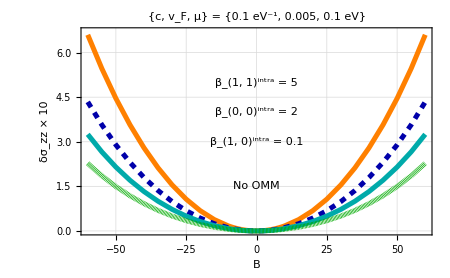
```mathematica
style={(**)Directive[Orange,Thickness[0.008]],(**)Directive[Darker[Blue],Thickness[0.008],Dashing[0.01]],Directive[Darker[Cyan],Thickness[0.008]],(**)Directive[Darker[Green],Thickness[0.008],Dashing[0.001]]};
g1=ListPlot[{dat11,dat21,dat31,dat41},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{-60,60},{Automatic,6.2}},LabelStyle->{Black,Bold,22},PlotStyle->style,PlotTheme->"Detailed",PlotLegends->None,Frame->True,FrameLabel->{"B","δσ_zz × 10"},PlotLabel->Style["{c, v_F, μ} = {0.1 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->450,(*****)Epilog->{Style[Text["β_(1, 1)^intra = 5",{0,4.75}],Darker[Brown],16,Bold],Style[Text["β_(0, 0)^intra = 2",{0,3.75}],Darker[Brown],16,Bold],(**)Style[Text["β_(1, 0)^intra = 0.1",{0,2.75}],Darker[Brown],16,Bold]}(*******)];

g3=ListPlot[{dat12,dat22,dat32,dat42},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{-60,60},All},LabelStyle->{Black,Bold,22},PlotStyle->style,PlotTheme->"Detailed",PlotLegends->None,Frame->True,FrameLabel->{"B","δσ_zz × 10^2"},PlotLabel->Style["{c, v_F, μ} = {0.1 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->475,(********)Epilog->{Style[Text["β_(1, 1)^intra = 5",{0,-1}],Darker[Brown],16,Bold],Style[Text["β_(0, 0)^intra = 2",{0,-1.75}],Darker[Brown],16,Bold],(**)Style[Text["β_(1, 0)^intra = 0.1",{0,-2.5}],Darker[Brown],16,Bold]}(*******)];

g2=-Graphics-;

leg=LineLegend[style,{"0.5","1","2","100"},LabelStyle->{18,Darker[Brown],Bold},LegendLayout->{"Row",1}];
pl=Legended[GraphicsGrid[{{g1},{g2}},Spacings->{0, 20},ImageSize->450],Placed[leg,Below]]
{rat1,rat2,rat3,rat4}
SetDirectory[NotebookDirectory[]];
Export["fig4a.pdf",Rasterize[pl],ImageResolution->100];
```

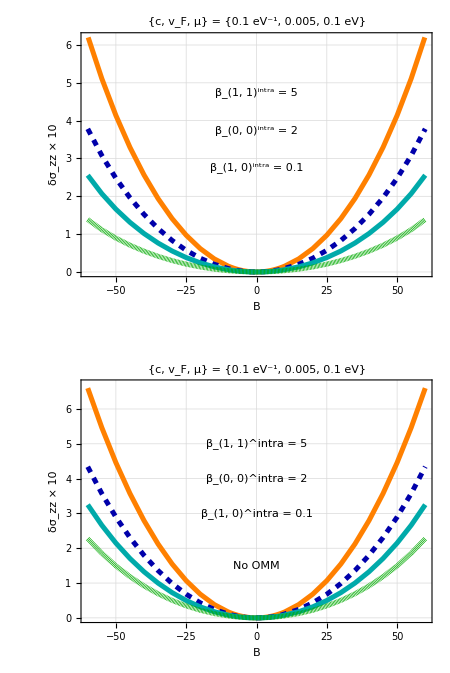

{0.5,1,2,100}

### set2

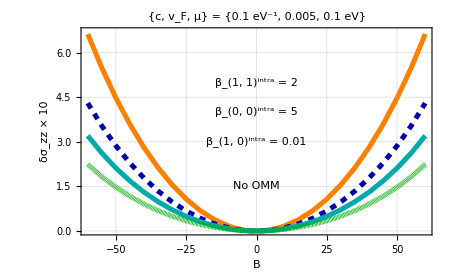
```mathematica
style={(**)Directive[Orange,Thickness[0.008]],(**)Directive[Darker[Blue],Thickness[0.008],Dashing[0.01]],Directive[Darker[Cyan],Thickness[0.008]],(**)Directive[Darker[Green],Thickness[0.008],Dashing[0.001]]};

g1=ListPlot[{dat51,dat61,dat71,dat81},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{-60,60},{Automatic,6.4}},LabelStyle->{Black,Bold,22},PlotStyle->style,PlotTheme->"Detailed",PlotLegends->None,Frame->True,FrameLabel->{"B","δσ_zz × 10"},PlotLabel->Style["{c, v_F, μ} = {0.1 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->450,(*****)Epilog->{Style[Text["β_(1, 1)^intra = 2",{0,5}],Darker[Brown],16,Bold],Style[Text["β_(0, 0)^intra = 5",{0,4}],Darker[Brown],16,Bold],(**)Style[Text["β_(1, 0)^intra = 0.01",{0,3}],Darker[Brown],16,Bold]}(*******)];

g3=ListPlot[{dat52,dat62,dat72,dat82},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{-60,60},All},LabelStyle->{Black,Bold,22},PlotStyle->style,PlotTheme->"Detailed",PlotLegends->None,Frame->True,FrameLabel->{"B","δσ_zz × 10^2"},PlotLabel->Style["{c, v_F, μ} = {0.1 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->475,(*****)Epilog->{Style[Text["β_(1, 1)^intra = 2",{0,-1}],Darker[Brown],16,Bold],Style[Text["β_(0, 0)^intra = 5",{0,-1.75}],Darker[Brown],16,Bold],(**)Style[Text["β_(1, 0)^intra = 0.01",{0,-2.5}],Darker[Brown],16,Bold]}(*******)];

g2=-Graphics-;

leg=LineLegend[style,{"0.5","1","2","100"},LabelStyle->{18,Darker[Brown],Bold},LegendLayout->{"Row",1}];
pl=Legended[GraphicsGrid[{{g1},{g2}},Spacings->{0, 20},ImageSize->450],Placed[leg,Below]]
{rat1,rat2,rat3,rat4}
SetDirectory[NotebookDirectory[]];
Export["fig4b.pdf",Rasterize[pl],ImageResolution->100];
```

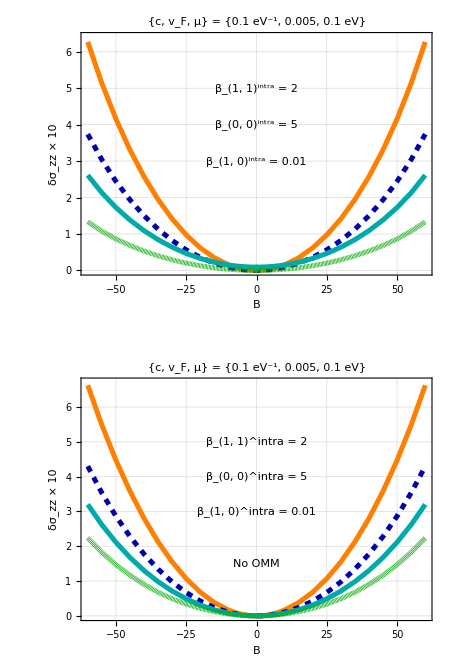

{0.5,1,2,100}

### set3

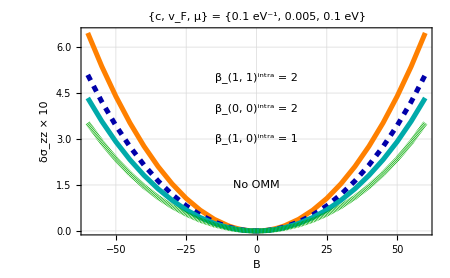
```mathematica
style={(**)Directive[Orange,Thickness[0.008]],(**)Directive[Darker[Blue],Thickness[0.008],Dashing[0.01]],Directive[Darker[Cyan],Thickness[0.008],Opacity[0.7]],(**)Directive[Darker[Green],Thickness[0.008],Dashing[0.001]]};

g1=ListPlot[{dat91,dat101,dat111,dat121},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{-60,60},{Automatic,6.2}},LabelStyle->{Black,Bold,22},PlotStyle->style,PlotTheme->"Detailed",PlotLegends->None,Frame->True,FrameLabel->{"B","δσ_zz × 10"},PlotLabel->Style["{c, v_F, μ} = {0.1 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->450,(*****)Epilog->{Style[Text["β_(1, 1)^intra = 2",{0,4.3}],Darker[Brown],16,Bold],(***)Style[Text["β_(0, 0)^intra = 2",{0,3.4}],Darker[Brown],16,Bold],(**)Style[Text["β_(1, 0)^intra = 1",{0,2.5}],Darker[Brown],16,Bold]}(*******)];

g3=ListPlot[{dat92,dat102,dat112,dat122},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{-60,60},All},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,PlotTheme->"Detailed",PlotLegends->None,FrameLabel->{"B","δσ_zz × 10^2"},PlotLabel->Style["{c, v_F, μ} = {0.1 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->470,(*****)Epilog->{Style[Text["β_(1, 1)^intra = 2",{0,-1}],Darker[Brown],16,Bold],Style[Text["β_(0, 0)^intra = 2",{0,-1.5}],Darker[Brown],16,Bold],(**)Style[Text["β_(1, 0)^intra = 1",{0,-2}],Darker[Brown],16,Bold]}(*******)];

g2=-Graphics-;
leg=LineLegend[style,{"0.5","1","2","100"},LabelStyle->{18,Darker[Brown],Bold},LegendLayout->{"Row",1}];

pl=Legended[GraphicsGrid[{{g1},{g2}},Spacings->{0, 20},ImageSize->450],Placed[leg,Below]]
{rat1,rat2,rat3,rat4}
SetDirectory[NotebookDirectory[]];
Export["fig4c.pdf",Rasterize[pl],ImageResolution->100];
```

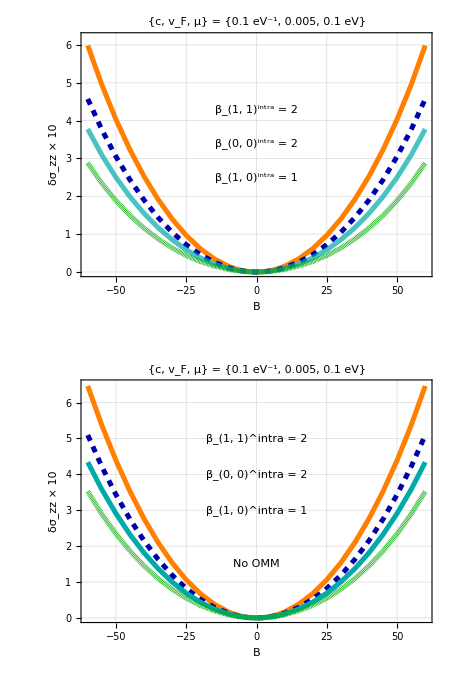

{0.5,1,2,100}

### set4

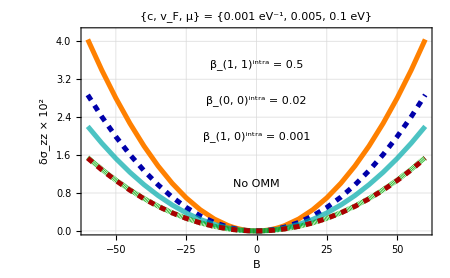
```mathematica
style={(**)Directive[Orange,Thickness[0.008]],(**)Directive[Darker[Blue],Thickness[0.008],Dashing[0.01]],Directive[Darker[Cyan],Thickness[0.008],Opacity[0.7]],(**)Directive[Darker[Green],Thickness[0.008],Dashing[0.001]],Directive[Darker[Red],Thickness[0.008],Dashing[0.01]]};

g1=ListPlot[{d11,d21,d31,d41,d51},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{-60,60},{-0.64,2.1}},LabelStyle->{Black,Bold,22},PlotStyle->style,PlotTheme->"Detailed",PlotLegends->None,Frame->True,FrameLabel->{"B","δσ_zz × 10^2"},PlotLabel->Style["{c, v_F, μ} = {0.001 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->450,(*****)Epilog->{Style[Text["β_(1, 1)^intra = 0.5",{0,1.7}],Darker[Brown],16,Bold],Style[Text["β_(0, 0)^intra = 0.02",{0,1.3}],Darker[Brown],16,Bold],(**)Style[Text["β_(1, 0)^intra = 0.001",{0,0.9}],Darker[Brown],16,Bold]}(*******)];
(* {0.5,0.02,0.001} *)

g2=-Graphics-;
(* {0.5,0.02,0.001} *)
leg=LineLegend[style,{"0.5","1","2","50","100"},LabelStyle->{18,Darker[Brown],Bold},LegendLayout->{"Row",1}];

pl=Legended[GraphicsGrid[{{g1,g2}},Spacings->{40, 0},ImageSize->450*2],Placed[leg,Below]]
{rat1,rat2,rat3,rat4p,rat5p}
SetDirectory[NotebookDirectory[]];
Export["fig6a.pdf",Rasterize[pl],ImageResolution->100];
```

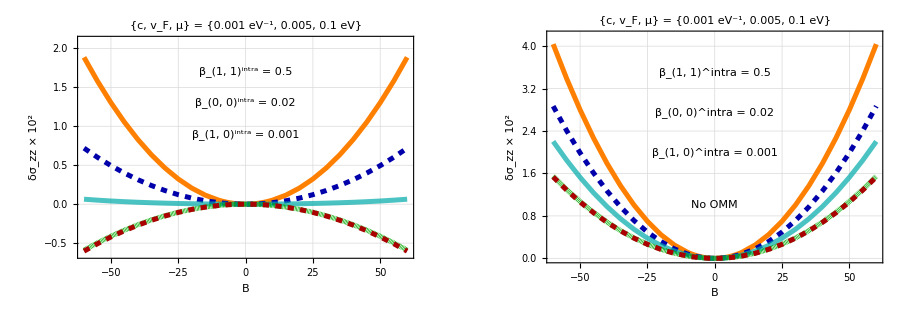

{0.5,1,2,50,50}

## plots s=0 bands

### set1

```mathematica
(*{B,s11+s21,s10+s20,{s11,s21,s10,s20}*)
```

```mathematica
list=tot1;len=Length[list];
x=list[[1,2,3]] ;
fl11=Sort[Join[Table[{-list[[i,1]],(list[[i,2,3]]/x-1)10^2 },{i,1,len}], Table[{list[[i,1]],(list[[i,2,3]]/x-1)10^2 },{i,1,len}]]];
x=list[[1,2,4]] ;
fl12=Sort[Join[Table[{-list[[i,1]],(list[[i,2,4]]/x-1)10^2 },{i,1,len}], Table[{list[[i,1]],(list[[i,2,4]]/x-1)10^2 },{i,1,len}]]];

list=tot2;len=Length[list];
x=list[[1,2,3]] ;
fl21=Sort[Join[Table[{-list[[i,1]],(list[[i,2,3]]/x-1)10^2 },{i,1,len}], Table[{list[[i,1]],(list[[i,2,3]]/x-1)10^2 },{i,1,len}]]];
x=list[[1,2,4]] ;
fl22=Sort[Join[Table[{-list[[i,1]],(list[[i,2,4]]/x-1)10^2 },{i,1,len}], Table[{list[[i,1]],(list[[i,2,4]]/x-1)10^2 },{i,1,len}]]];

list=tot3;len=Length[list];x=list[[1,2,3]] ;
fl31=Sort[Join[Table[{-list[[i,1]],(list[[i,2,3]]/x-1)10^2 },{i,1,len}], Table[{list[[i,1]],(list[[i,2,3]]/x-1)10^2 },{i,1,len}]]];
x=list[[1,2,4]] ;
fl32=Sort[Join[Table[{-list[[i,1]],(list[[i,2,4]]/x-1)10^2 },{i,1,len}], Table[{list[[i,1]],(list[[i,2,4]]/x-1)10^2 },{i,1,len}]]];

list=tot4;len=Length[list];x=list[[1,2,3]] ;
fl41=Sort[Join[Table[{-list[[i,1]],(list[[i,2,3]]/x-1)10^2 },{i,1,len}], Table[{list[[i,1]],(list[[i,2,3]]/x-1)10^2 },{i,1,len}]]];

x=list[[1,2,4]] ;
fl42=Sort[Join[Table[{-list[[i,1]],(list[[i,2,4]]/x-1)10^2 },{i,1,len}], Table[{list[[i,1]],(list[[i,2,4]]/x-1)10^2 },{i,1,len}]]];
```

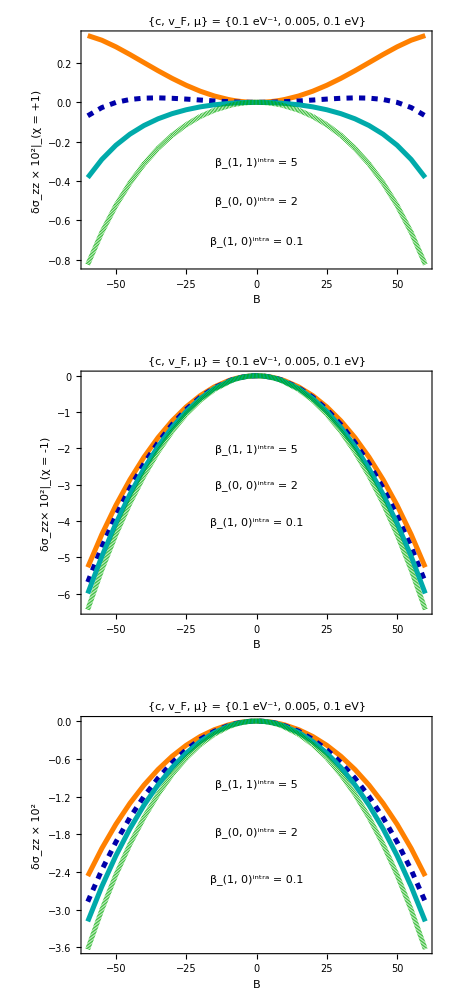

{0.5,1,2,100}

```mathematica
style={(**)Directive[Orange,Thickness[0.008]],(**)Directive[Darker[Blue],Thickness[0.008],Dashing[0.01]],Directive[Darker[Cyan],Thickness[0.008]],(**)Directive[Darker[Green],Thickness[0.008],Dashing[0.001]]};
g1=ListPlot[{fl11,fl21,fl31,fl41},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{-60,60},All},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,FrameLabel->{"B","δσ_zz × 10^2|_(χ = +1)"},PlotLabel->Style["{c, v_F, μ} = {0.1 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->450,(*****)Epilog->{Style[Text["β_(1, 1)^intra = 5",{0,-0.3}],Darker[Brown],16,Bold],Style[Text["β_(0, 0)^intra = 2",{0,-0.5}],Darker[Brown],16,Bold],(**)Style[Text["β_(1, 0)^intra = 0.1",{0,-0.7}],Darker[Brown],16,Bold]}(*******)];

g2=ListPlot[{fl12,fl22,fl32,fl42},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16],PlotRange->{{-60,60},All},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,FrameLabel->{"B","δσ_zz× 10^2|_(χ = -1)"},PlotLabel->Style["{c, v_F, μ} = {0.1 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->450,(*****)Epilog->{Style[Text["β_(1, 1)^intra = 5",{0,-2}],Darker[Brown],16,Bold],Style[Text["β_(0, 0)^intra = 2",{0,-3}],Darker[Brown],16,Bold],(**)Style[Text["β_(1, 0)^intra = 0.1",{0,-4}],Darker[Brown],16,Bold]}(*******)];

g3=ListPlot[{dat12,dat22,dat32,dat42},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16],PlotRange->{{-60,60},All},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,FrameLabel->{"B","δσ_zz × 10^2"},PlotLabel->Style["{c, v_F, μ} = {0.1 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->450,(********)Epilog->{Style[Text["β_(1, 1)^intra = 5",{0,-1}],Darker[Brown],16,Bold],Style[Text["β_(0, 0)^intra = 2",{0,-1.75}],Darker[Brown],16,Bold],(**)Style[Text["β_(1, 0)^intra = 0.1",{0,-2.5}],Darker[Brown],16,Bold]}(*******)];

leg=LineLegend[style,{"0.5","1","2","100"},LabelStyle->{18,Darker[Brown],Bold},LegendLayout->{"Row",1}];
pl=Legended[GraphicsGrid[{{g1},{g2},{g3}},Spacings->{0, 20},ImageSize->450],Placed[leg,Below]]
{rat1,rat2,rat3,rat4}
SetDirectory[NotebookDirectory[]];
Export["fig5a.pdf",Rasterize[pl],ImageResolution->100];
```

### set2

```mathematica
list=tot5;len=Length[list];
x=list[[1,2,3]] ;
fl51=Sort[Join[Table[{-list[[i,1]],(list[[i,2,3]]/x-1)10^2 },{i,1,len}], Table[{list[[i,1]],(list[[i,2,3]]/x-1)10^2 },{i,1,len}]]];
x=list[[1,2,4]] ;
fl52=Sort[Join[Table[{-list[[i,1]],(list[[i,2,4]]/x-1)10^2 },{i,1,len}], Table[{list[[i,1]],(list[[i,2,4]]/x-1)10^2 },{i,1,len}]]];
list=tot6;len=Length[list];
x=list[[1,2,3]] ;
fl61=Sort[Join[Table[{-list[[i,1]],(list[[i,2,3]]/x-1)10^2 },{i,1,len}], Table[{list[[i,1]],(list[[i,2,3]]/x-1)10^2 },{i,1,len}]]];
x=list[[1,2,4]] ;
fl62=Sort[Join[Table[{-list[[i,1]],(list[[i,2,4]]/x-1)10^2 },{i,1,len}], Table[{list[[i,1]],(list[[i,2,4]]/x-1)10^2 },{i,1,len}]]];

list=tot7;len=Length[list];x=list[[1,2,3]] ;
fl71=Sort[Join[Table[{-list[[i,1]],(list[[i,2,3]]/x-1)10^2 },{i,1,len}], Table[{list[[i,1]],(list[[i,2,3]]/x-1)10^2 },{i,1,len}]]];
x=list[[1,2,4]] ;
fl72=Sort[Join[Table[{-list[[i,1]],(list[[i,2,4]]/x-1)10^2 },{i,1,len}], Table[{list[[i,1]],(list[[i,2,4]]/x-1)10^2 },{i,1,len}]]];

list=tot8;len=Length[list];x=list[[1,2,3]] ;
fl81=Sort[Join[Table[{-list[[i,1]],(list[[i,2,3]]/x-1)10^2 },{i,1,len}], Table[{list[[i,1]],(list[[i,2,3]]/x-1)10^2 },{i,1,len}]]];
x=list[[1,2,4]] ;
fl82=Sort[Join[Table[{-list[[i,1]],(list[[i,2,4]]/x-1)10^2 },{i,1,len}], Table[{list[[i,1]],(list[[i,2,4]]/x-1)10^2 },{i,1,len}]]];
```

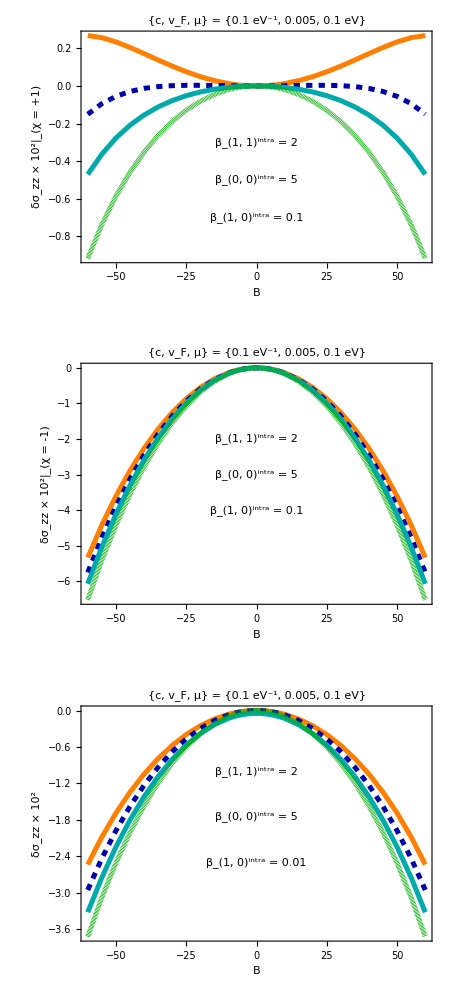

{0.5,1,2,100}

```mathematica
style={(**)Directive[Orange,Thickness[0.008]],(**)Directive[Darker[Blue],Thickness[0.008],Dashing[0.01]],Directive[Darker[Cyan],Thickness[0.008]],(**)Directive[Darker[Green],Thickness[0.008],Dashing[0.001]]};

style={(**)Directive[Orange,Thickness[0.008]],(**)Directive[Darker[Blue],Thickness[0.008],Dashing[0.01]],Directive[Darker[Cyan],Thickness[0.008]],(**)Directive[Darker[Green],Thickness[0.008],Dashing[0.001]]};

g1=ListPlot[{fl51,fl61,fl71,fl81},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{-60,60},All},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,FrameLabel->{"B","δσ_zz × 10^2|_(χ = +1)"},PlotLabel->Style["{c, v_F, μ} = {0.1 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->450,(*****)Epilog->{Style[Text["β_(1, 1)^intra = 2",{0,-0.3}],Darker[Brown],16,Bold],Style[Text["β_(0, 0)^intra = 5",{0,-0.5}],Darker[Brown],16,Bold],(**)Style[Text["β_(1, 0)^intra = 0.1",{0,-0.7}],Darker[Brown],16,Bold]}(*******)];

g2=ListPlot[{fl52,fl62,fl72,fl82},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{-60,60},All},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,FrameLabel->{"B","δσ_zz × 10^2|_(χ = -1)"},PlotLabel->Style["{c, v_F, μ} = {0.1 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->450,(*****)Epilog->{Style[Text["β_(1, 1)^intra = 2",{0,-2}],Darker[Brown],16,Bold],Style[Text["β_(0, 0)^intra = 5",{0,-3}],Darker[Brown],16,Bold],(**)Style[Text["β_(1, 0)^intra = 0.1",{0,-4}],Darker[Brown],16,Bold]}(*******)];

g3=ListPlot[{dat52,dat62,dat72,dat82},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{-60,60},All},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,FrameLabel->{"B","δσ_zz × 10^2"},PlotLabel->Style["{c, v_F, μ} = {0.1 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->450,(*****)Epilog->{Style[Text["β_(1, 1)^intra = 2",{0,-1}],Darker[Brown],16,Bold],Style[Text["β_(0, 0)^intra = 5",{0,-1.75}],Darker[Brown],16,Bold],(**)Style[Text["β_(1, 0)^intra = 0.01",{0,-2.5}],Darker[Brown],16,Bold]}(*******)];


leg=LineLegend[style,{"0.5","1","2","100"},LabelStyle->{18,Darker[Brown],Bold},LegendLayout->{"Row",1}];
pl=Legended[GraphicsGrid[{{g1},{g2},{g3}},Spacings->{0, 20},ImageSize->450],Placed[leg,Below]]
{rat1,rat2,rat3,rat4}
SetDirectory[NotebookDirectory[]];
Export["fig5b.pdf",Rasterize[pl],ImageResolution->100];
```

### set3

```mathematica
list=tot9;len=Length[list];
x=list[[1,2,3]] ;
fl91=Sort[Join[Table[{-list[[i,1]],(list[[i,2,3]]/x-1)10^2 },{i,1,len}], Table[{list[[i,1]],(list[[i,2,3]]/x-1)10^2 },{i,1,len}]]];
x=list[[1,2,4]] ;
fl92=Sort[Join[Table[{-list[[i,1]],(list[[i,2,4]]/x-1)10^2 },{i,1,len}], Table[{list[[i,1]],(list[[i,2,4]]/x-1)10^2 },{i,1,len}]]];

list=tot10;len=Length[list];
x=list[[1,2,3]] ;
fl101=Sort[Join[Table[{-list[[i,1]],(list[[i,2,3]]/x-1)10^2 },{i,1,len}], Table[{list[[i,1]],(list[[i,2,3]]/x-1)10^2 },{i,1,len}]]];
x=list[[1,2,4]] ;
fl102=Sort[Join[Table[{-list[[i,1]],(list[[i,2,4]]/x-1)10^2 },{i,1,len}], Table[{list[[i,1]],(list[[i,2,4]]/x-1)10^2 },{i,1,len}]]];

list=tot11;len=Length[list];x=list[[1,2,3]] ;
fl111=Sort[Join[Table[{-list[[i,1]],(list[[i,2,3]]/x-1)10^2 },{i,1,len}], Table[{list[[i,1]],(list[[i,2,3]]/x-1)10^2 },{i,1,len}]]];
x=list[[1,2,4]] ;
fl112=Sort[Join[Table[{-list[[i,1]],(list[[i,2,4]]/x-1)10^2 },{i,1,len}], Table[{list[[i,1]],(list[[i,2,4]]/x-1)10^2 },{i,1,len}]]];
list=tot12;len=Length[list];x=list[[1,2,3]] ;
fl121=Sort[Join[Table[{-list[[i,1]],(list[[i,2,3]]/x-1)10^2 },{i,1,len}], Table[{list[[i,1]],(list[[i,2,3]]/x-1)10^2 },{i,1,len}]]];
x=list[[1,2,4]] ;
fl122=Sort[Join[Table[{-list[[i,1]],(list[[i,2,4]]/x-1)10^2 },{i,1,len}], Table[{list[[i,1]],(list[[i,2,4]]/x-1)10^2 },{i,1,len}]]];
```

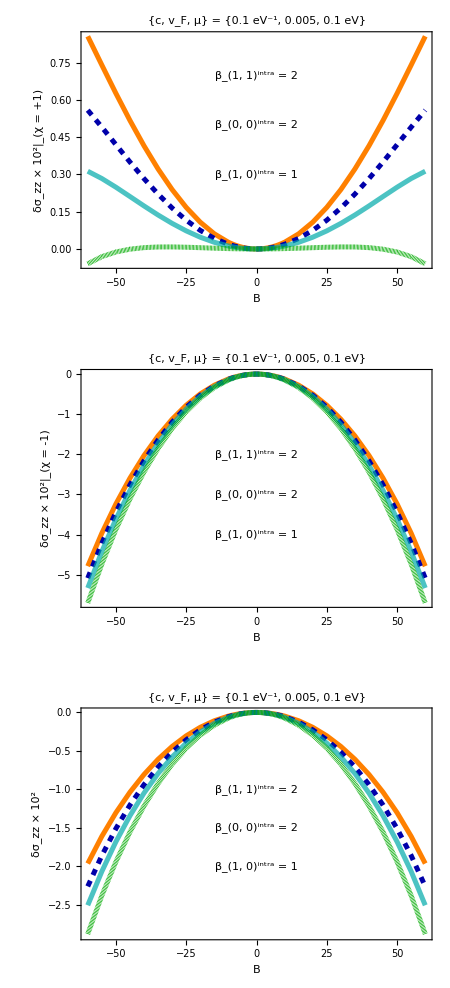

{0.5,1,2,100}

```mathematica
style={(**)Directive[Orange,Thickness[0.008]],(**)Directive[Darker[Blue],Thickness[0.008],Dashing[0.01]],Directive[Darker[Cyan],Thickness[0.008],Opacity[0.7]],(**)Directive[Darker[Green],Thickness[0.008],Dashing[0.001]]};

g1=ListPlot[{fl91,fl101,fl111,fl121},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{-60,60},All},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,FrameLabel->{"B","δσ_zz × 10^2|_(χ = +1)"},PlotLabel->Style["{c, v_F, μ} = {0.1 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->450,(*****)Epilog->{Style[Text["β_(1, 1)^intra = 2",{0,0.7}],Darker[Brown],16,Bold],Style[Text["β_(0, 0)^intra = 2",{0,0.5}],Darker[Brown],16,Bold],(**)Style[Text["β_(1, 0)^intra = 1",{0,0.3}],Darker[Brown],16,Bold]}(*******)];

g2=ListPlot[{fl92,fl102,fl112,fl122},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{-60,60},{-5.7,Automatic}},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,FrameLabel->{"B","δσ_zz × 10^2|_(χ = -1)"},PlotLabel->Style["{c, v_F, μ} = {0.1 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->450,(*****)Epilog->{Style[Text["β_(1, 1)^intra = 2",{0,-2}],Darker[Brown],16,Bold],Style[Text["β_(0, 0)^intra = 2",{0,-3}],Darker[Brown],16,Bold],(**)Style[Text["β_(1, 0)^intra = 1",{0,-4}],Darker[Brown],16,Bold]}(*******)];


g3=ListPlot[{dat92,dat102,dat112,dat122},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{-60,60},{-2.9,Automatic}},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,FrameLabel->{"B","δσ_zz × 10^2"},PlotLabel->Style["{c, v_F, μ} = {0.1 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->450,(*****)Epilog->{Style[Text["β_(1, 1)^intra = 2",{0,-1}],Darker[Brown],16,Bold],Style[Text["β_(0, 0)^intra = 2",{0,-1.5}],Darker[Brown],16,Bold],(**)Style[Text["β_(1, 0)^intra = 1",{0,-2}],Darker[Brown],16,Bold]}(*******)];
leg=LineLegend[style,{"0.5","1","2","100"},LabelStyle->{18,Darker[Brown],Bold},LegendLayout->{"Row",1}];

pl=Legended[GraphicsGrid[{{g1},{g2},{g3}},Spacings->{0, 20},ImageSize->450],Placed[leg,Below]]
{rat1,rat2,rat3,rat4}
SetDirectory[NotebookDirectory[]];
Export["fig5c.pdf",Rasterize[pl],ImageResolution->100];
```

### set4

```mathematica
list=tot13;len=Length[list];
x=list[[1,2,3]] ;
fl131=Sort[Join[Table[{-list[[i,1]],(list[[i,2,3]]/x-1)10^4 },{i,1,len}],Table[{list[[i,1]],(list[[i,2,3]]/x-1)10^4 },{i,1,len}]]];
x=list[[1,2,4]] ;
fl132=Sort[Join[Table[{-list[[i,1]],(list[[i,2,4]]/x-1)10^4 },{i,1,len}], Table[{list[[i,1]],(list[[i,2,4]]/x-1)10^4 },{i,1,len}]]];

list=tot14;len=Length[list];
x=list[[1,2,3]] ;
fl141=Sort[Join[Table[{-list[[i,1]],(list[[i,2,3]]/x-1)10^4 },{i,1,len}],Table[{list[[i,1]],(list[[i,2,3]]/x-1)10^4 },{i,1,len}]]];
x=list[[1,2,4]] ;
fl142=Sort[Join[Table[{-list[[i,1]],(list[[i,2,4]]/x-1)10^4 },{i,1,len}], Table[{list[[i,1]],(list[[i,2,4]]/x-1)10^4 },{i,1,len}]]];

list=tot15;len=Length[list];x=list[[1,2,3]] ;
fl151=Sort[Join[Table[{-list[[i,1]],(list[[i,2,3]]/x-1)10^4 },{i,1,len}],Table[{list[[i,1]],(list[[i,2,3]]/x-1)10^4 },{i,1,len}]]];
x=list[[1,2,4]] ;
fl152=Sort[Join[Table[{-list[[i,1]],(list[[i,2,4]]/x-1)10^4 },{i,1,len}], Table[{list[[i,1]],(list[[i,2,4]]/x-1)10^4 },{i,1,len}]]];

list=tot16;len=Length[list];x=list[[1,2,3]] ;
fl161=Table[{list[[i,1]],(list[[i,2,3]]/x-1 )10^4},{i,1,len}];
x=list[[1,2,4]] ;
fl162=Sort[Join[Table[{-list[[i,1]],(list[[i,2,4]]/x-1)10^4 },{i,1,len}], Table[{list[[i,1]],(list[[i,2,4]]/x-1)10^4 },{i,1,len}]]];

list=tot17;len=Length[list];x=list[[1,2,3]] ;
fl171=Sort[Join[Table[{-list[[i,1]],(list[[i,2,3]]/x-1)10^4 },{i,1,len}],Table[{list[[i,1]],(list[[i,2,3]]/x-1)10^4 },{i,1,len}]]];
x=list[[1,2,4]] ;
fl172=Sort[Join[Table[{-list[[i,1]],(list[[i,2,4]]/x-1)10^4 },{i,1,len}], Table[{list[[i,1]],(list[[i,2,4]]/x-1)10^4 },{i,1,len}]]];
```

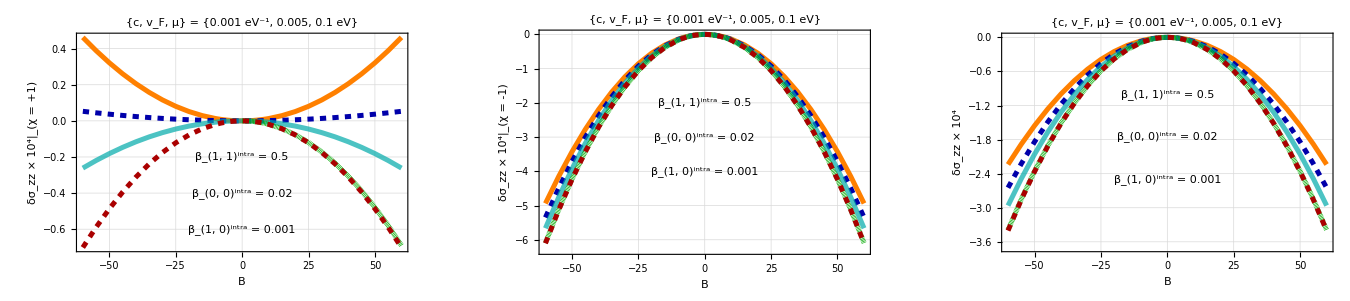

{0.5,1,2,50,50}

```mathematica
style={(**)Directive[Orange,Thickness[0.008]],(**)Directive[Darker[Blue],Thickness[0.008],Dashing[0.01]],Directive[Darker[Cyan],Thickness[0.008],Opacity[0.7]],(**)Directive[Darker[Green],Thickness[0.008],Dashing[0.001]],Directive[Darker[Red],Thickness[0.008],Dashing[0.01]]};

g1=ListPlot[{fl131,fl141,fl151,fl161,fl171},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{-60,60},All},LabelStyle->{Black,Bold,22},PlotStyle->style,PlotTheme->"Detailed",PlotLegends->None,Frame->True,FrameLabel->{"B","δσ_zz × 10^4|_(χ = +1)"},PlotLabel->Style["{c, v_F, μ} = {0.001 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->450,(*****)Epilog->{Style[Text["β_(1, 1)^intra = 0.5",{0,-0.2}],Darker[Brown],16,Bold],Style[Text["β_(0, 0)^intra = 0.02",{0,-0.4}],Darker[Brown],16,Bold],(**)Style[Text["β_(1, 0)^intra = 0.001",{0,-0.6}],Darker[Brown],16,Bold]}(*******)];

g2=ListPlot[{fl132,fl142,fl152,fl162,fl172},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{-60,60},{-6.3,Automatic}},LabelStyle->{Black,Bold,22},PlotStyle->style,PlotTheme->"Detailed",PlotLegends->None,Frame->True,FrameLabel->{"B","δσ_zz × 10^4|_(χ = -1)"},PlotLabel->Style["{c, v_F, μ} = {0.001 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->450,(*****)Epilog->{Style[Text["β_(1, 1)^intra = 0.5",{0,-2}],Darker[Brown],16,Bold],Style[Text["β_(0, 0)^intra = 0.02",{0,-3}],Darker[Brown],16,Bold],(**)Style[Text["β_(1, 0)^intra = 0.001",{0,-4}],Darker[Brown],16,Bold]}(*******)];
(* {0.5,0.02,0.001} *)
g3=ListPlot[{d12,d22,d32,d42,d52},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16,FontFamily->"Times"],PlotRange->{{-60,60},{-3.7,Automatic}},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,FrameLabel->{"B","δσ_zz × 10^4"},PlotTheme->"Detailed",PlotLegends->None,PlotLabel->Style["{c, v_F, μ} = {0.001 eV^-1, 0.005, 0.1 eV}",Bold,Darker[Brown],18],ImageSize->450,(*****)Epilog->{Style[Text["β_(1, 1)^intra = 0.5",{0,-1}],Darker[Brown],16,Bold],Style[Text["β_(0, 0)^intra = 0.02",{0,-1.75}],Darker[Brown],16,Bold],(**)Style[Text["β_(1, 0)^intra = 0.001",{0,-2.5}],Darker[Brown],16,Bold]}(*******)];

(* {0.5,0.02,0.001} *)
leg=LineLegend[style,{"0.5","1","2","50","100"},LabelStyle->{18,Darker[Brown],Bold},LegendLayout->{"Row",1}];

pl=Legended[GraphicsGrid[{{g1,g2,g3}},Spacings->{40, 0},ImageSize->450*3],Placed[leg,Below]]
{rat1,rat2,rat3,rat4p,rat5p}
SetDirectory[NotebookDirectory[]];
Export["fig6b.pdf",Rasterize[pl],ImageResolution->100];
```